# 第四章 定位导航

## 旋转矩阵

```mathematica
frameGlobal={{RGBColor[Flatten[{#,0}]],Arrowheads[0.02],Arrow@{{0,0},#}}&/@IdentityMatrix[2]};
frameLocal={{RGBColor[Flatten[{#,0}]],Arrowheads[0.02],Arrow@{{0,0},#}}&/@(0.7*IdentityMatrix[2])};
Latinfont="Latin Modern Roman 10";
Manipulate[
R=RotationMatrix[α];
Graphics[{frameGlobal,GeometricTransformation[{frameLocal},R]},PlotRange->{{-2,2},{-2,2}}],{{α,0,Style["α",26]},-Pi,Pi,0.01,ImageSize->250},
ControlPlacement->{Left},Alignment->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 本体速度与空间速度

```mathematica
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
R=RotationMatrix[Pi/2,{0,1,0}].RotationMatrix[θ[t],{0,0,1}];
TraditionalForm[R]
b=FullSimplify[Transpose[R].D[R,t]];
UnSkew[b]
s=FullSimplify[D[R,t].Transpose[R]];
UnSkew[s]
TraditionalForm[b]
TraditionalForm[s]
```

```mathematica
frameGlobal={{RGBColor[#],Arrowheads[0.03],Arrow@Tube[{{0,0,0},#},0.008]}&/@(1.4*IdentityMatrix[3])};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@({0.7,0.7,0.85}*IdentityMatrix[3])};
rot=RotationMatrix[Pi,{0,0,1}];
trans={0,0.1,-0.2};
Latinfont="Latin Modern Roman 10";
ArrowCircle={Black,Arrowheads[{{0.02,1,Graphics3D@Cone[{{-1/4,0,0},{3/4,0,0}},0.2]}}],Arrow[Tube[BSplineCurve[Table[Flatten[{0.7,0.2AngleVector[a]}],{a,0,3Pi/2,0.05}]],0.007]]};
Manipulate[
R=RotationMatrix[Pi/2,{0,1,0}].RotationMatrix[θ,{0,0,1}];
Graphics3D[{ArrowCircle,GeometricTransformation[frameGlobal,TranslationTransform[{-2,-1,-1}]],GeometricTransformation[{{Yellow,duck},frameLocal},R]},PlotRange->{{-3,2},{-2,2},{-1.6,1.7}}/1.5,ViewAngle->0.450024,ViewPoint->{2.19523,-2.33708,1.08122},ViewVertical->{0.160427,-0.229443,0.96001},Boxed->True,BoxStyle->Directive[{AbsoluteThickness[1.47],Dashed}],PlotRangePadding->None,ImageSize->600],{{θ,-Pi/1.2*0,Style["α",16]},-Pi,Pi/2,0.01,ControlPlacement->Top},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## LOAM曲率可视化

```mathematica
Latinfont="Latin Modern Roman 10";
pt={0,0};
r=0.01;
Manipulate[
ptR=AngleVector[α]*#&/@Range[0.1,0.5,0.1];
ptL=AngleVector[Pi-α]*#&/@Range[0.1,0.5,0.1];
pts=Join[ptR,ptL];
c=Norm@Total@Table[(i-pt),{i,pts}];
Graphics[{Text[Style[Chop@c,FontFamily->Latinfont,FontSize->16],{0,-0.3}],Black,Disk[#,r]&/@ptR,Disk[#,r]&/@ptL,Arrowheads[0.02](*,Arrow[{pt,#}]&/@pts*),Red,Disk[pt,r]},PlotRange->{0.9{-1,1},{-0.5,0.8}}],{{α,Pi/3},0,Pi/2.0,0.01},LabelStyle->Directive[Black,FontSize->18,FontFamily->Latinfont],ControlPlacement->Top,TrackedSymbols:>True]
```

## LOAM点到直线距离

```mathematica
Off[General::shdw,Unset::norep];
SetDirectory[NotebookDirectory[]<>"Packages"];
<<Myfunction.m ;
<<ModernRobotics.m ;
```

```mathematica
R=RotationMatrix[Pi/3,{0,0,1}];
t={0,0,1};
RPToH[R,t]
MatrixLog6[RPToH[R,t]]
u=dehat@MatrixLog6[RPToH[R,t]]
MatrixExp6[hat[u]]
MatrixExp[hat[u]]
```

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
n={1,1,1};
pg={0,0,0};
p={1,0,1};
pn=Cross[(p-pg),n]/Norm[Cross[(p-pg),n]];
R=RotationMatrix[0.0,{0,0,1}];
t={0,0,0};
p=R.p+t;
ps=ds={};
For[i=1,i<1000,i++,
ξ=dehat@MatrixLog6[RPToH[R,t]];
pn=Cross[(p-pg),n]/Norm[Cross[(p-pg),n]];
J=ConstantArray[0,{3,6}];
J⟦1;;3,1;;3⟧=IdentityMatrix[3];
J⟦1;;3,4;;6⟧=-Skew[R.p+t];
y=Table[pn.Cross[j,n],{j,Transpose[J]}];
ξ=ξ-0.0001*y;
Rt=MatrixExp[hat[ξ]];
(*Rt=MatrixExp[hat[-0.0001y]].RPToH[R,t];*)
R=Rt⟦1;;3,1;;3⟧;
t=Rt⟦1;;3,4⟧;
p=R.p+t;
dist=Norm[Cross[(p-pg),n]];
AppendTo[ds,dist];
AppendTo[ps,p];
If[dist<0.02,Print["distance = "<>ToString@dist];Break[]];];
ListLinePlot[ds,PlotRange->All];
frameGlobal={{RGBColor[#],Arrowheads[0.03],Arrow@Tube[{{0,0,0},#},0.008]}&/@IdentityMatrix[3]};
Manipulate[Graphics3D[{
frameGlobal,AbsoluteThickness[0.8],Line[{-0.2n,n}],
AbsolutePointSize[4],Point[ps⟦i⟧],Point[ps⟦i⟧],Red,Line[ps⟦1;;-1⟧]},PlotRange->{{-1,2},{-1,2},{-0.2,2}},ViewAngle->0.4776,ViewCenter->{{0.5,0.5,0.5},{0.524306,0.525695}},ViewPoint->{-2.97258,-1.29457,0.968455},ViewVertical->{-0.262966,-0.104767,0.9591},ViewVertical->{-0.173492,-0.0865256,0.981027},Boxed->True,BoxStyle->Directive[AbsoluteThickness[0.5],Black]],{i,1,Length[ps],1}]
```

## LOAM点到平面的距离

## LOAM协方差矩阵

```mathematica
Off[General::shdw,Unset::norep];
SetDirectory[NotebookDirectory[]<>"Packages"];
<<Myfunction.m ;
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->20,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->26,FontFamily->Latinfont]]&;
controlfontsize=20;
barsize=120;
Manipulate[
pts=Table[{RandomReal[{-a,a}],RandomReal[{-b,b}],RandomReal[{-c,c}]},{i,2000}];
pts=Select[pts,#⟦1⟧^2/a^2+#⟦2⟧^2/b^2+#⟦3⟧^2/c^2≤1&];
center=Mean[Transpose[MinMax/@Transpose@pts]];
cm=Covariance[pts];
eVectors=Eigenvectors@cm;
eValues=Eigenvalues@cm;
Graphics3D[{Black,AbsolutePointSize[2.2],Point[pts],
Arrowheads[0.03],
Red,     Arrow[Tube[{center,center+Min[eValues⟦1⟧,a]*eVectors⟦1⟧},0.3]],
Green,Arrow[Tube[{center,center+Min[eValues⟦2⟧,b]*eVectors⟦2⟧},0.3]],
Blue,  Arrow[Tube[{center,center+Min[eValues⟦3⟧,c]*eVectors⟦3⟧},0.3]]
},PlotRange->25,Axes->True,ImageSize->500,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"},BoxStyle->Directive[Black,AbsoluteThickness[0.6]]],Grid[{{Control[{{a,15,Style["a",controlfontsize]},1,20,1,ImageSize->barsize}],Control[{{b,4,Style["b",controlfontsize]},1,20,1,ImageSize->barsize}],Control[{{c,4,Style["c",controlfontsize]},1,20,1,ImageSize->barsize}]}}],LabelStyle->Directive[Black,Italic,FontSize->12,FontFamily->Latinfont],ControlPlacement->Top,TrackedSymbols:>True]
```

## 旋转+平移

```mathematica
SetDirectory[NotebookDirectory[]];
import=Import["car.png"];
imagegraphics=ImageGraphics[import,Method->"DualMarchingSquares"];
cardata=imagegraphics⟦1⟧;
car=Table[
outerpart=cardata⟦1⟧;
{{xmin,xmax},{ymin,ymax}}=CoordinateBounds[outerpart⟦2,1⟧]/2;
center={xmin+xmax,ymin+ymax}/2;
offset=(-center+{40,-60});
colorcomplex=cardata⟦i⟧;
color=colorcomplex⟦1⟧;
{color,GraphicsComplex[(offset+#&/@colorcomplex⟦2,1⟧)/200.0,colorcomplex⟦2,2⟧]},{i,Length[cardata]}];
Graphics[{car,frameGlobal}];
```

```mathematica
import=Import["obs.png"];
imagegraphics=ImageGraphics[import,Method->"DualMarchingSquares"];
obsdata=imagegraphics⟦1⟧;
obs=Table[
outerpart=cardata⟦1⟧;
{{xmin,xmax},{ymin,ymax}}=CoordinateBounds[outerpart⟦2,1⟧]/2;
center={xmin+xmax,ymin+ymax}/2;
offset=(-center+{40,-60});
colorcomplex=obsdata⟦i⟧;
color=colorcomplex⟦1⟧;
{color,GraphicsComplex[(offset+#&/@colorcomplex⟦2,1⟧)/200.0,colorcomplex⟦2,2⟧]},{i,Length[obsdata]}];
Graphics[{obs,frameGlobal}];
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[0.002],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.03}]};
textStyle=Text[Style[#,Italic,FontSize->16,FontFamily->Latinfont]]&;
poseToH[{x_,y_,a_}]:={{Cos[a],-Sin[a],x},{Sin[a],Cos[a],y},{0,0,1}};
move2D[shape_,pose_]:=Translate[Rotate[shape,pose[[3]],{0,0}],pose[[1;;2]]];
HToPose[g_]:=Module[{x,y,a,a1,a2},
{x,y}=g[[1;;2,3]];
a1=Re@ArcSin[-g[[1,2]]];
a2=Re@ArcCos[g[[1,1]]];
a=If[a1!=a2,If[a2>0&&a1<0,2Pi-a2,a2],a1];
{x,y,a}];
frameLocal={{RGBColor[Flatten[{#,0}]],Arrowheads[0.02],Arrow@{{0,0},0.8#}}&/@(IdentityMatrix[2])};
Manipulate[
{x,y}=egopos;
{xo,yo}=obspos;
egopose=Flatten[{egopos,θ}];
obspose=Flatten[{obspos,θo}];
Hegoobspose=Inverse[poseToH[egopose]].poseToH[obspose];
calpose=HToPose[poseToH[egopose].Hegoobspose];
Graphics[{
move2D[{car,frameLocal},egopose],
Opacity[0.8],move2D[obs,obspose],
move2D[frameLocal,calpose],
Gray,Dashed,AbsoluteThickness[0.7],
Line[{{x,y},{0,y}}],Line[{{x,y},{x,0}}],
Black,Text[Style["x",FontFamily->Latinfont,Italic,FontSize->20],{x/2,0.5+y}],
Black,Text[Style["y",FontFamily->Latinfont,Italic,FontSize->20],{0.3+x,y/2}],
Black,Text[Style["θ",FontFamily->Latinfont,FontSize->17],{x,y}+0.7*AngleVector[θ/2]],
Dashing[None],
Line[{{x,y},{x,y}+{0.8,0}}],
Circle[{x,y},0.25,{0,θ}]
},PlotRange->{{0,16},{0,8}},FrameTicks->{Automatic,{0,1,2,3}},Axes->True,
AxesStyle->{axesStyle,axesStyle}(*,AxesLabel->textStyle/@{"X","Y"}*)],
{{θ,0.5,Style["θ ",20]},-Pi,Pi,0.01,ImageSize->220},
{{θo,1.3,Style[" θ_o",20]},-Pi,Pi,0.01,ImageSize->220},
{{egopos,{4,2}},Locator,LocatorAutoCreate->True,Appearance->Style["•",Red,19]},{{obspos,{10,4}},Locator,LocatorAutoCreate->True,Appearance->Style["•",Red,19]},Alignment->Top,ControlPlacement->{Top},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 欧拉角

■   小黄鸭姿态表示示例

```mathematica
(*导入小黄鸭的三维模型*)
SetDirectory[NotebookDirectory[]];
duckdata=Import["duck.STL","Graphics3D"];
duck=duckdata⟦1⟧;
scale=0.013;
R=RotationMatrix[Pi/2.,{0,0,1}];
p={-0.22,0,0.1};
duckGraphics=GraphicsComplex[p+1000*scale*R.#&/@duckdata⟦1,1⟧,duckdata⟦1,2⟧];
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
duck={EdgeForm[],FaceForm[Yellow],duckGraphics,Black,Sphere[p+scale*{34,14,24},scale*4],Sphere[p+scale*{34,-14,24},scale*4],White,Sphere[p+scale*{35.7,15,25},scale*2],Sphere[p+scale*{35.7,-15.,25.},scale*2]};
Graphics3D[duck];
```

```mathematica
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.007]}&/@({0.7,0.7,0.8}*IdentityMatrix[3])};
Latinfont="Latin Modern Roman 10";
Manipulate[
R1=RotationMatrix[γ,UnitVector[3,3]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[α,UnitVector[3,1]];
R2=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
R=If[button,R1,R2];
Graphics3D[{GeometricTransformation[{duck,frameLocal},R]},PlotRange->{{-2,2},{-2,2},{-1.5,2}}/2.0,Boxed->True,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}],PlotRangePadding->None,ImageSize->400,ImageSizeRaw->Automatic,PlotRange->{{-0.73,0.73},{-0.73,0.73},{-0.67,1}},PlotRangePadding->None,ViewAngle->0.446427,ViewCenter->{{0.5,0.5,0.5},{0.521,0.551}},ViewPoint->{2.78,1.62,1.05},ViewVertical->{0.11,0.05,1},PlotLabel->Text[Style["α="<>ToString@Round[α*180/Pi,0.1]<>"°,  β="<>ToString@Round[β*180/Pi,0.1]<>"°,  γ="<>ToString@Round[γ*180/Pi,0.1]<>"°",FontColor->Black,FontFamily->Latinfont,FontSize->24]]],
{{button,True,Style["  ",FontSize->20,FontFamily->"黑体"]},
{True->Style["外部表示",FontSize->24,FontFamily->"华文中宋"],
False->Style["内部表示",FontSize->24,FontFamily->"华文中宋"]},ControlPlacement->Left},
{{α,0,Style["α",26]},-Pi,Pi,0.001,ImageSize->250},
{{β,0,Style["β",26]},-Pi,Pi,0.001,ImageSize->250},
{{γ,0,Style["γ",26]},-Pi,Pi,0.001,ImageSize->250},
ControlPlacement->{Left},Alignment->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

■   探索不同矩阵产生的空间变换

```mathematica
R={{1,0,0},{0,1,0},{0,0,-1}};
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.007]}&/@({0.9,0.7,0.9}*IdentityMatrix[3])};
p1=Graphics3D[{duck,frameGlobal},(*PlotRange->{{-2,2},{-2,2},{-1.8,2}}/1.5,*)Boxed->True,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}],PlotRangePadding->None,ImageSize->600,ImageSizeRaw->Automatic,PlotRange->{{-0.73,0.73},{-0.73,0.73},{-0.67,1}},PlotRangePadding->None,ViewAngle->0.446427,ViewCenter->{{0.5,0.5,0.5},{0.521,0.551}},ViewPoint->{2.78,1.62,1.05},ViewVertical->{0.11,0.05,1}];
p2=Graphics3D[{GeometricTransformation[{duck,frameGlobal},R]},Boxed->True,PlotRange->{{-2,2},{-2,2},{-1.8,2}}/1.5,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}],PlotRangePadding->None,ImageSize->600,ImageSizeRaw->Automatic,PlotRange->{{-0.73,0.73},{-0.73,0.73},{-0.67,1}},PlotRangePadding->None,ViewAngle->0.446427,ViewCenter->{{0.5,0.5,0.5},{0.521,0.551}},ViewPoint->{2.78,1.62,1.05},ViewVertical->{0.11,0.05,1}];
GraphicsRow[{p1,p2},240,ImageSize->1000]
```

■   欧拉角对应的旋转矩阵描述

```mathematica
Clear[α,β,γ];
rules={Cos[α]->Subscript[c, 1],Sin[α]->Subscript[s, 1],Cos[β]->Subscript[c, 2],Sin[β]->Subscript[s, 2],Cos[γ]->Subscript[c, 3],Sin[γ]->Subscript[s, 3]};
NotationSimplify[M_]:=(M/.rules)
R1=RotationMatrix[γ,UnitVector[3,3]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[α,UnitVector[3,1]];
MatrixForm[NotationSimplify[R1]];
R2=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
MatrixForm[NotationSimplify[R2]];
MatrixForm[NotationSimplify[FullSimplify@Inverse@R2]];
MatrixForm[NotationSimplify[Transpose[R2]]];
FullSimplify[Det[Transpose[R2]]];
```

```mathematica
rules2={Cos[α]->"cos(α)",Sin[α]->"sin(α)",Cos[β]->"cos(β)",Sin[β]->"sin(β)",Cos[γ]->"cos(γ)",Sin[γ]->"sin(γ)"};
rules3={Cos[α]->cosα,Sin[α]->sinα,Cos[β]->cosβ,Sin[β]->sinβ,Cos[γ]->cosγ,Sin[γ]->sinγ};
MatrixForm@RotationMatrix[α,UnitVector[3,1]];
MatrixForm@RotationMatrix[β,UnitVector[3,2]];
MatrixForm@RotationMatrix[γ,UnitVector[3,3]];
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
MatrixForm[NotationSimplify[R]];
```

```mathematica
TraditionalForm@MatrixForm@RotationMatrix[t,UnitVector[3,3]]
MatrixForm@D[RotationMatrix[t,UnitVector[3,3]],t]/.t->0
```

(cos(t) | -sin(t) | 0
sin(t) | cos(t) | 0
0 | 0 | 1)

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)

对欧拉角的旋转矩阵求导

```mathematica
MatrixForm[D[RotationMatrix[α,UnitVector[3,1]],α]];
MatrixForm[D[RotationMatrix[β,UnitVector[3,2]],β]];
MatrixForm[D[RotationMatrix[γ,UnitVector[3,3]],γ]];
R=RotationMatrix[α[t],UnitVector[3,1]].RotationMatrix[β[t],UnitVector[3,2]].RotationMatrix[γ[t],UnitVector[3,3]];
(*R=RotationMatrix[γ[t],UnitVector[3,3]].RotationMatrix[β[t],UnitVector[3,2]].RotationMatrix[α[t],UnitVector[3,1]];*)
rules={Cos[α[t]]->Subscript[c, 1],Sin[α[t]]->Subscript[s, 1],Cos[β[t]]->Subscript[c, 2],Sin[β[t]]->Subscript[s, 2],Cos[γ[t]]->Subscript[c, 3],Sin[γ[t]]->Subscript[s, 3],α'[t]->α̇,β'[t]->β̇,γ'[t]->γ̇};
NotationSimplify[M_]:=(M/.rules)
dR=FullSimplify@D[R,t];
(*coeffmatrix=Map[Coefficient[#,{α'[t],β'[t],γ'[t]}]&,dR,{2}];
FullSimplify/@(dR-coeffmatrix.{α'[t],β'[t],γ'[t]});*)
Ω=FullSimplify[Inverse[R].dR];
MatrixForm[NotationSimplify[Ω]];
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
ω=UnSkew[Ω];
rules={Cos[α[t]]->cosα,Sin[α[t]]->sinα,Cos[β[t]]->cosβ,Sin[β[t]]->sinβ,Cos[γ[t]]->cosγ,Sin[γ[t]]->sinγ,α'[t]->α̇,β'[t]->β̇,γ'[t]->γ̇};
MatrixForm[Map[Coefficient[#,{α'[t],β'[t],γ'[t]}]&,ω,{2}]/.rules];
MatrixForm@(Transpose@ω/.rules);
MatrixForm@(Transpose@{α̇,β̇,γ̇});
Clear[ω];
MatrixForm@(Transpose@{Subscript[ω, x],Subscript[ω, y],Subscript[ω, z]});
Ω=Simplify[Inverse[R].D[R,t]];
MatrixForm[NotationSimplify[Ω]]
```

(0 | -sinβ α̇-γ̇ | -cosβ sinγ α̇+cosγ β̇
sinβ α̇+γ̇ | 0 | -cosβ cosγ α̇-sinγ β̇
cosβ sinγ α̇-cosγ β̇ | cosβ cosγ α̇+sinγ β̇ | 0)

```mathematica
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
Manipulate[
v=Normalize@{1,1,2};
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]];
MatrixForm[R.Skew[v]];
pts=Table[v*t,{t,0,T,0.02}];
pts2=Table[UnSkew@MatrixLog[R.MatrixExp[Skew[v*t]]],{t,0,T,0.02}];
Graphics3D[{{Opacity[0.2],Sphere[{0,0,0},Pi]},AbsolutePointSize[1],Blue,Point[pts],Red,Point[pts2]},PlotRange->9]
,{{T,1},0,10,0.01},{{α,0},0,2Pi,0.01},{{β,0},0,2Pi,0.01},TrackedSymbols:>True]
```

```mathematica
v=Normalize@{1,1,2};
T=2;
pts=Table[
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
Table[Re@UnSkew@MatrixLog[R.MatrixExp[Skew[v*t]]],{t,0,T,0.05}],{α,0,2Pi,0.3},{β,0,2Pi,0.3},{γ,0,2Pi,0.3}];
```

```mathematica
Graphics3D[{{Opacity[0.2],Sphere[]},AbsolutePointSize[1],Blue,Point[Flatten[pts,3]]},PlotRange->Pi]
```

```mathematica
v={a,b,c};
R=RotationMatrix[α,UnitVector[3,1]];
MatrixForm[R.Skew[v]];
MatrixForm[Skew[R.v]];
MatrixForm[D[RotationMatrix[α[t],UnitVector[3,1]],t]/.{α[t]->0}]
```

(0 | 0 | 0
0 | 0 | -α'[t]
0 | α'[t] | 0)

```mathematica
R=RotationMatrix[α[t],UnitVector[3,1]].
RotationMatrix[β[t],UnitVector[3,2]].
RotationMatrix[γ[t],UnitVector[3,3]];
TraditionalForm[R]
TraditionalForm[D[R,t]]
TraditionalForm[D[R,t]/.{α[t]->0,β[t]->0,γ[t]->0}]
```

(cos(β(t)) cos(γ(t)) | -cos(β(t)) sin(γ(t)) | sin(β(t))
sin(α(t)) sin(β(t)) cos(γ(t))+cos(α(t)) sin(γ(t)) | cos(α(t)) cos(γ(t))-sin(α(t)) sin(β(t)) sin(γ(t)) | sin(α(t)) (-cos(β(t)))
sin(α(t)) sin(γ(t))-cos(α(t)) sin(β(t)) cos(γ(t)) | cos(α(t)) sin(β(t)) sin(γ(t))+sin(α(t)) cos(γ(t)) | cos(α(t)) cos(β(t)))

(β'(t) sin(β(t)) (-cos(γ(t)))-cos(β(t)) γ'(t) sin(γ(t)) | β'(t) sin(β(t)) sin(γ(t))-cos(β(t)) γ'(t) cos(γ(t)) | β'(t) cos(β(t))
α'(t) cos(α(t)) sin(β(t)) cos(γ(t))-α'(t) sin(α(t)) sin(γ(t))+sin(α(t)) β'(t) cos(β(t)) cos(γ(t))-sin(α(t)) sin(β(t)) γ'(t) sin(γ(t))+cos(α(t)) γ'(t) cos(γ(t)) | -α'(t) cos(α(t)) sin(β(t)) sin(γ(t))+α'(t) sin(α(t)) (-cos(γ(t)))-sin(α(t)) β'(t) cos(β(t)) sin(γ(t))-sin(α(t)) sin(β(t)) γ'(t) cos(γ(t))-cos(α(t)) γ'(t) sin(γ(t)) | sin(α(t)) β'(t) sin(β(t))-α'(t) cos(α(t)) cos(β(t))
α'(t) sin(α(t)) sin(β(t)) cos(γ(t))+α'(t) cos(α(t)) sin(γ(t))-cos(α(t)) β'(t) cos(β(t)) cos(γ(t))+cos(α(t)) sin(β(t)) γ'(t) sin(γ(t))+sin(α(t)) γ'(t) cos(γ(t)) | -α'(t) sin(α(t)) sin(β(t)) sin(γ(t))+α'(t) cos(α(t)) cos(γ(t))+cos(α(t)) β'(t) cos(β(t)) sin(γ(t))+cos(α(t)) sin(β(t)) γ'(t) cos(γ(t))-sin(α(t)) γ'(t) sin(γ(t)) | α'(t) sin(α(t)) (-cos(β(t)))-cos(α(t)) β'(t) sin(β(t)))

(0 | -γ'(t) | β'(t)
γ'(t) | 0 | -α'(t)
-β'(t) | α'(t) | 0)

```mathematica
Subscript[e, 1]={1,0};
Subscript[e, 2]={0,1};
Subscript[e, 1]={Cos[α],Sin[α]};
Subscript[e, 2]={-Sin[α],Cos[α]};(*两个正交的基向量*)
Subscript[n, 1]={Cos[θ],Sin[θ]};
Subscript[n, 2]={-Sin[θ],Cos[θ]};
BasisProduct[basis1_,basis2_]:=Module[{n},n=Length[basis1];
Table[Table[b1.b2,{b2,basis2}],{b1,basis1}]
];
R=BasisProduct[{Subscript[e, 1],Subscript[e, 2]},{Subscript[n, 1],Subscript[n, 2]}]//FullSimplify;
Transpose[R].R//Simplify//MatrixForm;
 (KroneckerProduct[Subscript[e, 1],Subscript[e, 1]]+ KroneckerProduct[Subscript[e, 2],Subscript[e, 2]])//Simplify//MatrixForm;
```

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
v={a,b,c};
(*sv=FullSimplify@MatrixExp[Skew[v]];
MatrixForm[sv];
u={1,2,-1};
v={-1,1,0};
w=Skew@Cross[u,v];
KroneckerProduct[v,u]-KroneckerProduct[u,v];*)
A=FullSimplify[(IdentityMatrix[3]-Skew[v]).Inverse[(IdentityMatrix[3]+Skew[v])]];
MatrixForm[FullSimplify[A.Transpose[A]]];
```

```mathematica
R[t]=RotationMatrix[α[t],UnitVector[3,1]].RotationMatrix[β[t],UnitVector[3,2]];
MatrixForm[D[R[t],t]];
MatrixForm[FullSimplify[D[R[t],t].R[t]-R[t].D[R[t],t]]]
```

```mathematica
U={Subscript[u, x],Subscript[u, y],Subscript[u, z]};
V={Subscript[v, x],Subscript[v, y],Subscript[v, z]};
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
Cross[U,V]
UnSkew[KroneckerProduct[V,U]-KroneckerProduct[U,V]]
```

{-u_z v_y+u_y v_z,u_z v_x-u_x v_z,-u_y v_x+u_x v_y}

{-u_z v_y+u_y v_z,u_z v_x-u_x v_z,-u_y v_x+u_x v_y}

■   基向量的外积的几何含义是投影矩阵

```mathematica
(*二维投影的例子*)
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[0.002],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.03}]};
textStyle=Text[Style[#,Italic,FontSize->22,FontFamily->Latinfont]]&;
frame2D={{RGBColor[Flatten[{#,0}]],Thickness[0.004],Arrowheads[0.04],Arrow[{{0,0},#}]}&/@IdentityMatrix[2]};
Manipulate[
Subscript[e, 1]={Cos[θ],Sin[θ]};
Subscript[e, 2]={-Sin[θ],Cos[θ]};
projpoints=(KroneckerProduct[Subscript[e, 1],Subscript[e, 1]].#&)/@points;
Graphics[{
Black,Thickness[0.002],Circle[{0,0},0.2,{0,θ}],
Text[Style["p",FontFamily->Latinfont,Italic,FontSize->23],1.18points⟦1⟧],
Text[Style["θ",FontFamily->Latinfont,FontSize->21],0.28{Cos[θ/1.8],Sin[θ/1.8]}],
Text[Style["e_1",FontFamily->Latinfont,FontSize->21],1.12 Subscript[e, 1]],
Text[Style["e_2",FontFamily->Latinfont,FontSize->21],1.12 Subscript[e, 2]],
GeometricTransformation[frame2D,RotationTransform[θ]],Black,Thickness[0.002],Dashed,Line/@Transpose@{points,projpoints},Black,AbsolutePointSize[5],Point[points],Red,Point[projpoints]},PlotRange->{{-1.5,2},{-1,2}}/1.5,Ticks->None,Axes->True,AxesStyle->{axesStyle,axesStyle}(*,AxesLabel->textStyle/@{"x","y"}*)],
{{points,{{0.3,0.8}(*,{0.3,0.5}*)}},Locator,LocatorAutoCreate->True,Appearance->Style["•",Black,14]},
{{θ,Pi/6,Style["θ",26]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12]]
```

```mathematica
(*三维投影的例子*)
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[0.002],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->22,FontFamily->Latinfont]]&;
frame3D={{RGBColor[#],Arrowheads[0.03],Arrow@Tube[{{0,0,0},#},0.008]}&/@IdentityMatrix[3]};
Manipulate[
points={{0.4,0.4,0.7}};
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]}=Transpose@R;
projpoints=(KroneckerProduct[Subscript[e, 1],Subscript[e, 1]].#&)/@points;
Graphics3D[{
Black,Thickness[0.002],
Text[Style["p",FontFamily->Latinfont,Italic,FontSize->23],1.4points],
Text[Style["e_1",FontFamily->Latinfont,FontSize->23],1.2 Subscript[e, 1]],
Text[Style["e_2",FontFamily->Latinfont,FontSize->23],1.2 Subscript[e, 2]],
Text[Style["e_3",FontFamily->Latinfont,FontSize->23],1.2 Subscript[e, 3]],
GeometricTransformation[frame3D,R],Black,Thickness[0.002],Dashed,Line/@Transpose@{points,projpoints},Black,AbsolutePointSize[5],Point[points],Red,Point[projpoints]},PlotRange->{{-2,2},{-2,2},{-1,2}}/1.5,Axes->True,(*AxesStyle->{axesStyle,axesStyle,axesStyle},*)(*,AxesLabel->textStyle/@{"x","y","z"}*)Ticks->None,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}]],
{{α,0.2,Style["α",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
{{β,-0.2,Style["β",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
{{γ,0.2,Style["γ",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12]]
```

■   欧拉角的车辆示例

```mathematica
cardata=-Graphics3D-;(*ModelNet40 car/train/car_0150.off*)
cuboid[center_,dim_]:=Cuboid[center-dim/2,center+dim/2];
{lx,ly,lz}={0.6,1.35,0.5};
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@(0.6*IdentityMatrix[3])};
rot=RotationMatrix[Pi,{0,0,1}];
trans={0,0.1,-0.2};
car=GeometricTransformation[{EdgeForm[],Scale[cardata,0.006,{0,0,0}]},{rot,trans}];
Latinfont="Latin Modern Roman 10";
Manipulate[
m=RollPitchYawMatrix[{α,β,γ},{3,1,2}];
Graphics3D[{frameGlobal,GeometricTransformation[{{Opacity[1],Yellow,car,Opacity[0],cuboid[{0,0,0},{lx,ly,lz}]},frameLocal},m]},PlotRange->{{-2,2},{-2,2},{-1.5,2}}/2.0,ViewAngle->0.517627,ViewCenter->{{0.5,0.5,0.5},{0.446875,0.550446}},ViewPoint->{2.26919,2.13578,1.3188},ViewVertical->{0.176277,0.148261,0.973111},Boxed->True,BoxStyle->Directive[{AbsoluteThickness[1.4],Dashed}],ImagePadding->-60,PlotRangePadding->None,ImageSize->600],{{α,0,Style["α",16]},-Pi,Pi,0.01},{{β,0,Style["β",16]},-Pi,Pi,0.01},{{γ,0,Style["γ",16]},-Pi,Pi,0.01},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 李群与李代数

向量的斜对称矩阵

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
v={a,b,c};
TraditionalForm[Skew[v]]
v={θ,0,0};
TraditionalForm[FullSimplify[MatrixExp[Skew[v]]]]
```

(0 | -c | b
c | 0 | -a
-b | a | 0)

(1 | 0 | 0
0 | cos(θ) | -sin(θ)
0 | sin(θ) | cos(θ))

```mathematica
v={1,0,0};
R=RotationMatrix[Pi/2,{0,0,1}](*.RotationMatrix[0.37,{0,1,0}]*);
R.v
TraditionalForm[R.MatrixExp[Skew[v]].Transpose[R]]
TraditionalForm[Transpose[R].MatrixExp[Skew[v]].R];
TraditionalForm[MatrixExp[Skew[Transpose[R].v]]];
TraditionalForm[MatrixExp[Skew[R.v]]]
TraditionalForm[MatrixExp[R.Skew[v]]];
```

{0,1,0}

(cos(1) | 0 | sin(1)
0 | 1 | 0
-sin(1) | 0 | cos(1))

(cos(1) | 0 | sin(1)
0 | 1 | 0
-sin(1) | 0 | cos(1))

```mathematica
v={0.1,0.2,0.3};
R=Chop@RotationMatrix[Pi/2,{0,0,1}];
MatrixForm[R.MatrixExp[Skew[v]].Transpose[R]]
MatrixForm[MatrixExp[Skew[R.v]]]
```

(0.950581 | -0.302933 | 0.0680313
0.283165 | 0.935755 | 0.210192
-0.127335 | -0.18054 | 0.97529)

(0.950581 | -0.302933 | 0.0680313
0.283165 | 0.935755 | 0.210192
-0.127335 | -0.18054 | 0.97529)

```mathematica
R=RotationMatrix[α[t],{1,0,0}].RotationMatrix[β[t],{0,1,0}];
dR=D[R,t];
dR//MatrixForm;
(*dR=D[R,t]/.{α[t]->0,β[t]->0}*)
FullSimplify[Inverse[R].dR]//MatrixForm;
FullSimplify[dR.Inverse[R]]//MatrixForm;
v={1,1,1}*0.05;
R=R/.{α[t]->0.2,β[t]->0.1};
Ad[R_,v_]:=R.Skew[v].Inverse[R];
R2=Chop@(R.MatrixExp[Skew[v]]-MatrixExp[Skew[R.v]].R)(*//MatrixForm*)
```

{{0,0,0},{0,0,0},{0,0,0}}

验证等式 -Graphics-

```mathematica
U={Subscript[u, x],Subscript[u, y],Subscript[u, z]};
V={Subscript[v, x],Subscript[v, y],Subscript[v, z]};
R=RotationMatrix[α,UnitVector[3,1]];
TraditionalForm[R.U]
TraditionalForm[R.V]
TraditionalForm[Collect[Simplify[Cross[R.U,R.V]],{Sin[α],Cos[α]}]]
TraditionalForm[Collect[R.Cross[U,V],{Sin[α],Cos[α]}]]
```

```mathematica
u={1,0,0};
v={0,1,0};
Latinfont="Latin Modern Roman 10";
fontsize=18;
axesStyle={Thickness[0.002],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->22,FontFamily->Latinfont]]&;
Manipulate[
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
Ru=R.u;
Rv=R.v;
w=Cross[Ru,Rv];
Rw=R.Cross[u,v];
frame3D={
{Red,Arrowheads[0.03],Arrow@Tube[{{0,0,0},Ru},0.01]},
{Green,Arrowheads[0.03],Arrow@Tube[{{0,0,0},Rv},0.01]},
{Blue,Arrowheads[0.03],Arrow@Tube[{{0,0,0},Rw},0.01]}};
Graphics3D[{
Blue,Arrowheads[0.03],Arrow@Tube[{{0,0,0},w},0.01],
Black,Thickness[0.002],
Text[Style["Ru",Italic,FontFamily->Latinfont,FontSize->fontsize],1.3Ru],
Text[Style["Rv",Italic,FontFamily->Latinfont,FontSize->fontsize],1.3Rv],
Text[Style["Ru×Rv",FontFamily->Latinfont,FontSize->fontsize],1.5w],
Text[Style["R(u×v)",FontFamily->Latinfont,FontSize->fontsize],1.15Rw],
frame3D,Black,Thickness[0.002],Dashed,Black,AbsolutePointSize[5]},PlotRange->{{-2,2},{-2,2},{-1,2}}/1.,Axes->False,(*AxesStyle->{axesStyle,axesStyle,axesStyle},*)(*,AxesLabel->textStyle/@{"x","y","z"}*)Ticks->None,BoxStyle->Directive[{LightGray,AbsoluteThickness[0.8]}]],
{{α,0.2,Style["α",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
{{β,-0.2,Style["β",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
{{γ,0.2,Style["γ",23]},-Pi,Pi,0.01,ImageSize->250,ControlPlacement->Top},
LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12]]
```

验证    ，也可以写成

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
v={a,b,c};
TraditionalForm[Skew[v].Transpose[Skew[v]]+KroneckerProduct[v,v]]
TraditionalForm[(v.v)*IdentityMatrix[3]]
TraditionalForm[Skew[v].Skew[v]]
TraditionalForm[KroneckerProduct[v,v]-(v.v)*IdentityMatrix[3]]
```

(a^2+b^2+c^2 | 0 | 0
0 | a^2+b^2+c^2 | 0
0 | 0 | a^2+b^2+c^2)

(a^2+b^2+c^2 | 0 | 0
0 | a^2+b^2+c^2 | 0
0 | 0 | a^2+b^2+c^2)

(-b^2-c^2 | a b | a c
a b | -a^2-c^2 | b c
a c | b c | -a^2-b^2)

(-b^2-c^2 | a b | a c
a b | -a^2-c^2 | b c
a c | b c | -a^2-b^2)

验证

```mathematica
MatrixForm[Simplify[Skew[v].Skew[v].Skew[v]]]
MatrixForm[Simplify[-(v.v)*Skew[v]]]
```

(0 | c (a^2+b^2+c^2) | -b (a^2+b^2+c^2)
-c (a^2+b^2+c^2) | 0 | a (a^2+b^2+c^2)
b (a^2+b^2+c^2) | -a (a^2+b^2+c^2) | 0)

(0 | c (a^2+b^2+c^2) | -b (a^2+b^2+c^2)
-c (a^2+b^2+c^2) | 0 | a (a^2+b^2+c^2)
b (a^2+b^2+c^2) | -a (a^2+b^2+c^2) | 0)

■  罗德里格斯公式

```mathematica
U={Subscript[u, x],Subscript[u, y],Subscript[u, z]};
U={1,0,0};
v=θ*U;
Subscript[I, 3]=IdentityMatrix[3];
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
f1=FullSimplify[Expand@MatrixExp[Skew[v]]/.{Subscript[u, x]^2+Subscript[u, y]^2+Subscript[u, z]^2->1,-Subscript[u, x]^2-Subscript[u, y]^2-Subscript[u, z]^2->-1}];
f2=(Subscript[I, 3]+Sin[θ]Skew[U]+(1-Cos[θ])Skew[U].Skew[U]);
TraditionalForm[f1]
TraditionalForm[f2]
TraditionalForm[FullSimplify[f2/.{Cos[θ]->cθ,Sin[θ]->sθ}]];
TraditionalForm[FullSimplify[(f1-f2)]];
```

(1 | 0 | 0
0 | cos(θ) | -sin(θ)
0 | sin(θ) | cos(θ))

(1 | 0 | 0
0 | cos(θ) | -sin(θ)
0 | sin(θ) | cos(θ))

■  指数映射的雅克比矩阵

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
X={0.3,0.4,0.5};
δX={0.01,0.01,0.01};
θ=Norm[X];
u=X/θ;
Subscript[I, 3]=IdentityMatrix[3];
Jl=Subscript[I, 3]+(θ-Sin[θ])/θ*Skew[u].Skew[u]+(1-Cos[θ])/θ*Skew[u];
TraditionalForm@(MatrixExp[Skew[X+δX]])
TraditionalForm@(MatrixExp[Skew[Jl.δX]].MatrixExp[Skew[X]])
```

(0.795092 | -0.405767 | 0.450756
0.52741 | 0.829547 | -0.183551
-0.299444 | 0.383674 | 0.873572)

(0.795094 | -0.405764 | 0.450757
0.527408 | 0.829547 | -0.183554
-0.299444 | 0.383676 | 0.873571)

■   “轴-角”空间向量场

```mathematica
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.007]}&/@({0.7,0.7,0.8}*IdentityMatrix[3])};
Latinfont="Latin Modern Roman 10";
points=RandomReal[{-3,3},{200,3}];
points=Tuples[{-3,-2,-1,0,1,2,3},3];
Manipulate[
a={x,y,z};
newpoints=0.2Table[Cross[a,p],{p,points}];
vectors=Table[{points⟦i⟧,points⟦i⟧+newpoints⟦i⟧},{i,Length[points]}];
p1=Graphics3D[{Blue,AbsolutePointSize[3],Point[points],Red,Arrowheads[0.04],Arrow@Tube[{{0,0,0},5a},0.03],Blue,Arrowheads[0.015],Arrow@Tube[#,0.01]&/@vectors},PlotRange->{{-2,2},{-2,2},{-1.5,2}}*2.0,Boxed->True,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}],PlotRangePadding->None,ImageSize->400,ImageSizeRaw->Automatic,PlotRange->{{-0.73,0.73},{-0.73,0.73},{-0.67,1}},PlotRangePadding->None,ViewAngle->0.446427,ViewCenter->{{0.5,0.5,0.5},{0.521,0.551}},ViewPoint->{2.78,1.62,1.05},ViewVertical->{0.11,0.05,1}],
{{x,0.5,Style["x",Italic,26]},-3,3,0.001,ImageSize->250},
{{y,0,Style["y",Italic,26]},-3,3,0.001,ImageSize->250},
{{z,0.5,Style["z",Italic,26]},-3,3,0.001,ImageSize->250},
ControlPlacement->{Left},Alignment->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

■   切空间

```mathematica
Manipulate[
Module[{u, n, rc, c1, c2(*, pts*)},
u = {Cos[θ] Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]};
n = {Cos[θ] Sin[ϕ+π/2],Sin[θ]Sin[ϕ+π/2],Cos[ϕ+π/2]};
rc = .99;
c1=ParametricPlot3D[rc Cos[t] {0,0,1} + rc Sin[t]{Cos[θ+π/2],Sin[θ+π/2],0}×{0,0,1},{t,0,2π},PlotStyle->Darker[Red]]⟦1⟧;
c2=ParametricPlot3D[rc{ Sin[ϕ]Cos[t],Sin[ϕ]Sin[t],Cos[ϕ]},{t,0,2π},PlotStyle->Darker[Blue]]⟦1⟧;
pts = Table[u+1.5{r (Cos[α] Cos[θ] Cos[ϕ]-Sin[α] Sin[θ]),r (Cos[θ] Sin[α]+Cos[α] Cos[ϕ] Sin[θ]),-r Cos[α] Sin[ϕ]},{α,π/4,9/4π,π/2}];
Grid[{{Text@TraditionalForm[Cos[θ] Sin[ϕ] x + Sin[θ] Sin[ϕ] y + Cos[ϕ] z ==1]},{Graphics3D[{Sphere[{0,0,0},.98],PointSize[Large],Red,Point[u],
r = 1/2;Blue,c1,c2,Opacity[0.5],Polygon[pts]},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}},ImageSize->400, SphericalRegion-> True,PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}},SphericalRegion->True,ViewPoint->{2.07826,-2.21183,1.4962},ViewVertical->{0.0929632,-0.151163,0.984128}]}}]],
{{θ,0,"longitude θ"},0,6.27, Appearance-> "Labeled"},
{{ϕ,0,"latitude ϕ"},0,3.13, Appearance-> "Labeled"}]
```

■   李代数用于旋转插值

```mathematica
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.007]}&/@({0.7,0.7,0.8}*IdentityMatrix[3])};
Latinfont="Latin Modern Roman 10";
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
a1={α,β,γ}={1.5,0.8,-1.3};
R1=RollPitchYawMatrix[{α,β,γ},{1,2,3}];
a2={α,β,γ}={-0.5,-1.8,2.1};
R2=RollPitchYawMatrix[{α,β,γ},{1,2,3}];
a=UnSkew[MatrixLog[Inverse[R2].R1]];
a=UnSkew[MatrixLog[Inverse[R1].R2]];
θ=Norm[a];
u=Normalize[a];
Manipulate[
Ri=Re[R1.MatrixExp[Skew[t*u]]];
(*Ri=Re[MatrixExp[(1-t)*MatrixLog[R1]+t*MatrixLog[R2]]];*)
(*Ri=RollPitchYawMatrix[(1-t)*a1+t*a2,{1,2,3}];;*)
duck1=GeometricTransformation[{duck},R1];
duck2=GeometricTransformation[{duck},R2];
ducki=GeometricTransformation[{duck},Ri];
Graphics3D[{
GeometricTransformation[duck1,{TranslationTransform[{0,-1.5,0}]}],GeometricTransformation[duck2,{TranslationTransform[{0,0,0}]}],GeometricTransformation[ducki,{TranslationTransform[{0,1.5,0}]}]},PlotRange->{{-1,1},{-2,2},{-1.0,1}}1.5,Boxed->True,BoxStyle->Directive[{Gray,AbsoluteThickness[0.9]}],PlotRangePadding->None,ImageSize->{400,250},ImageSizeRaw->Automatic,SphericalRegion->True,ViewAngle->0.234967,ViewCenter->{{0.5,0.5,0.5},{0.489497,0.513081}},ViewPoint->{2.9805,-1.2868,0.954347},ViewVertical->{0.30382,-0.0808252,0.949295},PlotLabel->Text[Style["t = "<>ToString@Round[t(**180/Pi*),0.1](*<>"°"*),FontColor->Black,FontFamily->Latinfont,FontSize->24]]],
{{t,0.5,Style["t",Italic,23]},0,1(*θ*),0.001,ImageSize->280},
ControlPlacement->{Top},Alignment->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

```mathematica
Graphics3D[{duck1},{ImageSize->{371.959,387.113},ImageSizeRaw->Automatic,ViewPoint->{1.70461,-2.31916,1.77927},ViewVertical->{0.0419518,-0.0620614,0.99719}},Boxed->False]
```

```mathematica
GraphicsRow@Table[
Ri=Re[R1.MatrixExp[Skew[t*u]]];
ducki=GeometricTransformation[{duck},Ri];
Graphics3D[{ducki,Text[Style["t = "<>ToString@Round[t,0.1],FontColor->Black,FontFamily->Latinfont,FontSize->14],{-0.2,0,-1.3}]},Boxed->False],{t,0,θ,0.29}];
```

```mathematica
GraphicsRow@Table[
Ri=Re[MatrixExp[(1-t)*MatrixLog[R1]+t*MatrixLog[R2]]];
Ri=RollPitchYawMatrix[(1-t)*a1+t*a2,{1,2,3}];
ducki=GeometricTransformation[{duck},Ri];
Graphics3D[{ducki,Text[Style["t = "<>ToString@Round[t,0.1],FontColor->Black,FontFamily->Latinfont,FontSize->14],{-0.2,0,-1.3}]},Boxed->False],{t,0,1,0.12}]
```

■   李括号

```mathematica
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
X=Skew[{x,y,z}];
Y=Skew[{a,b,c}];
TraditionalForm[X.Y-Y.X]
```

(0 | a y-b x | a z-c x
b x-a y | 0 | b z-c y
c x-a z | c y-b z | 0)

■   轴-角度可视化

```mathematica
ϵ=0.0001;
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
UnSkew[R_]:={R[[3,2]],R[[1,3]],R[[2,1]]};
Rodrigues[θ_,axis_]:=IdentityMatrix[3]+Sin[θ]Skew[axis]+(1-Cos[θ]) MatrixPower[Skew[axis],2];
{lx,ly,lz}={0.6,1.35,0.5};
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@(0.6*IdentityMatrix[3])};
rot=RotationMatrix[Pi,{0,0,1}];
trans={0,0.1,-0.2};
Latinfont="Latin Modern Roman 10";
Manipulate[
(*R=RollPitchYawMatrix[{α,β,γ},{3,1,2}];*)
R=RotationMatrix[α,UnitVector[3,1]].RotationMatrix[β,UnitVector[3,2]].RotationMatrix[γ,UnitVector[3,3]];
ϕ=UnSkew@Re@MatrixLog[R];
θ=Norm[ϕ];
If[Abs[θ]<ϵ,axis=ϕ,axis=ϕ/θ];
R2=Rodrigues[θ,axis];MatrixExp[Skew[θ*axis]];
g1=Graphics3D[{frameGlobal,GeometricTransformation[{{Opacity[1],Yellow,duck,Opacity[0]},frameLocal},R]},PlotRange->{{-2,2},{-2,2},{-1.5,2}}/2.0,ViewAngle->0.517627,ViewCenter->{{0.5,0.5,0.5},{0.446875,0.550446}},ViewPoint->{2.26919,2.13578,1.3188},ViewVertical->{0.176277,0.148261,0.973111},Boxed->True,BoxStyle->Directive[{AbsoluteThickness[1.4],Dashed}],(*ImagePadding->-60,*)PlotRangePadding->None,ImageSize->400];
g2=Graphics3D[{frameGlobal,Red,Arrowheads[0.03],Arrow[Tube@{{0,0,0},ϕ}]},PlotRange->{{-2,2},{-2,2},{-1.5,2}}/2.0,ViewAngle->0.517627,ViewCenter->{{0.5,0.5,0.5},{0.446875,0.550446}},ViewPoint->{2.26919,2.13578,1.3188},ViewVertical->{0.176277,0.148261,0.973111},Boxed->True,BoxStyle->Directive[{AbsoluteThickness[1.4],Dashed}],(*ImagePadding->-60,*)PlotRangePadding->None,ImageSize->400];
g=GraphicsRow[{g1,g2},ImageSize->600]
,{{α,0,Style["α",16]},-Pi,Pi/2,0.01},{{β,0,Style["β",16]},-Pi,Pi/2,0.01},{{γ,0,Style["γ",16]},-Pi,Pi/2,0.01},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 四元数

计算四元数之前，先加载NCAlgebra函数包

```mathematica
Quiet[
PacletInstall["https://github.com/NCAlgebra/NC/blob/master/NCAlgebra-6.0.3.paclet?raw=true"];
<<NCAlgebra`;
<<NC`;
];
rules={j**i->(-i**j),k**j->(-j**k),k**i->(-i**k),i^2->-1,j^2->-1,k^2->-1,i**j->k,i**k->-j,j**k->i,k**i->j,i**j**i->j,i**j**k->-1,i**k**i->k,i**k**j->1,j**k**j->k,j**i**j->i,j**k**i->-1,j**i**k->1,k**i**j->-1,k**i**k->i,k**j**k->j,k**j**i->1,i^3->-i,j^3->-j,k^3->-k};
QuaternionCoefficient[q_]:=Module[{w,x,y,z},
{x,y,z}=Coefficient[q,{i,j,k}];
w=q-{x,y,z}.{i,j,k};
{w,x,y,z}
];
QuaternionConjugate[q_]:=Module[{w,x,y,z},
{w,x,y,z}=QuaternionCoefficient[q];
w-{x,y,z}.{i,j,k}
];
QuaternionInverse[q_]:=Module[{w,x,y,z},
{w,x,y,z}=QuaternionCoefficient[q];
qc=QuaternionConjugate[q];
qinv=qc/({w,x,y,z}.{w,x,y,z})
];
```

复数满足交换律，例如下面的例子

```mathematica
Subscript[z, 1]=(a+b I);
Subscript[z, 2]=(c+d I);
ComplexExpand[Subscript[z, 1]*Subscript[z, 2]]
ComplexExpand[Subscript[z, 2]*Subscript[z, 1]]
```

四元数不满足交换律，例如下面的例子

```mathematica
SetNonCommutative[i,j,k]
SetCommutative[w1,x1,y1,z1,w2,x2,y2,z2]
q1=w1+x1*i+y1*j+z1*k;
q2=w2+x2*i+y2*j+z2*k;
Collect[NCExpand[q1**q2]//.rules,{i,j,k}]
Collect[NCExpand[q2**q1]//.rules,{i,j,k}]
```

w1 w2-x1 x2-y1 y2-z1 z2+k (-x2 y1+x1 y2+w2 z1+w1 z2)+j (w2 y1+w1 y2+x2 z1-x1 z2)+i (w2 x1+w1 x2-y2 z1+y1 z2)

w1 w2-x1 x2-y1 y2-z1 z2+k (x2 y1-x1 y2+w2 z1+w1 z2)+j (w2 y1+w1 y2-x2 z1+x1 z2)+i (w2 x1+w1 x2+y2 z1-y1 z2)

验证范数   ||q_1q_2||=||q_1||.||q_2||

```mathematica
q1=w1+x1*i+y1*j+z1*k;
q2=w2+x2*i+y2*j+z2*k;
q1q2=Collect[NCExpand[q1**q2]//.rules,{i,j,k}]
{w,x,y,z}=QuaternionCoefficient[q1q2]
norm2=Expand[{w,x,y,z}.{w,x,y,z}];
Simplify[norm2]
```

四元数的左乘、右乘以及三明治乘积的效果

```mathematica
kEpsilon=0.000001;
SetCommutative[θ];
StereographicProjection[x_,y_,z_,w_]:={x,y,z}/(1+w+kEpsilon);
qL[axis_,θ_]:=Module[{q,pts,a,b},
q=Cos[θ]+Sin[θ]axis;
pts=Table[
result=Collect[NCExpand[q**v]//.rules,{i,j,k}];
{x,y,z}=Coefficient[result,{i,j,k}];
w=result-(x*i+y*j+z*k);
pt=StereographicProjection[x,y,z,w];
If[Abs[w]<kEpsilon,pt={x,y,z}];
pt
,{v,{i,j,k,1,-i,-j,-k}}];
pts
];
qR[axis_,θ_]:=Module[{q,pts,a,b},
q=Cos[-θ]+Sin[-θ]axis;
pts=Table[
result=Collect[NCExpand[v**q]//.rules,{i,j,k}];
{x,y,z}=Coefficient[result,{i,j,k}];
w=result-(x*i+y*j+z*k);
pt=StereographicProjection[x,y,z,w];
If[Abs[w]<kEpsilon,pt={x,y,z}];
pt
,{v,{i,j,k,1,-i,-j,-k}}];
pts
];
qLqR[axis_,θ_]:=Module[{q,qinv,pts,a,b},
q=Cos[θ]+Sin[θ]axis;
qinv=Cos[-θ]+Sin[-θ]axis;
pts=Table[
result=Collect[NCExpand[q**v**qinv]//.rules,{i,j,k}];
point3d=Coefficient[result,{i,j,k}];
point3d,{v,{i,j,k,1,-i,-j,-k}}];
pts
];
ticksi={{-1,-i},{0,1},{1,i}};
ticksj={{-1,-j},{1,j}};
ticksk={{-1,-k},{1,k}};
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[kEpsilon],Black,Bold,Italic,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,Bold,FontSize->16,FontFamily->Latinfont]]&;
frame3D={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[1.5{-#,#},0.008]}&/@IdentityMatrix[3]};
Circle3D[i_]:=Module[{axis},axis=kEpsilon*IdentityMatrix[3]⟦i⟧;{FaceForm[],EdgeForm[{Gray,Thickness[0.006]}],Cylinder[{-axis,axis},1]}];
radius=0.04;
Manipulate[
DisplayProperty={Method->{"CylinderPoints"->{100,1}},
AxesOrigin->{0,0,0},AxesStyle->{axesStyle,axesStyle,axesStyle},Ticks->{ticksi,ticksj,ticksk},
AxesLabel->textStyle/@{"i","j","k"},PlotRangePadding->None,Axes->True,Boxed->False,PlotRange->1.5,ViewAngle->0.317918,ViewCenter->{{0.5,0.5,0.5},{0.487638,0.462261}},ViewPoint->{2.13947,-2.0024,1.69206},ViewVertical->{0.0779349,-0.0755033,0.994095}};

graphics1=Graphics3D[{frame3D,Circle3D[1],(*Circle3D[2],Circle3D[3],*)
Black,Sphere[#,radius]&/@qL[i,θ]},DisplayProperty,PlotLabel->Style[Framed["左乘: qv"],FontColor->Black,FontSize->20,FontFamily->"华文中宋",Background->Lighter[Yellow]]];
graphics2=Graphics3D[{frame3D,Circle3D[1],(*Circle3D[2],Circle3D[3],*)
Black,Sphere[#,radius]&/@qR[i,θ]},DisplayProperty,PlotLabel->Style[Framed["右乘: vq^-1"],FontColor->Black,FontSize->20,FontFamily->"华文中宋",Background->Lighter[Yellow]]];
graphics3=Graphics3D[{frame3D,Circle3D[1],(*Circle3D[2],Circle3D[3],*)
Black,Sphere[#,radius]&/@qLqR[i,θ]},DisplayProperty,PlotLabel->Style[Framed["左乘右乘: qvq^-1"],FontColor->Black,FontSize->20,FontFamily->"华文中宋",Background->Lighter[Yellow]]];
GraphicsRow[{graphics1,graphics2,graphics3},ImageSize->800,PlotLabel->{"x"}]
,{{θ,0},0,Pi/2},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->18],TrackedSymbols:>True]
```

用四元数（的共轭）表示点的旋转

```mathematica
kEpsilon=0.000001;
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[kEpsilon],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,Bold,FontSize->16,FontFamily->Latinfont]]&;
ticksx={-1,0,1};
ticksy={-1,1};
p={1,1,1}/2;(*被旋转的三维点*)
frame3D={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[1.4{-#,#},0.008]}&/@IdentityMatrix[3]};
circle3D[center_,a1_,a2_,radius_]:=ResourceFunction["Circle3D"][center,{radius,radius},a1,a2]/. Line->(Tube[#,.006]&);
staticgraphics={frame3D,Lighter@Gray,circle3D[{0.5,0,0},0,0,√2/2.0],circle3D[{0,0.5,0},0,Pi/2,√2/2.0],circle3D[{0,0,0.5},Pi/2,0,√2/2.0],
White,Opacity[0.3],
Cone[{{0.5,0,0},{0,0,0}},√2/2.0],Cone[{{0,0.5,0},{0,0,0}},√2/2.0],Cone[{{0,0,0.5},{0,0,0}},√2/2.0],
};
Manipulate[
v=p.{i,j,k};(*将三维点表示为纯虚四元数*)
q1=Cos[θ]+Sin[θ]i;
q2=Cos[θ]+Sin[θ]j;
q3=Cos[θ]+Sin[θ]k;
q=Which[axis=="x",q1,axis=="y",q2,axis=="z",q3];
result=Collect[NCExpand[q**v**QuaternionInverse[q]]//.rules,{i,j,k}];
p2=QuaternionCoefficient[result]⟦2;;-1⟧;
DisplayProperty={Method->{"CylinderPoints"->{100,1}},
AxesOrigin->{0,0,0},AxesStyle->{axesStyle,axesStyle,axesStyle},
AxesLabel->textStyle/@{"x","y","z"},PlotRangePadding->None,Ticks->{ticksx,ticksy,ticksy},Axes->True,Boxed->False,PlotRange->1.4,ViewAngle->0.321149,ViewCenter->{{0.5,0.5,0.5},{0.487638,0.462261}},ViewPoint->{2.52357,1.53138,1.65424},ViewVertical->{0.0984589,0.0715616,0.992565}};

graphics1=Graphics3D[{staticgraphics,Red,Sphere[p,0.04],Green,Sphere[p2,0.039]},DisplayProperty]
,{{θ,0},-Pi,Pi},{axis,{"x"->Style["x",Italic],"y"->Style["y",Italic],"z"->Style["z",Italic]}},
ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->18],TrackedSymbols:>True]
```

如果只乘以单个四元数意味着什么？

```mathematica
p={1,1,1}/2.0;(*被旋转的三维点*)
v=p.{i,j,k};
q1path=Table[
q1=Cos[θ]+Sin[θ]k;
result=Collect[NCExpand[q1**v]//.rules,{i,j,k}];
p2=QuaternionCoefficient[result]⟦2;;-1⟧
,{θ,0,2Pi,0.1}];
q1invpath=Table[
q1=Cos[θ]+Sin[θ]i;
result=Collect[NCExpand[v**QuaternionInverse[q1]]//.rules,{i,j,k}];
p2=QuaternionCoefficient[result]⟦2;;-1⟧
,{θ,0,2Pi,0.1}];
DisplayProperty={Method->{"CylinderPoints"->{100,1}},
AxesOrigin->{0,0,0},AxesStyle->{axesStyle,axesStyle,axesStyle},
AxesLabel->textStyle/@{"x","y","z"},PlotRangePadding->None,Ticks->{ticksx,ticksy,ticksy},Axes->True,Boxed->False,PlotRange->1.4,ViewAngle->0.321149,ViewCenter->{{0.5,0.5,0.5},{0.487638,0.462261}},ViewPoint->{2.65377,1.79148,1.0946},ViewVertical->{0.247613,0.166422,0.954459}};
Manipulate[
path=q1path⟦1;;i⟧;
Graphics3D[{frame3D,Red,Sphere[p,0.04],Gray,AbsoluteThickness[1],Line[{{0,0,0},#}]&/@path,Tube[path,0.01]},DisplayProperty],{{i,Round[3Length[q1path]/4]},1,Length[q1path],1}]
```

球面线性插值（Slerp）在三维空间中的示意

```mathematica
v0=Normalize@{0.5,-0.2,0.4};
v1=Normalize@{-0.4,1,1.5};
θ=Re[ArcCos[v0.v1]];
v3=Cross[v0,v1];
Latinfont="Latin Modern Roman 10";
frame3D={{RGBColor[#],Arrowheads[0.025],Arrow@Tube[1.3{0#,#},0.006]}&/@IdentityMatrix[3]};
ClearAll[sphereMesh]
sphereMesh[n_:30,m_:30,opts:OptionsPattern[]]:=Module[{tr1=AffineTransform[{{{Sin@#,0,0},{0,Sin@#,0},{0,0,1}},{0,0,Cos@#}}]&/@Subdivide[0,2 Pi,n],tr2=RotationTransform[#,{0,0,1}]&/@Subdivide[0,2 Pi,m],cp=Join[#,{First@#}]&[CirclePoints[50]],cxy,cyz},cxy=Line[Append[0]/@cp];
cyz=Line[Insert[0,1]/@cp];
{{White,AbsoluteThickness[1.0],MapThread[GeometricTransformation,{{cxy,cyz},{tr1,tr2}}]},Boxed->False,opts}];
Manipulate[
viL=(1-t)v0+t v1;(*线性插值*)
viNL=Normalize[(1-t)v0+t v1];(*归一化线性插值*)
viS=Sin[(1-t)θ]/Sin[θ] v0+Sin[t θ]/Sin[θ] v1;(*球面线性插值*)
Graphics3D[{sphereMesh[],
{White,Opacity[0.2],Sphere[{0,0,0},1.0]},
White,Sphere[v0,0.02],Sphere[v1,0.02],
frame3D,Black,Arrowheads[0.015],
Arrow[Tube[{{0,0,0},v0},0.005]],
Arrow[Tube[{{0,0,0},v1},0.005]],
(*Cyan,Arrow[Tube[{v0,v1},0.005]],*)
Orange,AbsoluteThickness[1.4],Arrow[Tube[{{0,0,0},viS},0.005]],
Red,Sphere[viS,0.02],
Green,Sphere[viL,0.02],
Black,Sphere[viNL,0.02],
Black,Opacity[0],Text[Style["t = "<>ToString@t,FontSize->17,FontFamily->Latinfont],viS+{0,0.01,0.16}]
},
PlotRange->1.5,Background->LightGray,Boxed->False,ViewAngle->0.280409,ViewCenter->{{0.5,0.5,0.5},{0.451771,0.345808}},ViewPoint->{2.77554,1.56316,1.14145},ViewVertical->{0.24729,0.140288,0.958732}],{{t,0.27},0,1,0.01},LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->20],ControlPlacement->Top,TrackedSymbols:>True]
```

不同插值方法的对比

```mathematica
v0=Normalize@AngleVector[-Pi/3+Pi/2];
v1=Normalize@AngleVector[Pi/3+Pi/2];
pts1=Table[vi=(1-t)v0+t v1,{t,0,1,1/13}];
pts2=Table[vi=Normalize[(1-t)v0+t v1],{t,0,1,1/13}];
θ=Re[ArcCos[v0.v1]];
pts3=Table[vi=Sin[(1-t)θ]/Sin[θ] v0+Sin[t θ]/Sin[θ] v1,{t,0,1,1/13}];
g1=Graphics[{Black,Arrowheads[0.03],Arrow[{{0,0},v0}],Arrow[{{0,0},v1}],
Black,Line[{{0,0},#}]&/@pts1,
Green,Disk[#,0.016]&/@pts1,
Red,Disk[#,0.016]&/@pts3}];
g2=Graphics[{Black,Arrowheads[0.03],Arrow[{{0,0},v0}],Arrow[{{0,0},v1}],
Black,Line[{{0,0},#}]&/@pts2,
Black,Disk[#,0.016]&/@pts2}];
g3=Graphics[{Black,Arrowheads[0.03],Arrow[{{0,0},v0}],Arrow[{{0,0},v1}],Black,Line[{{0,0},#}]&/@pts3,
Red,Disk[#,0.016]&/@pts3}];
GraphicsRow[{g1,g2,g3},ImageSize->800]
```

对球面线性插值（Slerp）公式求导

```mathematica
de=D[Sin[(1-t)θ]/Sin[θ] v0+Sin[t θ]/Sin[θ] v1,t]
```

-v0 θ Cos[(1-t) θ] Csc[θ]+v1 θ Cos[t θ] Csc[θ]

```mathematica
FullSimplify[TrigExpand[de*de]/.{v0^2->1,v1^2->1,v0 v1->Cos[θ]}]
```

θ^2

```mathematica
Simplify[Cos[t θ]^2+Cos[(1-t) θ]^2-2Cos[(1-t) θ]*Cos[θ]*Cos[t θ]]
```

Sin[θ]^2

单位四元数的球面线性插值（Slerp）演示

```mathematica
Needs["Quaternions`"];
quaternionToRotation[qq_]/;QuaternionQ[ToQuaternion[qq]]:=Module[{q=ToQuaternion[qq],aim,r},aim=AbsIJK[q];r=Re[q];
If[aim==0,Return[IdentityMatrix[3],Module]];
First[LinearAlgebra`Private`MatrixPolynomial[{Prepend[2 aim {r,aim}/(r^2+aim^2),1]},-LeviCivitaTensor[3,List].(Rest[List@@q]/aim)]]]
rotationToQuaternion[m_?OrthogonalMatrixQ]:=Module[{d,v(*,xm*)},d=Diagonal[m];
v={{m[[3,2]]-m[[2,3]],m[[1,3]]-m[[3,1]],m[[2,1]]-m[[1,2]]}};
xm=IdentityMatrix[4]+DiagonalMatrix[{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}}.d]+ArrayFlatten[{{0,v},{Transpose[v],2 Symmetrize[m-DiagonalMatrix[d]]}}];
Sign[Apply[Quaternion,First[MaximalBy[xm,Norm]]]]]
```

## Baker–Campbell–Hausdorff公式

```mathematica
x={0.2,0.3,0.2};
y={0.3,0.2,0.1};
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
LieB[X_,Y_]:=X.Y-Y.X;
BCH[X_,Y_]:=X+Y+1/2 LieB[X,Y]+1/12(LieB[X,LieB[X,Y]]+LieB[Y,LieB[Y,X]])-1/24 LieB[Y,LieB[X,LieB[X,Y]]](*-1/720(LieB[Y,LieB[Y,LieB[Y,LieB[Y,X]]]]+LieB[X,LieB[X,LieB[X,LieB[X,Y]]]])+1/360(LieB[X,LieB[Y,LieB[Y,LieB[Y,X]]]]+LieB[Y,LieB[X,LieB[X,LieB[X,Y]]]])+1/120(LieB[Y,LieB[X,LieB[Y,LieB[X,Y]]]]+LieB[X,LieB[Y,LieB[X,LieB[Y,X]]]])+1/240 LieB[X,LieB[Y,LieB[X,LieB[Y,LieB[X,Y]]]]]*);
X=Skew@x;
Y=Skew@y;
mx=MatrixExp[X];
my=MatrixExp[Y];
ma=MatrixExp[X+Y];
mb=MatrixExp[BCH[X,Y]];
MatrixForm[Round[mx.my,0.0001]]
MatrixForm[Round[mb,0.0001]]
MatrixForm[Round[ma,0.0001]]
```

```mathematica
a=Normalize@RandomReal[{-10,10},3];
θ=Pi/180;
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
Rodrigues[θ_,a_]:=Sin[θ]/θ*IdentityMatrix[3]+(1-Sin[θ]/θ)*KroneckerProduct[a,a]+(1-Cos[θ])/θ*Skew[a];
Subscript[J, L]=Rodrigues[θ,a];
Subscript[J, L]//MatrixForm;
Subscript[J, L2]=IdentityMatrix[3]+Simplify@Sum[MatrixPower[Skew[θ*a],n]/((n+1)!),{n,1,10,1}];
Subscript[J, L2]//MatrixForm;
```

```mathematica
Jx=D[RotationMatrix[θ,{1,0,0}],θ]/.θ->0;
Jy=D[RotationMatrix[θ,{0,1,0}],θ]/.θ->0;
Jz=D[RotationMatrix[θ,{0,0,1}],θ]/.θ->0;
MatrixForm/@{Jx,Jy,Jz}
MatrixForm[Jx.Jy-Jy.Jx]
MatrixForm[Jz.Jx-Jx.Jz]
MatrixForm[Jy.Jz-Jz.Jy]
```

{(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

## 矩阵迹的导数

```mathematica
n=2;
A=Array[Subscript[a,#1,#2]&,{n,n}];
X=Array[Subscript[x,#1,#2]&,{n,n}];
M=D[Tr[X.A],{Flatten[X]}];
M=ArrayReshape[M,Dimensions[X]];
TraditionalForm[A]
TraditionalForm[M]
```

(a_(1,1) | a_(1,2)
a_(2,1) | a_(2,2))

(a_(1,1) | a_(2,1)
a_(1,2) | a_(2,2))

```mathematica
A=Array[Subscript[a,#1,#2]&,{2,2}];
X=Array[Subscript[x,#1,#2]&,{2,2}];
M=D[Tr[X.A.Transpose[X]],{Flatten[X]}];
M=ArrayReshape[M,Dimensions[X]];
TraditionalForm[Expand[X.(A+Transpose[A])]]
TraditionalForm[M]
```

(2 a_(1,1) x_(1,1)+a_(1,2) x_(1,2)+a_(2,1) x_(1,2) | a_(1,2) x_(1,1)+a_(2,1) x_(1,1)+2 a_(2,2) x_(1,2)
2 a_(1,1) x_(2,1)+a_(1,2) x_(2,2)+a_(2,1) x_(2,2) | a_(1,2) x_(2,1)+a_(2,1) x_(2,1)+2 a_(2,2) x_(2,2))

(2 a_(1,1) x_(1,1)+a_(1,2) x_(1,2)+a_(2,1) x_(1,2) | a_(1,2) x_(1,1)+a_(2,1) x_(1,1)+2 a_(2,2) x_(1,2)
2 a_(1,1) x_(2,1)+a_(1,2) x_(2,2)+a_(2,1) x_(2,2) | a_(1,2) x_(2,1)+a_(2,1) x_(2,1)+2 a_(2,2) x_(2,2))

## 正态分布的概率密度函数图像

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,FontSize->28,FontFamily->Latinfont]]&;
Σ=IdentityMatrix[2];
Plot3D[PDF[MultinormalDistribution[{0,0},Σ],{x,y}],{x,-3,0},{y,-3,3},PlotRange->{{-3,3},{-3,3}},PlotStyle->LightCyan,Mesh->{8,16},MeshStyle->Directive[AbsoluteThickness[1],Black],PlotPoints->100,BaseStyle->Opacity[1],Filling->Axis,FillingStyle->Black,Axes->{True,True,False},AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},Boxed->False,ImageSize->600,Exclusions->None]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,(*Italic,*)FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
p1=Plot[{PDF[NormalDistribution[μ,σ],x]},{x,-10,10},Epilog->Inset[Grid[{{Style["μ",Blue,FontSize->25,FontFamily->Latinfont],Style[" = "<>ToString[μ],Blue,FontSize->20,FontFamily->Latinfont]},
{Style["σ",Red,FontSize->25,FontFamily->Latinfont],Style[" = "<>ToString[σ],Red,FontSize->20,FontFamily->Latinfont]}}],{μ,0.5/σ}],
PlotStyle->Black,PlotRange->{{-11,11},{0,0.4}},AspectRatio->0.4,ImagePadding->{{20,20},{20,36}},Filling->Axis,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","f(x)"},ImageSize->600];
p2=Graphics[{Dashed,Line[{{μ,0},{μ,0.29}}]}];
Show[p1,p2],
Grid[{{Control[{{μ,3.2,"μ"},-5,5,0.1,ControlPlacement->Top,Alignment->Left}],"           ",Control[{{σ,1.5,"σ"},-5,5,0.1,ControlPlacement->Top,Alignment->Right}]}}],LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->24],TrackedSymbols:>True]
```

## 正态分布函数的函数的图像

```mathematica
μ=0;
σ=1;
f[x]=PDF[NormalDistribution[μ,σ],x/3]/3;
Integrate[f[x],{x,-∞,∞}]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->10,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->15,FontFamily->Latinfont]]&;
AxisFlip=#/. {x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
μ=0;
σ=1;
Manipulate[
p1=AxisFlip@Plot[k*PDF[NormalDistribution[0,σ],k*x],{x,-8,8},
ImageSize->200,
PlotStyle->Red,PlotRange->{{-10,10},{-0.1,1.2}},
Filling->Axis,AxesStyle->{axesStyle,axesStyle},
AxesLabel->textStyle/@{" ","Y"},AspectRatio->1.5,
Epilog->Inset[Grid[{
{Style["μ = "<>ToString[μ],Blue,FontSize->15,FontFamily->Latinfont]},
{Style["σ = "<>ToString[k*σ],Red,FontSize->15,FontFamily->Latinfont]}}],{0.5,3}],ImagePadding->{{None,None},{None,Automatic}}];
p2=Plot[k*x,{x,-10,10},
Epilog->Inset[Grid[{{Style["k",Black,Italic,FontSize->15,FontFamily->Latinfont],Style[" = "<>ToString[k],Black,FontSize->15,FontFamily->Latinfont]}}],{2.5,1}],PlotStyle->Black,PlotRange->{{-5,5},{-5,6.2}},ImagePadding->22,
AxesLabel->textStyle/@{"X","Y"},AxesStyle->{axesStyle,axesStyle},AspectRatio->Automatic,ImageSize->300,ImagePadding->{{None,None},{None,None}}];
p3=Plot[100,{x,-10,10},PlotRange->{{-10,10},{-1.1,1.1}},Axes->False,ImageSize->100,ImagePadding->{{None,None},{None,None}}];
p4=Plot[PDF[NormalDistribution[μ,σ],x],{x,-8,8},
Epilog->Inset[Grid[{{Style["μ",Blue,FontSize->15,FontFamily->Latinfont],Style[" = "<>ToString[μ],Blue,FontSize->15,FontFamily->Latinfont]},
{Style["σ",Red,FontSize->15,FontFamily->Latinfont],Style[" = "<>ToString[σ],Red,FontSize->15,FontFamily->Latinfont]}}],{5,0.4/(σ)}],
PlotStyle->Blue,PlotRange->{{-10,10},{-0.1,1.2}},AspectRatio->1/2,ImagePadding->22,Filling->Axis,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"X"," "},ImageSize->400,PlotRangePadding->None];
Grid[{{p1,p2},{p3,p4}},Frame->True,Spacings->0]
(*,{{μ,0},-5,5,0.1},{{σ,0.8},0.2,10,0.1}*),{{k,2},0,10,0.01},ControlPlacement->Top,LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->24],TrackedSymbols:>True]
```

## 两个正态分布随机变量的概率密度函数

```mathematica
(*μ1=0;
σ1=2;
μ2=4;
σ2=1;*)
f[x]=PDF[NormalDistribution[μ1,σ1],x];
g[x]=PDF[NormalDistribution[μ2,σ2],x];
h[y]=TraditionalForm@Convolve[f[x],g[x],x,y];
μ=μ1+(σ1^2(μ2-μ1))/(σ1^2+σ2^2);
σ=√(σ1^2-σ1^4/(σ1^2+σ2^2));
h[x]=PDF[NormalDistribution[μ,σ],x];
(*TraditionalForm@*)Simplify[f[x]*g[x]]
Simplify[h[x]]
(*Integrate[x*f[x],{x,-∞,∞}];
Integrate[(x-μ1)*(x-μ1)*f[x],{x,-∞,∞}];
Integrate[x*g[x],{x,-∞,∞}];
Integrate[f[x]*g[x],{x,-∞,∞}];
Plot[(h[y]/.y->x),{x,-5,15}];*)
```

(ⅇ^(-(x-μ1)^2/(2 σ1^2)-(x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2)

(ⅇ^(-((μ2 σ1^2+μ1 σ2^2-x (σ1^2+σ2^2))^2)/(2 σ1^2 σ2^2 (σ1^2+σ2^2))))/(√(2 π) √((σ1^2 σ2^2)/(σ1^2+σ2^2)))

```mathematica
FullSimplify/@Collect[-(x-μ1)^2/(2 σ1^2)-(x-μ2)^2/(2 σ2^2),x]
```

-μ1^2/(2 σ1^2)+x (μ1/σ1^2+μ2/σ2^2)-μ2^2/(2 σ2^2)-(x^2 (σ1^2+σ2^2))/(2 σ1^2 σ2^2)

```mathematica
FullSimplify/@Collect[-((μ2 σ1^2+μ1 σ2^2-x (σ1^2+σ2^2))^2)/(2 σ1^2 σ2^2 (σ1^2+σ2^2)),x]
```

x (μ1/σ1^2+μ2/σ2^2)-(x^2 (σ1^2+σ2^2))/(2 σ1^2 σ2^2)-((μ2 σ1^2+μ1 σ2^2)^2)/(2 σ1^2 σ2^2 (σ1^2+σ2^2))

```mathematica
Plot[Table[PDF[ChiSquareDistribution[ν],x],{ν,{1}}]//Evaluate,{x,0.0108,8},
PlotStyle->{Black},PlotRange->{{-1,9},{0,4}},AspectRatio->0.6,Filling->Axis,
AxesStyle->{axesStyle,axesStyle}(*,AxesLabel->textStyle/@{"x","y"}*),ImageSize->600,ImagePadding->{{10,10},{20,1}}]
```

```mathematica
Manipulate[
(*A={{1,0},{-0,-1}};
vectors=Eigenvectors@A;*)
V={point1,point2};
A=V.{{1,0},{0,2}}.Inverse[V];
Show[VectorPlot[A.{x,y},{x,-3,3},{y,-3,3}],Graphics[{AbsoluteThickness[2],Arrow[{{0,0},#}]&/@V}]],{{point1,{2,2}},Locator,LocatorAutoCreate->True,Appearance->Style["•",Red,19]},{{point2,{-1,1}},Locator,LocatorAutoCreate->True,Appearance->Style["•",Red,19]},TrackedSymbols:>True]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,AbsoluteThickness[0.7],FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
f[x]=PDF[NormalDistribution[μ1,σ1],x];
g[x]=PDF[NormalDistribution[μ2,σ2],x];
w=√(2 π)*(σ1 σ2)/(√((σ1^2 σ2^2)/(σ1^2+σ2^2)))*Exp[(μ1^2+μ2^2)/(2(σ1^2+σ2^2))]*Exp[-(μ1*μ2)σ1^2 σ2^2];
μ=μ1+(σ1^2(μ2-μ1))/(σ1^2+σ2^2);
σ=√(σ1^2-σ1^4/(σ1^2+σ2^2));
h[y]=PDF[NormalDistribution[μ,σ],y];
(*h[y]=Convolve[f[x],g[x],x,y];*)
Plot[Evaluate@{f[x],g[x],f[x]*g[x],(h[y]/.y->x)},{x,-8,9},
PlotStyle->{Blue,Darker@Green,Red,{Dashed,Black}},PlotRange->{{-8,10},{0,0.55}},AspectRatio->0.5,Filling->Axis,
AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x"," "},ImageSize->600,ImagePadding->{{10,20},{20,1}}],
Grid[
{{Control[{{μ1,0,"μ_1"},-10,20,0.01,ControlPlacement->Top}],"       ",
Control[{{σ1,2,"σ_1"},0.01,10,0.01,ControlPlacement->Top}]},
{Control[{{μ2,4,"μ_2"},-10,20,0.01,ControlPlacement->Top}],"       ",
Control[{{σ2,1,"σ_2"},0.01,10,0.01,ControlPlacement->Top}]}}],LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->20],TrackedSymbols:>True]
```

## 指数映射 e^x 演示

1维指数映射

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
Graphics[{AbsolutePointSize[4],Circle[],AbsoluteThickness[1],Black,Line[{{1,Pi},{1,-Pi}}],
AbsolutePointSize[7],Red,Point[ReIm[Exp[I θ]]],AbsoluteThickness[2],Red,Circle[{0,0},1,{0,θ}],Blue,Line[{{1,0},{1,θ}}],Point[{1,θ}]},Epilog->Inset[Row@{Style["θ",Black,FontSize->20,FontFamily->Latinfont],Style[" = "<>ToString[Round[θ,0.01]],Black,FontSize->20,FontFamily->Latinfont]},{2.2,θ}],AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},PlotRange->{{-3,3},{-Pi-0.2,Pi+0.3}},Axes->True,ImagePadding->{{30,30},{0,22}}],{{θ,1.26},-Pi,Pi,Pi/100},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->24],TrackedSymbols:>True]
```

级数和极限逼近

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
exp[x_,n_]:=Sum[If[x==0,0,x^i/(i!)],{i,0,n,1}];
(*exp[x_,n_]:=If[x==0,0,If[n==0,1,(1+x/n)^n]];*)
Manipulate[
pts=Table[ReIm[exp[I θ,k]],{k,0,n}];
Graphics[{AbsolutePointSize[4],Circle[],
AbsolutePointSize[7],Red,Point[ReIm[Exp[I θ]]],AbsoluteThickness[2],Red,Circle[{0,0},1,{0,θ}],
Blue,Point[ReIm[exp[I θ,n]]],AbsoluteThickness[1],Line[pts⟦1;;n+1⟧]},Epilog->Inset[Column@{Row@{Style["n",Black,FontSize->20,Italic,FontFamily->Latinfont],Style[" = "<>ToString[n],Black,FontSize->20,FontFamily->Latinfont]},Row@{Style["θ",Black,FontSize->20,FontFamily->Latinfont],Style[" = "<>ToString[Round[θ,0.0001]],Black,FontSize->20,FontFamily->Latinfont]}},{2.1,θ}],AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},PlotRange->{{-2,3},{-1.2,3}},Axes->True,ImagePadding->{{30,30},{0,22}}],{{n,12,Style["n",Italic]},1,100,1},{{θ,2.36},-Pi,Pi,Pi/100},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->24],TrackedSymbols:>True]
```

复数的指数映射

```mathematica
Manipulate[
pts=Flatten[Table[{{x,y},ReIm@Exp[x+y*I]},{x,-xr,xr,dx},{y,-xr,xr,dx}],1];
Graphics[{Blue,PointSize[0.002],Point[pts⟦;;,1⟧],Black,PointSize[0.002],Point[pts⟦;;,2⟧],Red,Opacity[0.1],Arrowheads[0.02],Arrow/@pts},Axes->True,PlotRange->10],{{xr,1},0.5,10,1},{{dx,0.1},0.05,2,0.1},TrackedSymbols:>True]
```

## 循环群及其生成子

```mathematica
G=Table[Cos[i]+I Sin[i],{i,0,300Degree,60Degree}]
```

{1,1/2+(ⅈ √3)/2,-1/2+(ⅈ √3)/2,-1,-1/2-(ⅈ √3)/2,1/2-(ⅈ √3)/2}

```mathematica
Simplify[G⟦2⟧*G⟦6⟧]
```

1

```mathematica
xs=Apply[List,Normal@Series[Exp[x],{x,0,12}]];
ys=Normal@Series[Exp[y],{y,0,12}];
MatrixForm@Table[Apply[List,Expand[i*ys]],{i,xs}]
```

```mathematica
Table[ReIm[a^(Range[6])],{a,set}]//MatrixForm
```

```mathematica
roots=Table[Exp[I*i],{i,0,360Degree,60Degree}];
pts=ReIm/@roots;
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Graphics[{Red,AbsoluteThickness[1],Circle[],Black,Line[pts],AbsolutePointSize[8],Point[pts]},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"Re","Im"},PlotRange->{{-1.5,1.5},{-1.2,1.2}},Axes->True]
```

## Kalman滤波的例子

```mathematica
n=100;
array=RandomInteger[{1,n},10000000];
ListLinePlot[Count[array,#]&/@Range[n],PlotRange->{{1,n},{0,150000}}]
```

```mathematica
f[n_]:=RandomVariate[ChiDistribution[1],n];
f[n_]:=RandomVariate[RiceDistribution[1,2],n]
f[n]
```

```mathematica
n=1000;
rand=Table[
array=f[n];
Mean[array],{10000}];
ListLinePlot@rand;
ListLinePlot[BinCounts[rand,{0,10,0.001}](*,PlotRange->{{75000,85000},{0,100}}*)]
```

```mathematica
InsertMiddlePoint[pts_]:=Module[{},middlepts= Mean/@Partition[pts,2,1]; 
Riffle[pts,middlepts]];
pts={{14,6},{14,2},{20,2},{20,10},{9,10},{9,2},{2,2},{2,8},{5,8},{5,10}};
pts=InsertMiddlePoint[pts];
pts=InsertMiddlePoint[pts];
LocatorPane[Dynamic[pts],
Dynamic@Graphics[{
trajFun=BSplineFunction[pts,SplineDegree->3];
ptsOnCurve=trajFun/@Range[0,1,0.005];
{Black,Thickness[0.006],BSplineCurve[pts,SplineDegree->3]},{Green,Thickness[0.002],Line[pts],White,PointSize[0.005],Point[ptsOnCurve]}},Frame->True,PlotRange->{{0,22},{0,13}},ImageSize->500]]
```

```mathematica
bfpts=ptsOnCurve;
nb=Length[bfpts];
ifunx=Interpolation[Transpose[{Range[0,1,1/(nb-1)],bfpts[[;;,1]]}]];
ifuny=Interpolation[Transpose[{Range[0,1,1/(nb-1)],bfpts[[;;,2]]}]];
ifun[t_]:={ifunx[t],ifuny[t]}
arcLs=Table[ArcLength[Line[bfpts[[1;;i]]]],{i,2,Length[bfpts]}]/ArcLength[Line[bfpts]];
arcLs=PrependTo[arcLs,0];
ifunArcx=Interpolation[Transpose[{arcLs,bfpts[[;;,1]]}]];
ifunArcy=Interpolation[Transpose[{arcLs,bfpts[[;;,2]]}]];
ifunArc[t_]:={ifunArcx[t],ifunArcy[t]};
 Manipulate[Graphics[{Line[ifunArc/@Range[0,s,0.001]]},Frame->True,PlotRange->{{0,22},{0,13}},ImageSize->500],{s,0,arcLs⟦-1⟧,0.01},TrackedSymbols:>True];
refpts=ifunArc/@Range[0,arcLs⟦-1⟧,0.000525];
```

```mathematica
Length@refpts
Round[time/dt]
```

1905

Round[time/dt]

```mathematica
move2D[shape_,p_]:=Module[{},Translate[Rotate[shape,0,{0,0}],p]]
poseToH[{x_,y_,a_}]:={{Cos[a],-Sin[a],x},{Sin[a],Cos[a],y},{0,0,1}};
HToPose[g_]:=Module[{x,y,a,a1,a2},
{x,y}=g[[1;;2,3]];
a1=Re@ArcSin[-g[[1,2]]];
a2=Re@ArcCos[g[[1,1]]];
a=If[a1≠a2,If[a2>0&&a1<0,2Pi-a2,a2],a1];
{x,y,a}];
robotKine[X_, U_]:= Module[{x,y,vx,vy},
{x,y}=X;
{vx,vy}=U;
x+=vx*dt;
y+=vy*dt;
{x,y}]
ArcTan2[{x_,y_}]:=If[{x,y}=={0,0},0,ArcTan[x,y]];
modTo02Pi[angle_]:= Mod[angle,2.0*Pi];
modToPiPi[angle_]:= Module[{a = modTo02Pi[angle]},If[Re[a]<-Pi,a=a+2.0*Pi]; If[Re[a]>=Pi,a=a-2.0*Pi]; a]; SetAttributes[modTo02Pi,Listable];
trackPose[pose_,referencePose_,ud_]:=
Module[{v,ω,ϕ,xt,yt,θt,k1,k2,k3,vx,vy,xe,ye,θe,de,xr,yr,θr},
       {xt,yt}=pose;
{xr,yr}=referencePose;
{xe,ye}=(pose-referencePose);
{vx,vy}=-10{xe,ye};
{vx,vy}={vx,vy};
{vx,vy}];
{time,dt}={95,0.05};
pose={14,6};
refPoses=Table[
{pt1,pt2}={refpts⟦t⟧,refpts⟦t+1⟧};
vector=Normalize[pt2-pt1];
pt2,{t,1,Round[time/dt]}];
(*poses=Table[
u=trackPose[pose,refPoses⟦t⟧,0];
pose=bicycle[pose,u],{t,1,Round[time/dt],1}];*)
pose={14,6};
us=Table[
u=trackPose[pose,refPoses⟦t⟧,0];
pose=robotKine[pose,u];u,{t,1,Round[time/dt],1}];
pose={14,6};
random[]:=RandomVariate[NormalDistribution[0,1]];
v=Table[noise=0.05{random[],random[]},{t,1,Length[us]/20,1}];
v=Sequence@@ConstantArray[#,20]&/@(v);
(*random[]:=RandomVariate[NormalDistribution[0,2]];*)
w=Table[noise=0.05{random[],random[]},{t,1,Length[us]/20,1}];
w=Sequence@@ConstantArray[#,20]&/@(w);
```

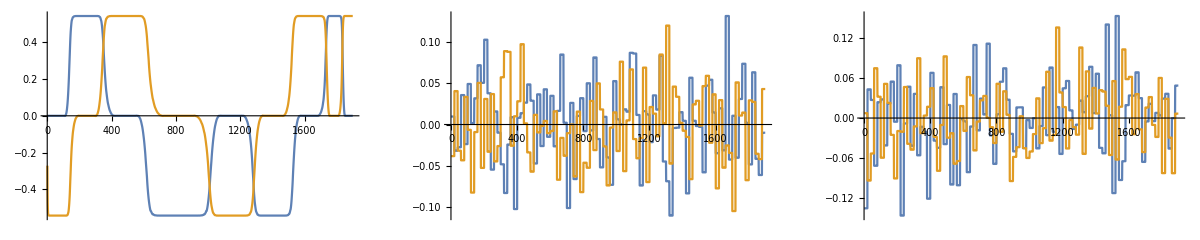

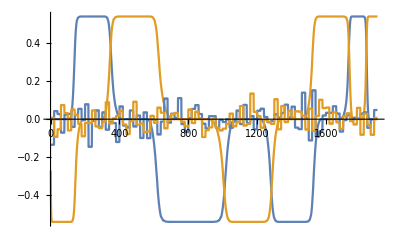

```mathematica
p1=ListLinePlot[Transpose[us]];
p2=ListLinePlot[Transpose[v]];
p3=ListLinePlot[Transpose[w]];
GraphicsRow[{p1,p2,p3}]
Show[p1,p3]
```

```mathematica
pose={14,6};
Xa=Table[pose=robotKine[pose,us⟦t⟧],{t,1,Length[us],1}];
pose={14,6};
guessedposes=Table[pose=robotKine[pose,v⟦t⟧+us⟦t⟧],{t,1,Length[us],1}];
Latinfont="Latin Modern Roman 10";
axesStyle={Black,AbsoluteThickness[0.7],FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Q=0.05^2*IdentityMatrix[2];
R=0.05^2*IdentityMatrix[2];
Manipulate[
P=0*IdentityMatrix[2];
t=Round[time/dt];
X={14,6};
landmarks={};
error=0;
filteredposes=Table[
X=robotKine[X,v⟦t⟧+us⟦t⟧];
P=P+dt*Q;
If[Mod[t,200]==0,
K=P.Inverse[P+R];
(*K=k*IdentityMatrix[2];*)
Z=Xa⟦t⟧+w⟦t⟧;
AppendTo[landmarks,Z];
X=X+K.(Z-X)];
error+=Norm[X-Xa⟦t⟧];
X,{t,1,Length[us],1}];
robot=With[{r=0.3},{EdgeForm[{Thickness[0.0013],Black}],Opacity[0.35],Disk[{0,0},r]}];
frame[t_]:=Graphics[{
Text[error,{10,11}],
(*Text[Grid[{{Style["K",Black,Italic,FontFamily->Latinfont,FontSize->20],Style[" = "<>ToString[K],Black,FontFamily->Latinfont,FontSize->20]}}],{10,12}],*)
Red,move2D[robot,Xa⟦1⟧],
Green,move2D[robot,Xa⟦t⟧],
Red,move2D[robot,filteredposes⟦t⟧],
(*Blue,move2D[robot,#]&/@Xa⟦200;;t-150;;250⟧,*)
(*Blue,move2D[robot,guessedposes⟦t⟧],*)
(*Green,move2D[robot,#]&/@landmarks,*)
(*Red,move2D[robot,filteredposes⟦t⟧],*)
Black,AbsoluteThickness[0.8],Line@Xa⟦1;;t⟧,
(*Blue,AbsoluteDashing[{5,2}],AbsoluteThickness[0.8],Line@guessedposes⟦1;;t⟧,*)
Red,AbsoluteDashing[{5,2}],Line@filteredposes⟦1;;t⟧
},PlotRange->{{0,22},{0,12}},Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->600,ImagePadding->{{20,25},{20,25}}];
(*Animate[frame[t],{t,Round[time/dt],Round[time/dt],1},AnimationRunning->False,DefaultDuration->10]*)
frame[t],(*{t,Round[time/dt],Round[time/dt],1},*)Control[{{k,0.,"K"},0,1,0.01, Appearance ->Large,ControlPlacement->Top}],LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->20],TrackedSymbols:>True]
```

```mathematica
Manipulate[
p1=Plot3D[PDF[BinormalDistribution[{0,0},{1,1},0],{x,y}],{x,-3,3},{y,-3,3},PlotPoints->55,Mesh->10,RegionFunction->Function[{x,y,z},x<xc],PlotRange->{{-3,3},{-3,3},{0,0.2}}, ColorFunction->"DarkRainbow"];
p2=Plot3D[PDF[BinormalDistribution[{0,0},{1,1},0],{x,y}],{x,-3,3},{y,-3,3},PlotPoints->55,Mesh->None,RegionFunction->Function[{x,y,z},x>=xc],PlotStyle->{Blue,Opacity[0.5]},PlotRange->{{-3,3},{-3,3},{0,0.2}}, ColorFunction->"DarkRainbow"];
Show[p1,p2],{xc,0,3,0.01},TrackedSymbols:>True]
```

```mathematica
frameGlobal={{RGBColor[Flatten[{#,0}]],Arrowheads[0.02],Arrow@{{0,0},#}}&/@IdentityMatrix[2]};
frameLocal={{RGBColor[Flatten[{#,0}]],Arrowheads[0.02],Arrow@{{0,0},#}}&/@(0.7*IdentityMatrix[2])};
Latinfont="Latin Modern Roman 10";
Manipulate[
R=RotationMatrix[α];
Graphics[{frameGlobal,GeometricTransformation[{frameLocal},R]},PlotRange->{{-2,2},{-2,2}}],{{α,0,Style["α",26]},-Pi,Pi,0.01,ImageSize->250},
ControlPlacement->{Left},Alignment->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 齐次变换矩阵的例子

```mathematica
gwe=poseToH[{x,y,θ}];
geo=poseToH[{Subscript[x, s],Subscript[y, s],Subscript[θ, s]}];
TraditionalForm[Simplify[gwe.geo]]
```

```mathematica
gew=Inverse@poseToH[{x,y,θ}];
gwo=poseToH[{Subscript[x, o],Subscript[y, o],Subscript[θ, o]}];
TraditionalForm[FullSimplify[gew.gwo]]
```

# 第五章 环境感知

## 栅格化图像

```mathematica
a=Import["C:\\Users\\q\\Desktop\\smile_face.png"];
d=ImageData@a;
```

```mathematica
c=Round[d[[1;;-1;;20,1;;-1;;20,1]]];
MatrixPlot[c]
```

```mathematica
t=Text[Style[Grid[c,Frame->All],FontFamily->"Latin Modern Roman 10"]];
Export["C:\\Users\\q\\Desktop\\1.jpeg",t];
```

## 一维卷积

```mathematica
ker={0.2,0.2,0.2,0.2,0.2};
(*ker={0.25,0.25,0.0,-0.25,-0.25};*)
(*ker={1,0,0,0,0};*)
n=10;
array0=Flatten[{ConstantArray[0.1,n],ConstantArray[1,n],ConstantArray[0.1,n],ConstantArray[1,n],ConstantArray[0.1,n]}];
array=array0;
convolve[ker_,data_]:=Module[{res},
res=Chop@ListConvolve[ker,data];
res=PadRight[res,Length[res]+2,res⟦-1⟧];
res=PadLeft[res,Length[res]+2,res⟦1⟧];
res
];
Manipulate[
res=convolve[ker,array];
Table[res=convolve[ker,res],{k}];
ListPlot[{array0,res},AspectRatio->0.4,Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"data","value"},ImageSize->750,ImagePadding->{{20,45},{0,28}},PlotStyle->{Black,Red},PlotRange->{{0,Length[array]+2},{-0.5,1.2}},Filling->Axis,FillingStyle->Directive@{Black,AbsoluteThickness[0.5]}(*,Joined->True*)]
,Control[{{k,0,"k"},0,100,1, Appearance ->Large,ControlPlacement->Top}],LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->20],TrackedSymbols:>True]
```

## 二维卷积

```mathematica
n=7;
m=RandomInteger[{0,0},{n,n}]/. 0->-1;
text=Text[Style[Grid[m,Frame->All,Alignment->{Center,Center},Spacings->{1,1},Dividers->Lighter[Gray,0.4]],FontSize->10,FontColor->Blue,FontFamily->"Helvetica"],{0,0}];
grid=Graphics[{text},ImageSize->160,AspectRatio->1];
texture=grid;
textureDim=ImageDimensions@grid;
Graphics3D[{(*Specularity[White,20],*)Lighting->"Neutral",Antialiasing->True,Texture[Rasterize[texture,ImageResolution->300]],
EdgeForm[Directive[AbsoluteThickness[2],White]],FaceForm[Directive[White]],
Polygon[{{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}](*Polygon[{2,2,2} #/textureDim[[2]]&/@{{0,textureDim[[1]],0},{textureDim[[2]],textureDim[[1]],0},{textureDim[[2]],0,0},{0,0,0}},VertexTextureCoordinates->-1 {{0,0},{0,1},{1,1},{1,0}}]*)},Boxed->False,ImageSize->{314.709,255.736},ImageSizeRaw->Automatic,ViewPoint->{-1.78703,0.943471,2.71411},ViewVertical->{-0.211294,0.939,0.271357}]
```

```mathematica
d=-Graphics-;
d2=GaussianFilter[d,10];
Erosion[ColorNegate@EdgeDetect[d2,10],DiskMatrix[2]];
LaplacianFilter[d,10];
```

## 批量归一化

```mathematica
batchnorm=NetInitialize@BatchNormalizationLayer["Input"->9];
batchnorm[{1,2,3,4,5,6,7,8,9}]
```

{0.9995,1.999,2.9985,3.998,4.9975,5.997,6.9965,7.996,8.9955}

## Yolo

```mathematica
Manipulate[
Plot[{LogisticSigmoid[x],a*LogisticSigmoid[x]-(a-1)0.5},{x,-10,10},PlotRange->{{-10,10},{-2,3}}],{{a,0},-5,5,0.01},TrackedSymbols:>True]
```

```mathematica
N[(√101-√100)^2]
N[(√11-√10)^2]
Log[100/101.]
Log[10/11.]
```

## 激活函数的图像

#### Sigmoid、Tanh、Relu激活函数

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Manipulate[Plot[{LogisticSigmoid[w*x+b],Tanh[w*x+b],Ramp[w*x+b]},{x,-4,4},PlotStyle->{Red,Blue,Black},PlotRange->{{-4,4},{-1.5,2.5}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},AspectRatio->Automatic,Ticks->{Range[-4,4], Range[-1,2]}],{{w,1},-10,10,0.01},{{b,0},-10,10,0.01}]
```

```mathematica
D[LogisticSigmoid[x],x]
D[Tanh[x],x]
D[Ramp[x],x]
```

(1-LogisticSigmoid[x]) LogisticSigmoid[x]

Sech[x]^2

Piecewise[{{0, x<0}, {1, x>0}, {Indeterminate, True}}]

```mathematica
Plot[{(1-LogisticSigmoid[x]) LogisticSigmoid[x],Sech[x]^2,If[x<=0,0,1]},{x,-4,4},PlotStyle->{Red,Blue,Black},PlotRange->{{-4,4},{-1.5,2.5}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},AspectRatio->Automatic,Ticks->{Range[-4,4], Range[-1,2]}]
```

## Focal loss损失函数的图像

```mathematica
Manipulate[Plot[-a (1-x)^g*Log[x],{x,-1,5},PlotRange->{{0,1},{-1,4}}],{a,0,10,0.01},{g,0,10,0.01},TrackedSymbols:>True]
```

## 计算机视觉特征点

```mathematica
i=-Graphics-;
ImageKeypoints[i,Method->"AKAZE",MaxFeatures->50];
HighlightImage[i,%]
```

## PointPillars点云存储顺序

```mathematica
pic=Import["C:\\Users\\Administrator\\Desktop\\3.jpg"];
pic2=Rasterize[pic,RasterSize->150]
data=ImageData@pic2;
data//Dimensions;
data2=Flatten[data,1];
data3=ArrayReshape[RandomSample@data2,Dimensions[data]];
Image[data3]
```

```mathematica
file =BinaryReadList["D:\\DurLAR_20211209_S_LIDAR\\data\\0000000100.bin","Real32"];
file ;
```

```mathematica
pointCloud=Import["H:\\Mathematica\\Mobile Robot\\PointCloud\\000000.ply","VertexData"];
Graphics3D[{AbsolutePointSize[1.3],Point[pointCloud]},(*PlotRange->{{10,170},{170,220},{-2,8}},*)(*PlotRange->{{-50,170},{-160,70},{-2,8}},*)Axes->False,Boxed->False,ImageSize->1000];
```

```mathematica
pts=duck⟦3,1⟧;
pts=pts⟦1;;-1;;2⟧;
Graphics3D[{Yellow,Sphere[pts,0.01]}];
```

这里存储了兔子点云数据rabbit data

```mathematica
rabbitpoints={{-0.0369122,0.127512,0.00276757},{-0.0457707,0.130327,0.00306785},{-0.0708847,0.149834,0.0388672},{-0.00331557,0.130403,0.0212208},{-0.0211979,0.1272,0.00915278},{-0.0265255,0.12592,0.00874866},{0.0339261,0.112038,0.0269672},{0.0376485,0.110455,0.0145481},{-0.0259368,0.111118,0.0379115},{0.027952,0.120939,0.0215377},{-0.0628308,0.155987,-0.0150105},{0.0390029,0.106711,0.0215202},{0.0447976,0.0950477,0.00866471},{-0.0330636,0.173619,-0.0031267},{-0.0808069,0.136243,0.0495014},{-0.0705086,0.12445,0.0526685},{0.00874873,0.131225,0.0145345},{0.0401015,0.106711,0.00874166},{0.0379483,0.100145,-0.00827134},{-0.0906538,0.137201,0.0207305},{-0.0841655,0.110667,0.0275273},{-0.0705214,0.156214,0.0144536},{-0.083872,0.15212,0.0282652},{0.00305028,0.12432,0.0332425},{0.00870828,0.124165,0.0330348},{-0.0328896,0.12613,0.00300653},{-0.0506302,0.143065,0.0150611},{-0.0757863,0.13637,0.050172},{-0.0027191,0.128962,0.0264678},{-0.0460961,0.125118,0.0263142},{-0.0785104,0.0942728,-0.0109192},{0.0216915,0.125373,0.0211452},{-0.0888469,0.124305,0.00237041},{0.040386,0.100825,-0.00303043},{-0.0884145,0.117791,0.00268555},{-0.0319074,0.177421,-0.00491879},{-0.0765825,0.143224,0.0455148},{-0.0209748,0.112544,0.0388613},{-0.020836,0.179425,-0.0221622},{-0.0377039,0.167987,-0.0130391},{-0.0331765,0.12681,0.00839958},{0.00893926,0.127114,0.0292916},{-0.044944,0.131083,0.0147963},{-0.0266041,0.12515,0.00282384},{0.0144285,0.12328,0.0319185},{0.019244,0.122284,0.0308314},{-0.0390225,0.167317,0.00215527},{-0.08808,0.129976,0.00206377},{-0.0537203,0.142608,0.0266058},{0.043095,0.0980072,0.0191617},{0.0432138,0.100117,0.00866473},{0.0415448,0.0944954,0.0275695},{-0.0578726,0.155337,0.0149245},{-0.0231577,0.157375,-0.0046304},{-0.0683123,0.145735,0.0420568},{-0.0708351,0.142847,0.0451248},{-0.070664,0.0642894,0.0209789},{-0.0761519,0.130581,0.0525324},{-0.0640036,0.161784,-0.0208118},{-0.0706461,0.155711,0.00252406},{-0.0924366,0.118434,0.0399838},{-0.0635349,0.156052,0.0148814},{0.0282675,0.118192,0.0274382},{0.0392736,0.0938857,-0.00915453},{-0.0695973,0.164844,-0.0174846},{-0.00892354,0.123904,0.0330319},{0.0269099,0.0942476,0.0444911},{-0.0146258,0.162377,-0.0144398},{-0.0450983,0.167072,0.00289327},{-0.0761536,0.172742,-0.0384391},{-0.0858274,0.105458,0.00472318},{0.0370431,0.110443,0.0207229},{0.0321593,0.0994027,0.0380657},{-0.075287,0.146433,0.0428582},{-0.0395145,0.171107,0.000531747},{-0.0839586,0.11215,0.00148754},{0.0446848,0.0883378,0.0216285},{0.0161783,0.127819,0.0220535},{-0.00251635,0.0397232,0.0474087},{0.00303163,0.0406968,0.0460422},{-0.0143059,0.128197,0.00333856},{-0.0526117,0.155596,0.0109972},{-0.0332043,0.17776,-0.00906223},{0.0394391,0.106654,0.00306577},{-0.0923799,0.1249,0.0327641},{0.0454681,0.0882959,0.0146642},{-0.0274495,0.179802,-0.00925837},{-0.072504,0.146297,0.0429682},{-0.0579959,0.129793,0.0383118},{0.043117,0.0923689,0.0251649},{-0.00865718,0.130323,0.0149721},{-0.0141304,0.129188,0.0147431},{-0.0707877,0.15583,0.00921954},{-0.00952731,0.127041,0.0281475},{-0.0646289,0.153404,0.0329146},{-0.0706939,0.15347,0.0328596},{0.0208126,0.118434,0.0336393},{-0.0396566,0.173008,-0.00299705},{-0.0442176,0.170815,-0.00391429},{-0.0582565,0.0395149,0.0457796},{-0.0523033,0.0401501,0.04623},{-0.0760211,0.161274,-0.0145891},{-0.0693983,0.163016,-0.0140293},{0.0399663,0.106491,0.014952},{0.041536,0.0950084,-0.00475737},{-0.0470079,0.163779,0.00528295},{-0.0402546,0.161678,0.00298655},{-0.0386569,0.0389805,0.0441153},{-0.0704175,0.166991,-0.0216976},{-0.0254201,0.0886622,0.0503827},{-0.0886334,0.137429,0.00876953},{-0.014179,0.12627,0.0266417},{-0.0360017,0.17408,-0.0118959},{-0.0886251,0.0937834,0.00823534},{-0.0648672,0.155874,-0.00891497},{-0.0704508,0.137752,-0.00774011},{-0.0750154,0.166247,-0.0219558},{0.0299465,0.114869,0.0300239},{0.0398138,0.0998788,0.0273101},{-0.015242,0.111698,0.0407424},{-0.0700387,0.118219,0.0524379},{0.0149973,0.112399,0.0386082},{-0.036487,0.171225,0.000545037},{-0.0641664,0.118551,-0.00968333},{-0.071817,0.166979,-0.0463822},{-0.0913559,0.14534,0.0246937},{0.00903703,0.112569,0.0396571},{0.0324674,0.0997396,-0.0141603},{0.0417911,0.101845,0.00188609},{0.00302992,0.112517,0.0415434},{-0.0650368,0.148485,0.0382561},{-0.0706519,0.13063,0.0502497},{-0.0144471,0.128935,0.00903509},{0.00292575,0.131541,0.00912318},{-0.0625682,0.151125,0.035875},{0.0349829,0.113328,0.0214487},{0.021327,0.0385664,0.0392992},{0.0145125,0.093771,0.0501571},{-0.00923752,0.112849,0.0413907},{0.0415329,0.100906,0.0210277},{0.0422859,0.101486,0.0146614},{-0.0773783,0.112839,-0.00448759},{-0.078035,0.137641,-0.00517379},{0.00873437,0.106347,-0.0202193},{0.0090324,0.13035,0.0211569},{0.00301322,0.130902,0.0206741},{-0.00286342,0.13115,0.0147367},{-0.0391578,0.12569,0.0207996},{-0.0205725,0.123523,0.0265579},{-0.0644194,0.155634,0.00928477},{-0.0463385,0.131411,0.0207671},{-0.0532034,0.0439067,0.044658},{-0.00297651,0.131046,0.00884967},{-0.089664,0.137755,0.0263925},{-0.00888731,0.124273,-0.00880284},{-0.0460971,0.0385107,0.0446891},{-0.0649255,0.178874,-0.0579325},{-0.0329347,0.124601,0.0211235},{-0.0831301,0.149901,0.0334123},{-0.0895652,0.093948,0.0149303},{-0.0328901,0.124518,-0.00282055},{-0.0845271,0.106161,0.00204328},{-0.0469341,0.155816,0.00872921},{0.0206202,0.123943,0.0267275},{-0.026256,0.117499,0.0321672},{-0.021392,0.118632,0.0336445},{-0.0195069,0.116132,0.0368525},{-0.0761618,0.118382,0.0520923},{0.00889281,0.0395765,0.0451727},{-0.0534736,0.159548,0.00753828},{-0.0469464,0.161226,0.00680216},{-0.0574886,0.154862,0.0204748},{0.0317199,0.117635,0.0202007},{0.0378683,0.105514,-0.00259159},{-0.0811847,0.137693,-0.00253994},{-0.0764348,0.124515,0.0528345},{0.0343816,0.106104,-0.00900254},{0.0457922,0.088316,0.00867097},{-0.0703288,0.0944195,-0.0159143},{-0.0756048,0.0937947,-0.0135536},{-0.058657,0.156369,0.0093256},{-0.0637335,0.153848,0.00222718},{-0.0777278,0.0960024,0.0363437},{-0.0868519,0.136556,0.00309926},{-0.0455299,0.0432404,0.0432162},{-0.0402011,0.045749,0.0408051},{-0.0654123,0.160403,-0.0149066},{-0.0318898,0.0387174,0.0510004},{-0.0267997,0.0453977,0.0509311},{-0.0271043,0.0396972,0.0535379},{-0.0215575,0.0460868,0.0517209},{-0.0143078,0.0445295,0.0504368},{-0.00981594,0.043264,0.0493162},{-0.00348436,0.044054,0.0472086},{0.009577,0.0458139,0.0465877},{0.02048,0.111086,0.0379569},{-0.0141831,0.128547,0.0200007},{-0.0526702,0.144108,0.0210347},{-0.0634838,0.17384,-0.0527131},{-0.0366553,0.171999,-0.0125745},{-0.0525548,0.131228,0.0328277},{-0.0659567,0.132023,0.0442925},{-0.0921726,0.11832,0.0267606},{0.0452792,0.0882737,0.00268175},{-0.00305651,0.112889,0.0417789},{-0.0451955,0.161396,-0.00871567},{-0.0402914,0.160933,-0.0115368},{-0.0521414,0.0701165,0.0389584},{-0.0383315,0.093604,-0.0232581},{-0.0690556,0.137374,0.046352},{-0.0695996,0.167401,-0.0516299},{-0.00246047,0.124102,0.0337609},{-0.0398624,0.128204,0.00299348},{-0.0753331,0.149032,0.0395625},{-0.0701432,0.160618,-0.00917801},{-0.0589378,0.0440425,0.0434222},{-0.0207164,0.126445,0.00312493},{-0.00850666,0.0467286,0.0481052},{0.00300323,0.0450308,0.0469911},{-0.0802174,0.148665,0.0379438},{-0.0819961,0.130698,0.0513437},{0.00273088,0.106333,-0.0209927},{-0.0757273,0.0885687,-0.0138399},{-0.0698477,0.0882875,-0.0167823},{-0.0668508,0.159243,-0.0102161},{-0.0226988,0.0885773,0.0536309},{-0.00281419,0.0990077,0.0505614},{0.0452902,0.0696213,0.0253974},{-0.0525629,0.0472823,0.040482},{-0.046959,0.0466581,0.0408127},{-0.0691348,0.156682,-0.00276369},{-0.0897599,0.150073,0.0220744},{-0.0702883,0.155637,0.0263654},{-0.0765031,0.154893,0.0266005},{-0.00804843,0.0987379,0.0505998},{0.0300791,0.11567,-0.00430465},{-0.0923054,0.117757,0.0334441},{-0.0331192,0.0449511,0.0462474},{-0.0337794,0.113308,0.034612},{-0.0521291,0.113769,0.0349566},{0.0437636,0.0825382,-0.0027974},{-0.0202819,0.126016,0.0210507},{0.0327872,0.043925,0.0295904},{-0.0453372,0.155266,-0.0075525},{-0.0284609,0.173987,-0.0175958},{0.0268448,0.0881755,-0.0223077},{-0.0308231,0.0923023,-0.0246377},{-0.0899732,0.149975,0.0141115},{0.0381804,0.105121,0.0266947},{0.00842001,0.12907,0.0258154},{-0.0266549,0.0942999,-0.0265555},{-0.0279896,0.0475815,0.0485532},{-0.0150037,0.048073,0.0483203},{-0.00298993,0.0473817,0.0491102},{0.00376754,0.0477551,0.0502037},{0.00748504,0.0473851,0.0493363},{-0.0581651,0.149751,0.032858},{-0.0720688,0.136456,0.0490662},{-0.0810638,0.0939541,-0.0082617},{0.0380863,0.0458646,0.0307423},{-0.0253234,0.182998,-0.0108168},{-0.0230508,0.183235,-0.0110157},{0.00323317,0.129146,0.0263855},{-0.0626125,0.149788,-0.00343342},{-0.0591471,0.0466998,0.0395843},{-0.0353862,0.0471292,0.0414241},{-0.0194948,0.0486404,0.0485565},{-0.00849455,0.0521633,0.0517688},{-0.00296485,0.051429,0.0527827},{0.00279019,0.0517664,0.0528352},{0.00904034,0.0517165,0.051222},{0.0443839,0.0943042,0.00268377},{-0.0886145,0.111113,0.0148415},{-0.0885219,0.144027,0.0329221},{0.0440719,0.0937787,0.0206165},{0.0436531,0.0980341,0.0146596},{-0.0650976,0.153799,-0.00285808},{-0.0517297,0.0490759,0.0371355},{-0.0331222,0.0518259,0.0385377},{-0.0377352,0.127448,0.0152358},{-0.00906608,0.100701,0.0460122},{-0.0410683,0.128416,0.0134054},{-0.0712056,0.158724,-0.00521868},{-0.0266313,0.0501544,0.044695},{-0.0211065,0.0519946,0.0455753},{-0.0168667,0.0505241,0.0476889},{-0.0147601,0.0527687,0.050103},{-0.0626395,0.149972,-0.00897733},{-0.090861,0.124732,0.00627835},{-0.0255786,0.0923499,-0.0315595},{-0.0709738,0.172947,-0.052768},{-0.0588974,0.143232,-0.00327646},{-0.0943643,0.12436,0.0216467},{0.0337044,0.112449,-0.00269877},{-0.0515051,0.136557,0.0263185},{-0.00886593,0.121199,0.0360577},{-0.061729,0.155665,-0.0259512},{-0.0862637,0.10567,0.0206042},{-0.0895584,0.138606,0.032689},{-0.0268168,0.123904,0.0208113},{0.0341937,0.0515433,0.033081},{0.0401268,0.0512743,0.0322702},{0.0449306,0.0526595,0.0319582},{-0.0405348,0.117168,0.0319438},{-0.0636902,0.155546,-0.0390642},{0.0278663,0.100401,0.0410064},{-0.0275828,0.179275,-0.0157605},{-0.0758871,0.0942302,0.0383961},{0.0138371,0.129201,0.0203961},{-0.0152723,0.0998429,0.0451638},{-0.00916763,0.129718,0.0206646},{-0.0512444,0.0516901,0.0334801},{-0.0461563,0.0523184,0.0379981},{-0.0410001,0.05272,0.0393793},{-0.0270993,0.0526642,0.0393104},{0.0434924,0.0931097,-0.00154028},{-0.0823819,0.112683,0.045427},{-0.092066,0.118055,0.00909937},{-0.00448884,0.121713,0.0362976},{0.0147346,0.129423,0.0143146},{-0.0158113,0.161888,-0.00973584},{-0.0778838,0.149704,-0.00337488},{-0.0865357,0.12477,-0.00166991},{0.0153656,0.126058,0.0275381},{-0.0388913,0.123761,0.0249778},{-0.0390351,0.121238,0.0283673},{-0.0324963,0.120237,0.0283344},{-0.0149052,0.12311,0.0316417},{-0.0582873,0.117688,0.0386719},{-0.0626536,0.161861,-0.0264031},{-0.0818147,0.141639,0.0444825},{0.0350734,0.100071,0.0345975},{0.0311856,0.11215,0.0310216},{-0.0335778,0.11743,0.031458},{-0.059637,0.153475,0.031348},{-0.0481256,0.0536625,0.0362191},{-0.059026,0.156388,0.00269852},{-0.0211187,0.0578754,0.0461125},{-0.082738,0.124721,0.050554},{-0.0466997,0.11363,0.0348133},{-0.0107262,0.179662,-0.0277472},{0.0347725,0.0894441,-0.0170339},{-0.0891825,0.100351,0.0148945},{0.0257275,0.122894,0.0207337},{-0.0883949,0.100277,0.00841226},{-0.0649858,0.155518,0.0263367},{-0.0768402,0.154073,0.00257877},{-0.0576877,0.154146,0.0262123},{-0.0266966,0.125729,0.0145923},{-0.076376,0.155782,0.0208875},{-0.0763295,0.167188,-0.039594},{-0.0771877,0.100229,-0.0103313},{-0.0153681,0.0590839,0.0519909},{-0.010206,0.0576345,0.0535443},{-0.00350044,0.0578672,0.0543757},{0.00300818,0.0568916,0.0538692},{0.0088308,0.0580497,0.0529859},{0.0410915,0.0820775,-0.00893411},{0.0395449,0.0576373,0.0318985},{-0.0762443,0.139336,0.0484763},{-0.0324306,0.120379,-0.00955344},{-0.0194451,0.0881559,0.0557639},{-0.074787,0.159471,-0.00898201},{-0.0639935,0.15611,0.0210031},{-0.0762438,0.153101,0.0322442},{-0.00876679,0.128727,0.025102},{0.0282216,0.112237,-0.00983067},{-0.0451341,0.0593225,0.0387559},{-0.0405005,0.0579499,0.040202},{-0.033993,0.0584028,0.038704},{-0.0272756,0.0585468,0.0382285},{-0.0248608,0.122913,0.0245429},{-0.0825276,0.154355,0.0206132},{-0.00884271,0.129403,0.00305159},{0.0207587,0.126654,0.0147646},{-0.0394868,0.173351,-0.00839443},{-0.028421,0.114019,0.0347746},{-0.0193575,0.122009,0.0306737},{-0.0691626,0.161675,-0.0514614},{-0.0516736,0.15006,0.0148119},{-0.0156325,0.120151,0.0349054},{0.0467454,0.0582319,0.0314404},{-0.0770165,0.0685425,0.0147863},{-0.00967101,0.173225,-0.0264945},{-0.0213141,0.184813,-0.0151112},{-0.0766524,0.0882188,0.0382876},{-0.0540219,0.0521463,0.0110698},{-0.0219451,0.126821,0.0155536},{-0.0820391,0.153392,0.0264506},{-0.0213183,0.124468,-0.00290836},{-0.0268364,0.123465,-0.00321538},{-0.0312035,0.177796,-0.0133521},{-0.00749945,0.0598042,0.0553302},{-0.00108951,0.0601245,0.0554892},{0.00280202,0.0599746,0.0555283},{-0.051797,0.118119,0.033678},{0.00302464,0.131618,0.0149353},{0.0446005,0.0942619,0.0151198},{-0.0880636,0.111855,0.00852285},{-0.0704321,0.144096,-0.0148369},{-0.0820967,0.0943634,0.0322765},{-0.0269642,0.120812,0.0275676},{-0.0540164,0.149968,0.0253393},{-0.0800337,0.0995053,-0.00770139},{0.00922138,0.12038,0.0360924},{0.00286056,0.117968,0.0387331},{-0.0936229,0.118494,0.0206524},{-0.0409923,0.113229,0.035109},{-0.0822185,0.154488,0.0146661},{-0.0625956,0.155202,-0.0329876},{-0.0462511,0.124621,-0.00898124},{-0.0220336,0.160676,-0.00426008},{-0.065621,0.172767,-0.0466049},{-0.0762614,0.155884,0.0148687},{-0.0644988,0.149044,-0.0265159},{-0.0581979,0.0593456,0.0210895},{-0.0335439,0.122618,0.0254024},{-0.0826578,0.153434,0.00921403},{-0.049999,0.132417,0.0286961},{0.0088217,0.131096,0.00864908},{-0.0154842,0.0644282,0.0533754},{-0.00871951,0.065015,0.0556827},{-0.00324815,0.0640003,0.0562816},{0.00292601,0.0643094,0.0563956},{0.00738462,0.0651614,0.0553402},{-0.0143174,0.116971,0.037836},{-0.00299223,0.118083,0.0390751},{-0.00864301,0.117816,0.0385662},{-0.0532884,0.0571719,0.0206631},{-0.0882588,0.100387,0.0210097},{-0.0324377,0.099703,-0.0227313},{0.0425072,0.0603725,0.0302275},{0.0523383,0.0580401,0.0290457},{0.0413612,0.0877503,-0.00929235},{-0.0581547,0.0620148,0.0270981},{-0.0530328,0.0590503,0.0266933},{-0.0477227,0.135526,0.0148654},{0.00323512,0.0983053,0.0504424},{0.0150627,0.119642,0.034806},{-0.0453373,0.0643061,0.0391142},{-0.0394097,0.0644278,0.0414133},{-0.033068,0.0642666,0.0396407},{-0.0270237,0.0644489,0.0395335},{-0.0881604,0.149479,0.0268507},{-0.0640727,0.143434,-0.00894036},{0.00286033,0.121151,0.036139},{-0.0827306,0.138152,0.0466993},{-0.00261511,0.127006,0.030132},{0.0355841,0.108498,-0.00452523},{0.0219203,0.114136,0.0356941},{-0.0379555,0.161954,-0.0128021},{-0.0526362,0.0643632,0.0340621},{0.025874,0.123374,0.0143811},{-0.0451406,0.131184,0.00901599},{-0.075778,0.155361,-0.00310678},{-0.0739145,0.156437,-0.0274945},{-0.0833056,0.100778,-0.00354288},{-0.0767099,0.173942,-0.0452732},{0.00846106,0.116985,0.038033},{-0.0200899,0.184788,-0.020546},{-0.046571,0.120413,0.0285524},{-0.0515313,0.123718,-0.0088569},{0.0212116,0.105804,-0.0171101},{-0.0938613,0.124487,0.0151416},{0.0414591,0.064577,0.0290352},{0.0466725,0.0643471,0.0285539},{0.0526423,0.0634018,0.0283831},{-0.0468141,0.168322,-0.00285433},{-0.0869152,0.0944156,0.00293118},{-0.0773713,0.161559,-0.0267238},{-0.0396095,0.126677,-0.00334699},{-0.0271315,0.0764239,0.0455715},{-0.0587953,0.107012,-0.0177177},{-0.0748314,0.11156,-0.00720996},{-0.0642623,0.0888181,-0.018733},{-0.0325172,0.0881157,-0.0255424},{0.00325654,0.0700086,0.0561047},{0.0103151,0.0636713,0.0537558},{0.0432701,0.0979967,0.00267804},{-0.0708223,0.156244,0.021207},{-0.0584176,0.0702277,0.0384322},{-0.0703207,0.112305,-0.00963846},{-0.0581653,0.0881983,-0.0208369},{-0.0443038,0.0877156,-0.0218942},{-0.0488091,0.0660127,0.0373959},{0.00269411,0.126911,0.030114},{0.0239692,0.12105,0.0288706},{-0.0469203,0.117468,0.0314407},{-0.091552,0.143361,0.0201623},{-0.0907563,0.143859,0.0263089},{-0.0495713,0.144022,0.00976642},{-0.0770934,0.15583,-0.0147903},{-0.0868322,0.105634,0.00887573},{-0.082848,0.131648,-0.00299747},{-0.0384249,0.106407,-0.0201393},{-0.0823953,0.118841,-0.00336022},{-0.0102333,0.0876697,-0.0375101},{-0.00789361,0.089842,-0.0363492},{-0.0579097,0.111769,-0.0161856},{0.0140074,0.105793,-0.0193841},{-0.00328561,0.105435,-0.0225198},{-0.0409613,0.070972,0.0419904},{-0.033501,0.0710512,0.0409793},{-0.0272732,0.0701361,0.0410332},{-0.0161963,0.127121,0.0228897},{-0.0190644,0.127936,0.0133818},{-0.0149926,0.0694778,0.0545159},{-0.00932719,0.0707313,0.0562936},{-0.002994,0.0710941,0.0575426},{0.00838831,0.0714267,0.0556585},{0.0102531,0.0693533,0.0547665},{-0.0323939,0.153399,-0.00240332},{0.0435981,0.0881514,0.0254203},{-0.0586529,0.124882,-0.00781093},{-0.0204287,0.107045,-0.022046},{-0.0382961,0.0879422,-0.0229335},{-0.081573,0.113394,-0.00173083},{-0.0380811,0.154778,-0.00889149},{-0.00212588,0.0889926,-0.0354677},{0.00904065,0.100193,-0.0222794},{-0.0467068,0.0700493,0.0405769},{-0.0779974,0.151244,0.0352264},{0.0149019,0.116126,0.0367849},{-0.07603,0.106301,-0.0087688},{-0.0885261,0.137839,0.0393964},{-0.0703112,0.131278,-0.00857724},{0.0419377,0.0703605,0.0288832},{0.0514194,0.0684326,0.0256968},{-0.0922548,0.124813,0.0393757},{0.0135035,0.128105,0.0250558},{-0.0704618,0.125421,-0.00881334},{-0.0703931,0.118731,-0.00840961},{-0.0719685,0.106305,-0.0114493},{-0.0646972,0.161498,-0.0573125},{0.0463693,0.0715128,0.0216754},{-0.0538246,0.153497,0.0152346},{-0.0142869,0.0724666,0.0554243},{-0.0394057,0.118512,-0.01336},{-0.0280509,0.0880065,-0.0330858},{-0.00957701,0.168254,-0.0212321},{-0.0445856,0.167324,-0.00782662},{-0.0513101,0.161594,-0.00355965},{-0.0702356,0.179304,-0.0569867},{-0.0644695,0.168402,-0.0398946},{-0.0089459,0.130139,0.00911776},{0.00219503,0.0880369,-0.0342201},{-0.0268891,0.16726,-0.0174204},{-0.0525985,0.155054,-0.00368706},{-0.0761618,0.131736,-0.00696723},{-0.0759576,0.07099,0.0265672},{-0.00875341,0.10588,-0.02285},{-0.0519242,0.1493,-0.00277595},{-0.016371,0.18465,-0.0214272},{-0.020548,0.0705632,0.0520411},{-0.0813371,0.120073,0.049533},{-0.0625087,0.149934,-0.0150319},{-0.0831098,0.10651,0.0273461},{-0.011119,0.163582,-0.018751},{-0.00291057,0.101147,0.0456419},{-0.0635467,0.0660523,0.0318653},{-0.0511979,0.0873878,-0.0217212},{-0.0530335,0.0740367,0.0417219},{-0.0465007,0.0756701,0.0421325},{-0.022314,0.0760359,0.0530306},{-0.0151351,0.0764056,0.0563566},{-0.00900601,0.0766621,0.0575852},{-0.00299732,0.0767339,0.0584651},{0.00347424,0.0769755,0.0565905},{0.00860763,0.0767538,0.0557293},{-0.0271239,0.156216,-0.00302734},{-0.0633091,0.16738,-0.0580906},{-0.0873943,0.144225,0.00902371},{-0.0626891,0.162297,-0.0470925},{0.0370111,0.110397,0.00265294},{-0.0744006,0.144062,-0.00864565},{-0.0244124,0.183841,-0.0135068},{-0.0803381,0.0715473,0.0150483},{-0.0644528,0.0761561,0.040638},{-0.0588413,0.0753794,0.0421022},{-0.0524294,0.077372,0.0433357},{-0.0484981,0.0769334,0.043281},{-0.0414954,0.0773856,0.0429005},{-0.0395008,0.0754808,0.0425134},{-0.033488,0.0764759,0.0414605},{-0.0627838,0.162163,-0.0530538},{0.0381456,0.0881056,-0.0138675},{-0.0642837,0.0396418,0.039624},{-0.0526672,0.121335,-0.010917},{-0.0738104,0.162942,-0.037093},{-0.0490869,0.13938,0.00889895},{-0.0495771,0.166027,-0.00171113},{-0.0709736,0.161609,-0.0450808},{0.0251847,0.12195,0.0254854},{-0.0193615,0.0781018,0.0558163},{-0.0265458,0.120645,-0.00911332},{-0.061796,0.155741,-0.0207923},{-0.082476,0.110295,0.0324103},{-0.0691674,0.156314,-0.050857},{-0.0622848,0.16236,-0.0396288},{-0.088248,0.113803,0.0264606},{-0.0575392,0.0787026,0.0436363},{-0.0298439,0.0782596,0.0421168},{-0.0677617,0.0876701,0.0434928},{-0.0921939,0.131884,0.015227},{-0.0878987,0.111742,0.0209206},{-0.049353,0.139298,0.0147955},{-0.0327071,0.173321,-0.0149209},{-0.0866298,0.152851,0.0149144},{-0.0779646,0.100025,0.035185},{-0.0935537,0.118404,0.0151524},{-0.084908,0.10801,0.0228537},{-0.0210677,0.0821213,0.0562096},{-0.0149957,0.082187,0.0572635},{-0.00899671,0.0822178,0.0576875},{-0.00299966,0.0822055,0.0574653},{0.0034748,0.0817533,0.0567544},{0.00824833,0.082992,0.0556315},{0.0102414,0.0812949,0.0546523},{-0.0398496,0.123966,-0.00878898},{-0.092257,0.124769,0.00902091},{-0.0436728,0.126191,0.0209533},{-0.0820425,0.105873,-0.00271871},{-0.0663016,0.0807623,0.0424437},{-0.0639939,0.0836688,0.0439754},{-0.058539,0.0825906,0.0439671},{-0.0521209,0.0822523,0.0446262},{-0.0467559,0.0828569,0.0439458},{-0.0424962,0.0810729,0.0423266},{-0.0404903,0.0830123,0.0430984},{-0.0365108,0.0825773,0.0434355},{-0.032204,0.0824171,0.0421121},{-0.0864005,0.152981,0.0204492},{-0.0235661,0.115415,0.0353667},{-0.0764871,0.111685,0.0461598},{-0.0763895,0.14977,-0.00829972},{-0.0754801,0.161855,-0.0327796},{-0.0285733,0.0828247,0.0462702},{-0.0862819,0.100797,0.0028483},{0.021088,0.08242,0.0504086},{-0.0801892,0.143128,-0.00230055},{0.00844098,0.124407,-0.00878569},{0.0147552,0.0825883,0.0529115},{-0.061995,0.161169,-0.032654},{-0.0807571,0.1525,0.0307996},{-0.00295953,0.130272,0.00279699},{-0.0153619,0.0884791,0.0565599},{-0.00899729,0.0878977,0.0570287},{-0.00299611,0.0880658,0.0568489},{0.00301457,0.0885291,0.0562756},{0.00834267,0.0873808,0.0555541},{-0.00897481,0.0941651,-0.0338408},{0.0314278,0.11673,0.0250113},{-0.0760602,0.155337,0.0093949},{0.0257808,0.116776,-0.00728909},{-0.0646577,0.0882843,0.0447113},{-0.058996,0.0882997,0.0449149},{-0.0529958,0.0883132,0.0451395},{-0.0465421,0.0881579,0.0443187},{-0.0404961,0.0876863,0.0430941},{-0.0331792,0.0885648,0.04366},{-0.0280482,0.0879652,0.046363},{0.0150626,0.0881784,0.0517745},{0.0205955,0.087113,0.0492325},{-0.0702712,0.0823874,0.0409431},{-0.0296926,0.0896882,-0.0286839},{-0.0236137,0.179242,-0.0115629},{-0.0809391,0.100029,0.0323433},{-0.0928336,0.130683,0.0207107},{-0.0761771,0.156201,-0.0204165},{0.0146577,0.129396,0.00843576},{0.0104845,0.089766,0.0542005},{-0.072579,0.161253,-0.0389447},{-0.0322741,0.110391,-0.0184574},{-0.0550172,0.150108,0.027792},{-0.071635,0.0883254,0.0414652},{-0.0424904,0.0895336,0.0426086},{0.0207945,0.0897491,0.0484315},{0.0273189,0.118845,-0.00265658},{0.0285218,0.121112,0.0162366},{-0.00899735,0.0930598,0.0559298},{-0.00291176,0.118727,-0.0144021},{-0.0885191,0.113233,0.0327948},{-0.0713744,0.0938304,0.0415269},{-0.0641029,0.0935514,0.0439488},{-0.0584965,0.0944146,0.0446213},{-0.0515853,0.0939836,0.0442383},{-0.0465591,0.0937901,0.0436103},{-0.0414914,0.0942416,0.0425268},{-0.0377723,0.0933327,0.0434889},{-0.0332864,0.0945766,0.0443868},{-0.0263807,0.094318,0.0450568},{-0.0141606,0.0929618,0.0553898},{-0.00319641,0.0930898,0.0557853},{0.00150357,0.0931879,0.0551544},{0.00367616,0.0950752,0.0535295},{0.00915739,0.0941794,0.0519212},{0.0216553,0.0937794,0.0473202},{-0.0702968,0.174481,-0.045888},{-0.0305889,0.168899,-0.00702359},{-0.0528191,0.162649,0.00296711},{-0.0890968,0.0940104,0.0208024},{-0.0626249,0.173112,-0.0586131},{-0.0443835,0.105923,-0.0201903},{-0.0664958,0.0951776,0.0424531},{-0.0324384,0.126415,0.0146752},{-0.0152469,0.0961657,0.0518098},{-0.0097537,0.0960506,0.0535818},{-0.00304601,0.0963367,0.0537791},{0.01642,0.0957081,0.0480381},{-0.0876548,0.105191,0.0148253},{-0.0699417,0.0763232,0.0381496},{0.0358078,0.0958594,-0.0120328},{0.0374966,0.100154,0.031249},{-0.0530195,0.150059,0.0207323},{-0.0905911,0.131765,0.0328667},{-0.0709717,0.147309,-0.0268389},{-0.0443321,0.0935075,-0.0222668},{-0.0400911,0.128618,0.00909496},{-0.0710054,0.100275,0.0398128},{-0.0653063,0.100124,0.0417262},{-0.0589969,0.0980495,0.0430328},{-0.0529938,0.0980631,0.0432952},{-0.0469951,0.0980659,0.043235},{-0.0408476,0.100401,0.0414668},{-0.0323344,0.0988071,0.0435216},{-0.0259464,0.0998425,0.0438947},{-0.0212066,0.0999849,0.0444194},{0.00749586,0.09835,0.0488255},{0.0090271,0.101109,0.0469975},{0.0153076,0.100008,0.0472449},{0.0208175,0.100067,0.0453866},{-0.0648326,0.131509,-0.00838673},{-0.0740297,0.150832,-0.0323367},{-0.0932444,0.124885,0.026841},{-0.0633239,0.169093,-0.0610358},{-0.0771158,0.162488,-0.0202679},{-0.0585669,0.0647555,0.0323611},{0.0377689,0.110383,0.00969065},{-0.0503559,0.0935892,-0.0218956},{-0.0589961,0.101543,0.042437},{-0.0516647,0.101981,0.0417488},{-0.0469248,0.101325,0.0421166},{-0.0352173,0.101965,0.0413638},{0.00285015,0.100935,0.0464433},{-0.075479,0.150312,-0.0143808},{-0.078936,0.108126,-0.00525459},{-0.0251472,0.168981,-0.0187156},{-0.071457,0.113692,0.0499983},{-0.0747771,0.0997536,0.0377868},{-0.0902919,0.137212,0.0146286},{-0.0264568,0.105883,0.0411765},{-0.0209966,0.1044,0.0429589},{-0.0145208,0.105597,0.0430511},{-0.00899316,0.10622,0.0435541},{-0.00289533,0.105882,0.0438861},{0.00245231,0.105621,0.0429868},{0.00945613,0.104903,0.0439002},{0.0149913,0.104769,0.0443348},{-0.0772186,0.106139,0.0350601},{-0.0708601,0.106945,0.0381598},{-0.0652985,0.106577,0.0390805},{-0.0583896,0.105623,0.0405326},{-0.0529341,0.106445,0.0398435},{-0.0461638,0.105797,0.0404843},{-0.0400204,0.106789,0.0388993},{-0.03311,0.106322,0.0394461},{0.0193026,0.10477,0.0431964},{-0.0501412,0.13774,0.00286739},{0.0266104,0.105911,0.0384052},{0.0438719,0.088439,-0.0031027},{-0.0590381,0.113203,0.0362299},{-0.021499,0.107851,0.0414162},{-0.0164951,0.107881,0.0420289},{0.00450524,0.107918,0.0419336},{0.00856234,0.108229,0.0410531},{0.0149994,0.10779,0.0412845},{0.0213049,0.106041,0.0409433},{-0.0336665,0.167843,-0.00338268},{-0.0587789,0.131705,-0.00671001},{-0.0443517,0.100306,-0.0215281},{-0.0147306,0.179604,-0.0266222},{0.0159582,0.108177,-0.0177822},{-0.0638447,0.138119,-0.00733006},{-0.0330953,0.167861,-0.0155539},{-0.0643684,0.125359,-0.00876153},{-0.032583,0.161992,-0.0142418},{-0.068568,0.110392,0.0392194},{-0.0643494,0.112195,0.0388907},{-0.0593722,0.112082,0.0373875},{-0.0529986,0.110472,0.0373551},{-0.0468613,0.11028,0.0378862},{-0.040984,0.110496,0.0370883},{-0.0320055,0.110468,0.0370438},{-0.0074871,0.110717,0.042649},{-0.00449218,0.110714,0.0426582},{0.0250033,0.110611,0.0368459},{0.025919,0.0995286,-0.0189206},{-0.06973,0.112153,0.0457184},{-0.045604,0.148834,-0.00329924},{-0.0653006,0.0947889,-0.0177657},{-0.0906677,0.13318,0.0277848},{-0.0331508,0.094474,-0.0237799},{-0.0575764,0.0941613,-0.0208023},{-0.0200586,0.0397198,0.0532237},{-0.0203685,0.0352888,0.051184},{-0.0764163,0.125947,-0.00745144},{-0.0205906,0.167551,-0.0139677},{0.025858,0.116851,0.0315289},{-0.0139279,0.167191,-0.021044},{-0.0587481,0.149802,-0.00133886},{0.0144191,0.0395247,0.0443396},{0.0332953,0.105473,0.0329627},{-0.0647461,0.114313,-0.0115219},{-0.0520818,0.0353771,0.0449331},{-0.015004,0.0392095,0.0513548},{-0.0094925,0.0384962,0.049554},{-0.0638496,0.117631,0.0454477},{-0.0573025,0.136864,0.033162},{0.0189101,0.0400942,0.0428502},{-0.0508192,0.124393,0.0332635},{-0.0182623,0.180885,-0.017743},{-0.0651271,0.150343,-0.0325707},{0.0332966,0.0936886,0.0400216},{-0.0463011,0.149493,0.00833001},{0.00260773,0.0354887,0.0450013},{-0.0780807,0.10971,0.0423535},{-0.0542262,0.124756,0.0369858},{-0.0402584,0.0361447,0.0436625},{-0.00317483,0.0942874,-0.0331049},{-0.0151032,0.179716,-0.0207621},{0.026141,0.0403246,0.0327265},{-0.0640247,0.111376,-0.0136272},{0.027817,0.112309,0.0339118},{-0.0586332,0.142774,0.0334953},{-0.0146622,0.167501,-0.0154455},{-0.0270893,0.167298,-0.00866399},{0.0152056,0.045813,0.0442638},{0.0190988,0.0442996,0.0429},{0.0215694,0.0456112,0.041209},{0.0257452,0.0459137,0.0381185},{0.0387365,0.0944447,0.0327088},{0.0287308,0.0456722,0.0347466},{-0.0151805,0.173809,-0.0213305},{-0.0658903,0.118253,0.0498126},{-0.0628345,0.093206,-0.0188544},{-0.0643065,0.142451,0.0394123},{-0.040079,0.150283,0.00280951},{-0.026851,0.173268,-0.00983852},{-0.0207913,0.173767,-0.0147826},{-0.0582334,0.124238,0.0403406},{-0.0683337,0.131545,0.0479709},{-0.0693547,0.10637,-0.012803},{-0.0428668,0.157627,0.0050419},{-0.0476449,0.130368,0.0258834},{0.0379451,0.0817167,-0.0141547},{0.0312298,0.0470286,0.0324465},{-0.0662284,0.138149,0.042896},{-0.0644094,0.105575,-0.0158634},{0.0411271,0.0443713,0.0285474},{-0.0830031,0.0762361,0.0150296},{-0.0660167,0.123488,0.0501643},{-0.0416352,0.155329,0.00636435},{-0.0388456,0.155994,0.00477206},{-0.0551732,0.116538,0.0359195},{-0.0600069,0.134082,0.0369434},{0.0452816,0.0453284,0.0263124},{0.0513161,0.0463154,0.0204963},{-0.0106687,0.172847,-0.0215627},{-0.0147735,0.18419,-0.0259341},{0.0301064,0.106776,0.0358091},{-0.063709,0.125122,0.0457451},{0.0473431,0.0499217,0.0295077},{0.0497106,0.0482066,0.0259506},{0.0518484,0.0518415,0.0267161},{-0.0162732,0.172938,-0.0174582},{0.0355097,0.107304,0.0291151},{-0.0552656,0.143077,0.0300537},{-0.0637191,0.136482,0.0388176},{-0.0199086,0.161072,-0.00863325},{-0.0209172,0.179282,-0.0148523},{0.014511,0.0513519,0.0474271},{-0.0610259,0.126912,0.0416133},{0.0539905,0.0494141,0.0219114},{0.00925922,0.118865,-0.0148674},{-0.0268384,0.162091,-0.00836699},{-0.0367024,0.163198,-0.00107067},{-0.0336432,0.155948,0.00188963},{-0.0280966,0.159587,0.000483069},{-0.026491,0.16163,-0.00321758},{0.0206613,0.0528733,0.0451655},{0.0231576,0.0513069,0.0414753},{0.0266044,0.0526516,0.039853},{0.0309772,0.0527823,0.0371348},{0.0239371,0.103424,0.0418106},{0.0568895,0.0527484,0.0209204},{-0.0664209,0.11329,0.0441331},{-0.0326789,0.162384,-0.00243762},{0.0145199,0.0932586,-0.026363},{-0.0543983,0.119186,0.0365781},{-0.0564272,0.132376,0.0357966},{-0.0501636,0.142911,0.00230897},{-0.043714,0.147707,0.0038501},{-0.0291346,0.177171,-0.00534178},{0.0357304,0.100363,-0.0111604},{0.0133943,0.0541536,0.0499521},{0.0551089,0.0545007,0.0253961},{0.0291033,0.0572886,0.0407089},{0.0585723,0.0583402,0.0214893},{-0.0740322,0.0656952,0.0144875},{-0.0749844,0.179305,-0.0518221},{0.0145778,0.0585769,0.0501691},{0.0214876,0.058332,0.0470549},{0.0259507,0.0590004,0.0437762},{0.032833,0.0585633,0.0387158},{0.0358218,0.0578374,0.0350365},{0.0360585,0.0951301,0.0364902},{-0.0886806,0.118283,0.0459142},{0.0562736,0.0586365,0.0253398},{0.0303311,0.0951295,0.0419589},{-0.0222315,0.167389,-0.0110472},{-0.0543257,0.136577,0.0307959},{-0.0500074,0.150447,0.0117579},{-0.0616289,0.137406,0.0354744},{-0.0319367,0.159507,0.00191749},{-0.0634458,0.132148,0.0406867},{0.0368678,0.0921989,0.0367449},{-0.0728433,0.156137,-0.0339112},{0.0389872,0.0640689,0.0330299},{-0.0636611,0.1488,-0.0205996},{0.0153938,0.0648444,0.0513036},{0.0213958,0.0645506,0.0473078},{0.0265105,0.0649235,0.0439721},{0.0302364,0.0650657,0.0415975},{0.0331295,0.0642221,0.0397381},{0.0367885,0.065027,0.0366867},{0.0563131,0.0650782,0.0252208},{0.0591364,0.0644742,0.0211357},{-0.0110683,0.167098,-0.0167807},{-0.0605202,0.146205,0.0366666},{0.0194528,0.0665736,0.0491642},{-0.0286777,0.158132,0.000508817},{0.0253025,0.0989569,0.0434277},{-0.0349979,0.152158,0.0000820736},{0.014665,0.070627,0.0528306},{0.0202908,0.071041,0.0498828},{0.0230702,0.0702991,0.0473835},{0.0263693,0.0706238,0.0441789},{0.0328306,0.0707606,0.0401362},{0.0368832,0.070672,0.0365953},{0.0398878,0.0705632,0.0325808},{0.0579544,0.0694794,0.0198345},{-0.0641704,0.063724,0.0268682},{-0.0919499,0.114216,0.0149265},{0.0351624,0.0819076,-0.0172502},{-0.0862408,0.119271,-0.00117534},{-0.0294401,0.174958,-0.00579982},{-0.0175288,0.165418,-0.0114925},{-0.0617869,0.117789,0.0409144},{0.0301891,0.0723658,0.0418804},{-0.0822099,0.149486,0.00288044},{-0.0760271,0.175704,-0.0506937},{-0.0652343,0.0614738,0.0211346},{-0.0266574,0.110394,-0.019007},{-0.0813538,0.0779161,0.0268055},{0.021417,0.118723,-0.00893569},{0.0149346,0.0759297,0.0536191},{0.0209886,0.0761609,0.0506055},{0.0268396,0.0762089,0.0459193},{0.0336785,0.0760737,0.0405166},{0.0373422,0.0760306,0.0366776},{0.0400324,0.0763062,0.0328345},{0.0419048,0.076876,0.0296092},{0.0438094,0.0763805,0.0258638},{-0.0452412,0.118472,-0.0142046},{0.0456773,0.0768089,0.0208187},{-0.050165,0.137714,0.0207618},{-0.00327054,0.111563,-0.0203549},{-0.0483236,0.145111,0.00757835},{0.0310833,0.0775315,0.0432282},{-0.046855,0.145222,0.00288431},{-0.0141716,0.10541,-0.0225802},{0.0470348,0.0753979,0.0148736},{-0.0611433,0.140542,0.0356184},{0.0272779,0.0823714,0.0459243},{0.0309212,0.08255,0.0430252},{0.0343037,0.0825412,0.0402907},{0.0370354,0.0824663,0.0369099},{-0.0799946,0.147989,-0.000835337},{-0.0774435,0.0690153,0.00961977},{0.0404363,0.0826995,0.0326021},{0.0417479,0.0827335,0.0302524},{0.0436887,0.0825508,0.0263844},{0.0454407,0.0825465,0.0207137},{-0.0822812,0.116295,0.0482855},{-0.0844726,0.0947391,-0.00345192},{-0.020271,0.168003,-0.0193935},{-0.0742716,0.0668501,0.0190414},{0.026747,0.0882417,0.0458314},{0.0308722,0.0882572,0.0430146},{0.0344922,0.0883047,0.0403697},{0.0372481,0.0881263,0.0366393},{0.039927,0.088094,0.0326668},{0.0419027,0.0877782,0.0290815},{0.00264738,0.112302,-0.019871},{-0.0703315,0.1455,-0.0205576},{-0.0749446,0.137879,-0.00653312},{-0.0266967,0.114299,-0.0159903},{-0.0869924,0.113518,0.00410409},{-0.0142186,0.174013,-0.0259807},{-0.0221564,0.157852,-0.00861651},{-0.011587,0.164129,-0.0163045},{-0.00997381,0.169338,-0.0247765},{-0.082875,0.143405,0.00186692},{0.0203757,0.0354405,-0.00287175},{0.0191274,0.0363337,-0.00917714},{0.0184456,0.036388,-0.013479},{0.0149535,0.0347732,-0.0154937},{0.0221204,0.0372026,0.0342324},{0.039271,0.0382866,0.00854708},{0.0397549,0.0398545,0.002614},{0.0221892,0.0380614,-0.00446361},{0.0179901,0.0369066,-0.0161835},{0.0154148,0.0392444,-0.0212861},{0.0208023,0.100118,-0.0213392},{0.0446004,0.0409064,0.00927401},{0.0435625,0.0411355,0.00427044},{0.0381381,0.0411139,-0.00147908},{-0.0478807,0.135207,0.00885778},{0.0217274,0.0404287,-0.00964433},{0.0206744,0.0405956,-0.0144437},{0.0192578,0.0411681,-0.0195074},{-0.0885736,0.112913,0.0395856},{-0.026793,0.106457,-0.0218501},{0.0481487,0.0428585,0.0145594},{0.0521212,0.0461655,0.0089655},{0.0480438,0.0430647,0.00724585},{0.0460936,0.0434131,0.00284357},{0.0285003,0.100485,-0.0168103},{0.0269462,0.0395833,-0.00334578},{-0.0907856,0.117838,0.00647331},{-0.062721,0.167567,-0.0470628},{-0.0799532,0.106813,0.0316838},{0.0527437,0.0462125,0.0139554},{0.0504533,0.0466263,0.00264513},{-0.0322581,0.117324,-0.0133273},{0.0272475,0.0455966,-0.00927071},{-0.0146455,0.0942084,-0.0337341},{-0.0411545,0.16722,-0.010818},{-0.0721385,0.156112,-0.0384102},{0.0456803,0.0474217,-0.00311192},{0.0239407,0.0433254,-0.00969837},{0.021084,0.0462585,-0.0205303},{-0.0348527,0.0351549,-0.0307351},{-0.0699867,0.0663066,0.0259153},{-0.0747071,0.149891,-0.0201453},{-0.0845448,0.13725,0.000743181},{0.0549514,0.0484178,0.0163982},{0.0264565,0.0466261,-0.0141039},{0.0225276,0.0444655,-0.0157683},{0.0330538,0.0938135,-0.0160538},{0.0526476,0.0694992,0.00297306},{0.0528544,0.0581339,-0.00277966},{-0.0571464,0.0671799,0.0361705},{-0.0651544,0.157167,-0.0515491},{-0.0493189,0.133682,0.00119868},{-0.032962,0.10595,-0.0206729},{-0.0649538,0.155656,-0.045631},{-0.0390456,0.150445,-0.00354536},{0.0574365,0.051618,0.0145183},{0.0574129,0.0522531,0.00903377},{0.0536112,0.0500965,0.00204174},{0.0512204,0.0520121,-0.00218354},{0.0471226,0.0515811,-0.00481298},{0.033443,0.047576,-0.0063817},{0.00280933,0.118297,-0.0158208},{-0.0147841,0.10125,-0.0238408},{-0.0620037,0.167422,-0.0527165},{0.0559147,0.0528382,0.00339683},{0.0334801,0.0518506,-0.00825293},{0.0287814,0.0501171,-0.0157926},{0.0256197,0.0485542,-0.0190548},{-0.00863537,0.118406,-0.0146114},{-0.0148322,0.117675,-0.014701},{-0.0615138,0.145712,-0.00481276},{0.0232531,0.12083,-0.00456186},{-0.0401535,0.0342718,-0.0275149},{0.0302657,0.0496868,-0.0107289},{0.0320066,0.111334,-0.00737407},{-0.0211003,0.120417,-0.0102482},{-0.0204991,0.117125,-0.0140803},{-0.00910263,0.0383602,-0.025776},{-0.0525144,0.11229,-0.0171034},{0.0202353,0.123713,-0.00247094},{-0.0701749,0.0347541,-0.0017891},{-0.00340266,0.114844,-0.0176928},{0.0310248,0.053713,-0.0140522},{0.0268191,0.0528482,-0.020339},{-0.0147458,0.120673,-0.0105853},{0.0270905,0.106214,-0.0146756},{0.0465541,0.0697991,0.00228503},{-0.00300122,0.100676,-0.0235814},{-0.0755874,0.076212,0.033468},{0.059738,0.0572998,0.0151736},{0.0595394,0.0578717,0.00861672},{0.0572091,0.0580526,0.00253507},{-0.0142907,0.123147,-0.00746744},{0.0211831,0.112303,-0.0140834},{0.0347455,0.0565046,-0.010714},{0.0249138,0.0825163,-0.0245877},{-0.0382227,0.114521,-0.016178},{-0.0819485,0.0761672,0.0208322},{-0.0269557,0.0392251,-0.0293943},{0.0377037,0.0593401,-0.00852013},{0.0330295,0.0586306,-0.014729},{0.0218121,0.0515865,-0.0236492},{-0.0204953,0.0935908,-0.0331675},{-0.0872217,0.113521,0.0440666},{-0.0271537,0.0351608,0.0509267},{-0.0503825,0.106302,-0.0194598},{0.0266611,0.0585067,-0.0219134},{0.00975018,0.0945932,-0.0280451},{-0.0205524,0.122391,-0.00754739},{-0.0668021,0.0909191,-0.0174744},{-0.0856155,0.0942099,-0.00109094},{-0.0915274,0.11444,0.0204492},{-0.0909048,0.131701,0.00809159},{0.0404851,0.0578886,-0.0051698},{0.0295964,0.0580473,-0.0178274},{0.0266986,0.0941359,-0.0205949},{-0.0677104,0.172869,-0.0572602},{0.0142001,0.118043,-0.013917},{-0.0698171,0.0699687,0.0326375},{0.0607097,0.0648802,0.0151632},{0.0609346,0.0630505,0.0131585},{0.0602205,0.0643718,0.00864139},{0.0574055,0.0638877,0.00271573},{-0.0797793,0.103858,-0.00660016},{-0.0563867,0.137359,-0.00421998},{0.0344512,0.0638263,-0.0152012},{0.0307139,0.0605317,-0.0184589},{0.0185684,0.121789,-0.00725624},{-0.0456617,0.112414,-0.0169658},{0.0456177,0.0644845,-0.00162168},{-0.0584268,0.0349015,0.0441202},{-0.0747982,0.0723674,0.0308514},{-0.0699373,0.0621854,0.0151778},{-0.052889,0.136519,-0.00170821},{0.0410205,0.0644886,-0.00476733},{0.0388712,0.0646166,-0.00976797},{0.0514871,0.0637279,-0.00174794},{-0.0787297,0.0744551,0.0267421},{-0.0850281,0.144269,0.00618082},{0.0313094,0.064487,-0.0188936},{0.0267274,0.0646171,-0.0220842},{0.0318737,0.0877439,-0.0192705},{-0.0772455,0.143995,-0.00470939},{0.0132576,0.110443,-0.0183541},{-0.00289343,0.124723,-0.00863032},{-0.0342868,0.038582,0.0485461},{0.0200397,0.0876233,-0.0261205},{0.0585453,0.0705354,0.0146976},{0.0581405,0.0699819,0.00856199},{0.056099,0.069436,0.00424359},{0.0370479,0.0665186,-0.0132637},{-0.062561,0.172971,-0.0616721},{-0.0702718,0.15494,-0.0455472},{-0.0916259,0.130499,0.00930481},{-0.070021,0.148229,-0.0328231},{-0.0721274,0.0680183,0.0267753},{-0.0745337,0.15067,-0.0264303},{0.0431087,0.0713461,-0.002764},{0.0421659,0.0692525,-0.00466106},{0.0345404,0.0699378,-0.0160391},{-0.0342368,0.122912,-0.00708584},{0.0401518,0.070932,-0.00951127},{0.0370706,0.0707408,-0.013301},{0.0310856,0.0702175,-0.0192905},{0.0283004,0.0705453,-0.0222447},{-0.00859023,0.101699,-0.0237897},{-0.0328234,0.0400139,-0.029875},{-0.0830588,0.11047,0.0397334},{0.0142724,0.123237,-0.00806485},{-0.0760443,0.108637,0.0389078},{-0.0732762,0.154939,-0.0321392},{0.0160324,0.0889232,-0.0282477},{-0.0901677,0.131361,0.0394374},{0.0455828,0.0768365,0.00270178},{-0.0516717,0.0553965,0.014906},{-0.0376545,0.121002,-0.0109724},{0.0466318,0.0762885,0.00910629},{0.0437303,0.0769241,-0.00295564},{0.0405043,0.0766784,-0.0084913},{0.0369463,0.0762836,-0.0128837},{0.0349351,0.0766648,-0.0155944},{0.0319237,0.0763904,-0.0194186},{0.0285208,0.0758075,-0.0225233},{-0.0646857,0.068809,0.0348219},{-0.00335573,0.0986136,-0.0269283},{-0.0383606,0.100112,-0.0217661},{-0.0705433,0.149897,-0.0387319},{-0.0247871,0.179215,-0.0188356},{0.00339058,0.0937023,-0.0318365},{-0.09099,0.142689,0.0226645},{-0.0851088,0.102115,0.000391121},{0.00299202,0.124707,-0.00864775},{-0.0649459,0.167336,-0.0329944},{0.045975,0.0827243,0.0146716},{0.0461931,0.0827376,0.00867911},{0.0453461,0.0826602,0.00269811},{0.032594,0.082231,-0.0190597},{-0.0707752,0.142011,-0.00901143},{-0.0396694,0.045239,-0.0210351},{-0.0736488,0.145787,-0.0131048},{-0.0661855,0.1779,-0.0529018},{-0.0698006,0.179227,-0.0517285},{-0.0719677,0.177848,-0.0474604},{-0.0131817,0.0974247,0.0509808},{-0.0760529,0.177651,-0.0471457},{-0.0875274,0.149451,0.00937476},{-0.0847504,0.149536,0.00652369},{-0.0853843,0.0980412,-0.000554198},{-0.070162,0.172945,-0.0393132},{-0.0669053,0.17136,-0.0404187},{-0.0915765,0.114644,0.0108349},{0.0311175,0.116345,-0.00142056},{-0.09039,0.144074,0.0142555},{0.0533752,0.0724173,0.00805773},{0.0348115,0.113636,0.00289967},{0.0321047,0.117128,0.00373672},{-0.0558554,0.16013,0.00226313},{0.0284127,0.12005,0.00266093},{-0.0693417,0.151526,-0.0443255},{0.0509143,0.0733396,0.0112131},{0.0485286,0.0726358,0.00856732},{0.0251471,0.122517,0.00254898},{-0.0684168,0.170157,-0.0319531},{-0.071028,0.171274,-0.0325886},{-0.0765634,0.155757,-0.00874762},{0.0525206,0.0734678,0.0148876},{0.035521,0.113454,0.00908801},{0.0208324,0.125627,0.00327965},{-0.0476722,0.134348,0.0194434},{-0.0746083,0.171229,-0.0326516},{0.0322027,0.117616,0.0093642},{0.0162523,0.127588,0.00132734},{-0.0914669,0.142805,0.0167223},{0.0290775,0.120474,0.00686894},{0.0135909,0.12914,0.00336546},{-0.0861635,0.100458,0.025719},{-0.0653051,0.165945,-0.0269849},{-0.0698492,0.16889,-0.0268648},{-0.07827,0.167473,-0.032496},{0.0215557,0.0945234,-0.0226594},{0.0260612,0.123082,0.00873766},{0.00920342,0.130081,0.00248247},{-0.0709934,0.170517,-0.0295248},{-0.0760202,0.167938,-0.0272636},{0.0525229,0.0716654,0.0211203},{0.0207167,0.126566,0.00922145},{-0.0746025,0.0998033,-0.0126456},{-0.0864333,0.0890874,0.0257055},{0.0354941,0.113435,0.0150848},{0.0320737,0.117698,0.0146262},{0.00294754,0.130714,0.00292443},{-0.0256391,0.0823957,0.0519489},{-0.0666258,0.165416,-0.0221631},{-0.0804177,0.153092,0.00488677},{-0.0645623,0.0350017,0.0151892},{-0.0627936,0.0352479,0.02012},{-0.0642932,0.0349381,0.0264604},{-0.0642421,0.0397497,0.0267659},{-0.0652419,0.0352202,0.0324357},{-0.06432,0.0352261,0.0387914},{-0.0869014,0.0944088,0.0260869},{-0.026376,0.100403,-0.0237519},{-0.0704394,0.0348288,0.00888692},{-0.0696375,0.039673,0.0091864},{-0.0678064,0.035728,0.013362},{-0.0778433,0.0819732,0.0354617},{-0.0809318,0.0827942,0.0325},{-0.0712316,0.038974,0.00275642},{-0.0616101,0.0379618,0.0219344},{-0.0653778,0.0407054,0.0323415},{-0.0612949,0.040108,0.0438783},{-0.0748891,0.0826916,0.0381154},{-0.0841641,0.133769,0.0486564},{-0.0849106,0.0945271,0.0290479},{-0.082994,0.144712,0.0404065},{-0.0265479,0.117619,-0.0132781},{-0.0679678,0.0383221,0.0123903},{-0.0639259,0.0401146,0.0151101},{-0.0588527,0.0407802,0.0202136},{-0.0869621,0.135589,0.0440584},{-0.038827,0.0398484,0.042564},{-0.0253238,0.0773437,0.0501603},{0.00864855,0.111878,-0.0192252},{-0.0625014,0.04424,0.0388616},{-0.088493,0.125258,0.0461673},{0.0150785,0.10107,-0.0220372},{-0.0810533,0.0876325,0.0334622},{-0.0636602,0.0439221,0.0322355},{-0.0823757,0.12585,-0.00459555},{-0.0374554,0.042873,0.0429512},{-0.031328,0.0432863,0.0501185},{-0.0841802,0.0875016,0.0285815},{-0.0690099,0.0427216,0.00298087},{-0.0690323,0.0427133,0.00739115},{-0.0642007,0.0449178,0.00895163},{-0.0630005,0.0427497,0.0133004},{-0.0580777,0.0444032,0.0143596},{-0.087476,0.130712,0.0458544},{-0.0837712,0.0999337,0.029339},{-0.083719,0.0822846,0.0270932},{-0.0209183,0.0934772,0.0512134},{-0.0868983,0.142651,0.0383505},{-0.0588984,0.0467651,0.00989959},{-0.0529144,0.0464475,0.0158024},{-0.0881654,0.0882094,0.0209192},{-0.0494075,0.165901,0.000731671},{-0.0586114,0.0473978,0.0337061},{-0.05614,0.0517476,0.00835186},{-0.0865231,0.148073,0.0321271},{-0.0308497,0.0493297,0.0429654},{-0.0769102,0.114994,0.0501188},{-0.0209065,0.0959579,0.0474195},{-0.0509947,0.0509637,0.0150799},{0.00842415,0.0889657,-0.0320537},{-0.0240561,0.0544386,0.0416973},{-0.0510392,0.0524223,0.0203213},{-0.0526208,0.0518271,0.027021},{-0.0504022,0.0591186,0.0326891},{-0.0478821,0.0590694,0.0363134},{-0.0239128,0.0586553,0.0421308},{-0.0759314,0.119228,-0.00697007},{-0.0183181,0.0604564,0.0506182},{-0.0298441,0.0972531,-0.0235715},{-0.0241926,0.0628773,0.0422936},{-0.0223998,0.06467,0.045979},{-0.0192899,0.0641483,0.0503928},{-0.0260109,0.172925,-0.0191453},{-0.0265331,0.161574,-0.0144318},{-0.0558556,0.15572,-0.00121016},{-0.0599028,0.136466,-0.0064456},{-0.063538,0.071665,0.0379463},{-0.0200417,0.0869862,-0.0378876},{-0.0557176,0.105745,-0.0186241},{-0.0530691,0.143914,-0.00100898},{-0.0256688,0.0704637,0.0438935},{-0.0235577,0.0693774,0.0470203},{-0.0525759,0.127247,-0.00521525},{-0.0787859,0.131858,-0.00545913},{-0.0580212,0.120088,-0.0102747},{-0.0396294,0.110441,-0.0186258},{-0.0210282,0.173113,-0.0214922},{-0.0547593,0.0563289,0.0107147},{-0.0435534,0.0345758,-0.024752},{-0.0449833,0.0346921,-0.0207483},{-0.0443576,0.0390403,-0.0217491},{-0.0462855,0.0345037,-0.0153112},{-0.046619,0.0396457,-0.0141457},{-0.00904923,0.0343826,-0.0246429},{0.00311748,0.100303,-0.0227929},{-0.0690809,0.0392217,-0.00181724},{-0.0920289,0.131041,0.0262349},{-0.043414,0.0372487,-0.0253064},{0.0280974,0.0818294,-0.0220931},{-0.067702,0.169446,-0.0560134},{-0.0915377,0.129674,0.0312365},{-0.0663086,0.0411162,-0.00443149},{-0.0731255,0.151935,-0.0368879},{-0.0390145,0.0394889,-0.027598},{-0.0637372,0.0437827,-0.00264533},{-0.0605427,0.0425565,0.0246975},{-0.0857603,0.130763,-0.000714461},{-0.0520472,0.0403573,-0.0107411},{-0.0568522,0.0434504,0.0224413},{-0.043239,0.0429342,-0.0193166},{-0.0438787,0.0441322,-0.0144222},{-0.0457505,0.046486,-0.0105694},{-0.0645938,0.0456897,0.00313082},{-0.0525978,0.0464843,0.0207116},{-0.0572578,0.0459489,0.026887},{-0.0618962,0.0443648,0.0286813},{-0.0331467,0.0453179,-0.0267282},{-0.0377669,0.0443547,-0.0252099},{-0.0320922,0.114425,-0.0162304},{-0.0578027,0.0470669,-0.0032674},{-0.0914954,0.147994,0.0205137},{-0.0400067,0.0471536,-0.0151042},{0.00454895,0.121869,-0.0124797},{0.0151282,0.112708,-0.0165496},{-0.0525787,0.0463291,-0.00775444},{-0.0599276,0.0475112,0.00267117},{-0.0726458,0.147126,-0.0218625},{-0.0740924,0.168686,-0.0440312},{-0.057494,0.0515426,0.00319413},{-0.0536918,0.0483048,0.0264945},{-0.0147156,0.114453,-0.0172255},{-0.0335191,0.0480424,-0.021246},{0.019461,0.0924333,-0.0244344},{0.0169402,0.0952065,-0.0238278},{0.0201047,0.104156,-0.0188197},{-0.0319642,0.0516657,-0.0152509},{-0.0368448,0.0488256,-0.0131071},{-0.0391265,0.0518909,-0.0109467},{-0.00892221,0.111576,-0.0202733},{-0.0515659,0.0515158,-0.00751393},{-0.0557028,0.05294,-0.00268598},{-0.0293421,0.0526398,-0.0213991},{-0.0314453,0.0496351,-0.0193539},{0.0322381,0.10409,-0.0128482},{-0.0261025,0.0525801,-0.0264669},{-0.0583031,0.116733,-0.0130038},{-0.014851,0.111599,-0.0191484},{-0.0521348,0.118189,-0.0137451},{-0.0517493,0.0582798,-0.00896954},{-0.0561982,0.0582462,-0.00310645},{-0.0587989,0.0586119,0.00276734},{-0.0585564,0.0578416,0.00857596},{0.019026,0.11614,-0.0131686},{-0.0211893,0.111662,-0.0190883},{-0.0239176,0.0561149,-0.030057},{-0.0272603,0.058548,-0.027478},{-0.0295766,0.0582799,-0.0217551},{-0.0320928,0.0589382,-0.0147618},{0.0073938,0.121789,-0.0126555},{-0.0251946,0.0595227,-0.0308632},{-0.0307167,0.06013,-0.0194181},{-0.0650113,0.0632174,-0.00293095},{-0.0696479,0.065751,-0.00198101},{-0.0699926,0.0635013,0.00374106},{-0.0799435,0.0724812,0.0191514},{-0.0676844,0.160922,-0.0559942},{-0.0215435,0.0636559,-0.0350431},{-0.0258325,0.0648252,-0.0322087},{-0.028982,0.0636438,-0.0274997},{-0.0304226,0.0629368,-0.0224261},{-0.0319042,0.0651819,-0.0201942},{-0.0332741,0.0636337,-0.0160032},{-0.0205547,0.034111,-0.026401},{-0.0743367,0.0658286,0.00833126},{0.016103,0.120745,-0.0103843},{-0.0770212,0.0700544,0.00316631},{-0.0748219,0.06693,0.00451345},{-0.0306317,0.0657524,-0.025453},{-0.0711433,0.0687078,-0.00390291},{-0.0762625,0.0716316,-0.00295918},{-0.0802204,0.0713935,0.00991267},{-0.0913413,0.148143,0.0161458},{-0.0273736,0.0700052,-0.0335323},{-0.0300274,0.0692073,-0.0289677},{-0.0316277,0.0711218,-0.0266514},{-0.0330629,0.0699765,-0.0212743},{-0.0353642,0.0705896,-0.0177097},{-0.0587004,0.0391044,-0.0090027},{-0.0697696,0.0703857,-0.00808666},{-0.0804832,0.0726462,0.00472466},{0.0151616,0.126104,-0.00266395},{-0.0745721,0.072883,-0.00757069},{-0.0823908,0.076277,0.00270117},{-0.0912831,0.133698,0.0142161},{0.00371049,0.0968817,-0.0280931},{-0.0761392,0.0766258,-0.00859487},{-0.0784749,0.0748827,-0.00523624},{-0.0806781,0.0771902,-0.00290803},{-0.0834622,0.0765209,0.00927112},{0.00983826,0.11402,-0.0178612},{0.00210649,0.0981565,-0.0261244},{-0.0285085,0.0757575,-0.0348118},{-0.0330874,0.0761249,-0.0270661},{-0.0346568,0.0757906,-0.0215029},{0.0231104,0.0892807,-0.0240236},{-0.0312132,0.0771357,-0.0320416},{-0.0700425,0.0763633,-0.0141464},{-0.0861137,0.0814707,0.00908143},{-0.086319,0.08152,0.0149936},{-0.0208042,0.0963182,-0.0270563},{-0.0211078,0.114391,-0.0171285},{-0.0746162,0.0828529,-0.0139325},{-0.077295,0.081216,-0.0100568},{-0.0800127,0.0821605,-0.00722237},{-0.0826334,0.0820868,-0.00324616},{-0.0844667,0.0817669,0.00249573},{-0.0860445,0.0832591,0.0203255},{-0.084816,0.0816746,0.0219849},{0.0545549,0.0661692,0.000765649},{-0.0331604,0.0828369,-0.0270493},{-0.0358028,0.0829047,-0.0227723},{-0.0861942,0.0842505,0.00298565},{-0.0287072,0.0827267,-0.0349537},{-0.0311601,0.0822387,-0.0315627},{-0.085403,0.141865,0.00516647},{-0.0785169,0.0885628,-0.0107607},{-0.0807046,0.0887676,-0.00826584},{-0.0843972,0.0878743,-0.00349923},{-0.0855708,0.0882073,-0.00109946},{-0.0876157,0.0881286,0.00369184},{-0.0885339,0.0876942,0.00897158},{-0.0885791,0.0877213,0.0149616},{-0.0643854,0.0348576,-0.00775085},{-0.0512932,0.034227,-0.0129013},{-0.0266839,0.0458556,-0.027274},{-0.0146368,0.0981541,-0.0264318},{-0.0213468,0.10077,-0.0239588},{0.020932,0.0825954,-0.0267347},{0.00759225,0.0928541,-0.0309237},{-0.0144478,0.0879274,-0.0380297},{-0.00859724,0.11451,-0.0173132},{0.0264818,0.109935,-0.0126182},{-0.0145855,0.0385179,-0.0267991},{-0.0330054,0.0337044,-0.0272991},{-0.0267872,0.0340475,-0.0271901},{-0.00849157,0.0985859,-0.0270535},{-0.0110954,0.120824,-0.0120135},{0.0367379,0.0925992,-0.0129888},{-0.0571635,0.0435755,-0.00717607},{-0.0193328,0.0979251,-0.024792},{-0.0203798,0.0385467,-0.0283088},{-0.0587681,0.0337133,-0.00871891},{-0.0517919,0.100655,-0.0213258},{0.00702627,0.0978418,-0.0246055},{-0.0148892,0.126068,-0.00252126},{0.0307578,0.092446,-0.0188519},{0.0211049,0.0578126,-0.0266116},{-0.0169237,0.0970481,-0.0278718},{0.0460004,0.0581866,-0.00508589},{-0.00944331,0.0822271,-0.0381067},{-0.0635881,0.0392124,-0.00717766},{0.00864227,0.0386371,-0.0233053},{0.0252935,0.0769557,-0.0248407},{-0.0229653,0.0895159,-0.036199},{-0.0523791,0.0341193,-0.00994653},{0.0211693,0.0643935,-0.0268578},{-0.0515867,0.13164,-0.0028092},{-0.0149669,0.0345529,-0.0254273},{-0.0161167,0.127288,0.00169291},{-0.0469232,0.128515,-0.00163965},{-0.00961381,0.127158,-0.00378809},{-0.0074566,0.128562,-0.00130751},{-0.00304493,0.128909,-0.00174857},{0.0028379,0.129022,-0.00194723},{0.00903363,0.128674,-0.00165013},{-0.0561607,0.131588,-0.00571429},{-0.0457551,0.127167,-0.00484962},{-0.00304746,0.127678,-0.00456004},{0.00303811,0.12768,-0.00442},{0.0101526,0.126812,-0.00466464},{-0.0553259,0.126836,-0.00601308},{0.00799473,0.034846,-0.0206913},{0.0027179,0.0342191,-0.0204737},{-0.00295804,0.0342418,-0.0216222},{0.0134674,0.0353221,-0.0196961},{0.00440963,0.0383063,-0.0240776},{0.00140752,0.0383474,-0.0246147},{-0.00309177,0.0383877,-0.0251866},{-0.0575023,0.100661,-0.0195211},{-0.0485739,0.15316,-0.00547278},{-0.0646573,0.0334831,-0.00296009},{-0.0640796,0.100426,-0.0173936},{-0.0704415,0.100139,-0.0146037},{-0.0326376,0.155806,-0.00949884},{0.0336094,0.0373624,0.00273412},{0.0320943,0.0397885,-0.00195136},{0.0158502,0.0449602,-0.0237212},{0.00889467,0.0426449,-0.0242659},{0.00312499,0.0452721,-0.026588},{-0.00298345,0.044686,-0.0272222},{-0.00912346,0.0448524,-0.0280671},{-0.0145351,0.0443266,-0.0277771},{-0.0209223,0.0460913,-0.0281918},{0.034052,0.0448434,-0.00540113},{-0.0312646,0.158257,-0.01223},{0.0401509,0.0448981,-0.00354586},{0.0143253,0.0473484,-0.0251513},{0.00937888,0.0466526,-0.0261685},{-0.0766531,0.0695423,0.0207982},{0.0087246,0.0517916,-0.0291615},{0.00299372,0.0506927,-0.0298557},{-0.00164566,0.0489436,-0.0304144},{-0.00321397,0.0522596,-0.0314075},{-0.00915341,0.0509217,-0.0318681},{-0.0146018,0.0513752,-0.0319045},{-0.0161558,0.0488543,-0.0303763},{-0.0205843,0.0508011,-0.0296435},{0.0405252,0.0518855,-0.00654453},{0.0149309,0.0520772,-0.0273859},{0.041884,0.0490868,-0.00604367},{0.019962,0.0529908,-0.0261219},{-0.0198501,0.0534234,-0.0312267},{-0.0336273,0.0527187,-0.0106243},{-0.0461112,0.0529158,-0.0101664},{-0.0204,0.161875,-0.014658},{0.0449924,0.0530898,-0.00614891},{0.00733679,0.0546532,-0.0305038},{0.00283568,0.0546532,-0.0307468},{-0.00302245,0.0577,-0.0331477},{-0.00914668,0.0576676,-0.0341165},{-0.01517,0.058199,-0.0349877},{-0.0202707,0.0581031,-0.0333681},{0.0140844,0.057965,-0.028983},{0.0103301,0.0588553,-0.0299472},{0.00732823,0.0588898,-0.0306117},{0.0027369,0.0590151,-0.0321928},{-0.0337187,0.0579742,-0.0115824},{-0.0390711,0.0582467,-0.0115033},{-0.0460474,0.0579124,-0.0115174},{-0.00961439,0.0642168,-0.0358564},{-0.044157,0.0599825,-0.0123877},{0.015251,0.0645803,-0.029567},{0.00839294,0.0649214,-0.0316957},{0.00325858,0.0643529,-0.0332439},{-0.00361257,0.0645861,-0.034907},{-0.0144709,0.065006,-0.0371603},{-0.0366623,0.060679,-0.0122791},{-0.0526404,0.0636402,-0.0101297},{-0.0381866,0.0648919,-0.0142073},{-0.0452495,0.0647856,-0.0139819},{-0.0599262,0.0622966,-0.00429285},{-0.0778641,0.117463,-0.00576778},{-0.0187447,0.0664151,-0.0374779},{-0.0577616,0.0644884,-0.00779097},{-0.0625778,0.0655353,-0.00741131},{0.0251088,0.0710945,-0.0248604},{0.021457,0.0702729,-0.0273415},{0.0166747,0.0701586,-0.0297203},{0.0132745,0.0702643,-0.0312074},{0.00867525,0.0703509,-0.0324278},{0.00229643,0.0708694,-0.0343123},{-0.0030646,0.070381,-0.0353565},{-0.00773679,0.0691749,-0.0362051},{-0.0101988,0.0715122,-0.0373778},{-0.0147454,0.0704429,-0.0382943},{-0.0203984,0.0706516,-0.038158},{-0.0240967,0.0693418,-0.0362521},{-0.0605175,0.0673597,-0.0108259},{-0.0387293,0.0706355,-0.0168457},{-0.0451347,0.0705064,-0.0164504},{-0.0523435,0.0697862,-0.0145984},{-0.0591515,0.0702891,-0.0147203},{-0.0652515,0.0688492,-0.00993982},{-0.0247614,0.0719777,-0.0368317},{-0.0637884,0.0712697,-0.0138535},{0.0211454,0.0769268,-0.0268772},{0.0162128,0.0765268,-0.0293784},{0.0133247,0.0760196,-0.0306715},{0.00907695,0.076038,-0.0330382},{0.00245085,0.0760857,-0.0351615},{-0.00176321,0.0762288,-0.0360688},{-0.00476487,0.076286,-0.0369742},{-0.00962992,0.0765936,-0.0378651},{-0.0144481,0.0764118,-0.0385775},{-0.021453,0.0763574,-0.038668},{-0.024977,0.0762484,-0.0374518},{-0.0377453,0.0766164,-0.0189124},{-0.0397395,0.0746623,-0.0180255},{-0.0437423,0.0765905,-0.0187922},{-0.0466377,0.0744845,-0.0173668},{-0.0518623,0.0745812,-0.0175084},{-0.0589866,0.0745368,-0.01766},{-0.0644081,0.0756279,-0.0167529},{-0.0721295,0.0740256,-0.0105719},{-0.0615233,0.0354132,0.043881},{-0.0524971,0.0769872,-0.0189536},{-0.0587482,0.0767445,-0.0187462},{0.013102,0.0809953,-0.0307917},{0.00892296,0.0820652,-0.0325478},{0.0022917,0.0820297,-0.0349279},{-0.00177837,0.0804805,-0.0364471},{-0.00379684,0.0824193,-0.037328},{-0.0142988,0.0820384,-0.0390211},{-0.0207708,0.0823862,-0.0387335},{-0.0248089,0.0818968,-0.0377031},{-0.0735819,0.0777026,-0.0122023},{0.015425,0.0831288,-0.0295207},{-0.0383994,0.0817919,-0.0209596},{-0.0451184,0.0815526,-0.020434},{-0.051814,0.0818472,-0.0211348},{-0.0583689,0.0812724,-0.0202975},{-0.063949,0.082768,-0.0188935},{-0.0662709,0.080065,-0.0177832},{-0.0695594,0.0830593,-0.0170582},{-0.00481814,0.086841,-0.0367951},{-0.0248206,0.0867524,-0.0367639},{0.0132046,0.0871602,-0.0305473},{-0.0360837,0.0867076,-0.023791},{-0.00877843,0.0340556,-0.0204927},{-0.0207128,0.0342382,-0.0208728},{-0.0147915,0.0341096,-0.0207616},{-0.0265767,0.0342963,-0.0210989},{0.00282685,0.0351053,-0.0158136},{0.00885967,0.034471,-0.0147487},{-0.0390848,0.0337228,-0.0202617},{-0.0326656,0.0345334,-0.0201874},{-0.00224535,0.0351539,-0.0166234},{-0.0149096,0.0357313,-0.0180956},{-0.0114808,0.0353662,-0.0177045},{-0.00921575,0.0380183,-0.0149732},{-0.00282494,0.0382292,-0.0140636},{0.00285919,0.0377324,-0.0134715},{0.0159109,0.0347098,-0.00882204},{-0.0306839,0.036693,-0.0184598},{-0.0265216,0.0367471,-0.0188177},{-0.0218341,0.0369718,-0.0184303},{-0.0203027,0.0382765,-0.0152577},{-0.0152596,0.0382328,-0.0156428},{0.00738356,0.0366172,-0.0125003},{0.00992361,0.0351979,-0.00924624},{0.00702596,0.0378387,-0.00879015},{-0.0396958,0.0342843,-0.014578},{-0.0329517,0.0382154,-0.014678},{-0.0263862,0.0385778,-0.0153644},{0.00320835,0.0389424,-0.00953857},{-0.0364387,0.0357946,-0.0155844},{-0.00301526,0.0391061,-0.00886496},{0.00831664,0.0348156,-0.00321961},{0.0145039,0.0343685,-0.0028433},{-0.0365752,0.0370276,-0.0136534},{-0.0146234,0.0388055,-0.00887465},{-0.00886749,0.0389394,-0.00890173},{-0.0451032,0.0336721,-0.00848668},{-0.040313,0.0350801,-0.00861758},{-0.0206235,0.0386,-0.00878063},{0.00267879,0.038424,-0.00319748},{0.015044,0.0350517,0.00289039},{0.0201479,0.0347806,0.00348327},{0.027119,0.0353514,0.00366834},{0.0280785,0.0365531,0.000826759},{-0.0376066,0.0375692,-0.00942418},{-0.0332748,0.0384549,-0.00855692},{-0.0264541,0.0384497,-0.00886193},{-0.00299262,0.0389582,-0.00292437},{0.00451408,0.0356078,-0.00103635},{0.00881079,0.0350428,0.00356828},{0.0314184,0.0360255,0.00457907},{-0.00888202,0.0387884,-0.00299409},{0.00271787,0.0349091,0.00339755},{-0.041199,0.0341471,-0.00327644},{-0.0205479,0.0384259,-0.00283766},{-0.0146618,0.0385908,-0.00288739},{0.00103528,0.0375917,0.000952222},{0.0215747,0.0354906,0.0086194},{0.0264794,0.0346514,0.00870654},{0.0322391,0.0355412,0.00882378},{-0.0521057,0.0334794,-0.00318207},{-0.0455078,0.0336572,-0.00225818},{-0.0334104,0.0383259,-0.00292317},{-0.0265122,0.0383343,-0.00296504},{-0.00224847,0.0383354,0.00320971},{-0.0589386,0.0334143,-0.00291301},{-0.00874044,0.0385976,0.00291227},{0.00273457,0.0342734,0.0088248},{0.00621941,0.0351341,0.00654928},{-0.080018,0.109279,0.0373655},{-0.0393178,0.0336443,0.00354096},{-0.0213111,0.0382973,0.00334866},{-0.0146196,0.0384265,0.00290922},{-0.00353554,0.0379644,0.00874752},{0.0276681,0.0349662,0.0149532},{0.03282,0.0359255,0.0147037},{0.0389763,0.0383079,0.0145025},{-0.0523961,0.0335249,0.00326874},{-0.0462346,0.0335696,0.00267776},{-0.0277984,0.0382296,0.00286126},{-0.000947006,0.0357374,0.0103469},{0.0222276,0.0358262,0.0160256},{0.0448051,0.0411192,0.0150961},{-0.0581064,0.033504,0.00272997},{-0.0352323,0.0337248,0.00491425},{-0.0312985,0.0381858,0.00167702},{-0.0088641,0.03847,0.00876261},{0.0028919,0.0342894,0.0147059},{-0.0703332,0.0340583,0.00286723},{-0.0648245,0.0334924,0.00301734},{-0.0387963,0.034763,0.00935652},{-0.0332327,0.0337932,0.00943608},{-0.0203456,0.0382265,0.00836296},{-0.0152156,0.0383161,0.00935801},{-0.000385714,0.0351459,0.0134171},{0.00663645,0.0342324,0.0159688},{0.0268074,0.0356469,0.0204126},{0.0309391,0.0362152,0.0189937},{0.0334119,0.0376179,0.0210082},{-0.0515734,0.0338904,0.00817232},{-0.0454999,0.0352808,0.00804865},{-0.0263229,0.0380313,0.00871732},{-0.0031858,0.0377098,0.014513},{0.0211051,0.0351552,0.0207004},{0.0391983,0.0395969,0.0205879},{0.0441778,0.0418755,0.0204802},{-0.0580282,0.0335624,0.00918162},{-0.00922404,0.0383488,0.0150261},{0.00313746,0.0352426,0.0204176},{0.00877508,0.0346179,0.020856},{0.0468489,0.0434226,0.0210936},{-0.0648031,0.0337402,0.00884817},{-0.0338156,0.0345063,0.0150293},{-0.0149173,0.0382498,0.0147214},{0.0146344,0.0345628,0.0222588},{-0.0365655,0.0357926,0.0130139},{-0.0262153,0.0376693,0.0148666},{-0.0205165,0.0381248,0.0146779},{-0.00229335,0.0382456,0.020565},{0.014723,0.0347707,0.0263935},{0.0210245,0.0353476,0.0265418},{0.0250756,0.0364517,0.0246847},{0.0273584,0.0381522,0.0267127},{0.0321164,0.0401984,0.026762},{-0.053829,0.0335431,0.0139547},{0.00114114,0.037661,0.0223414},{0.00915473,0.0353589,0.0262457},{0.0380552,0.0412819,0.02589},{-0.0588034,0.0336951,0.0146283},{-0.0339319,0.0346253,0.0202274},{-0.0152545,0.0382629,0.0204704},{-0.00888844,0.0384087,0.0207206},{0.00307272,0.0384964,0.0264151},{-0.0261643,0.0378491,0.0205422},{-0.0205429,0.0381473,0.0213758},{-0.0538188,0.0335608,0.0210581},{-0.00301594,0.03875,0.0263901},{0.00756209,0.0380712,0.0285007},{0.0143741,0.0348327,0.0331833},{0.0198279,0.03555,0.0321213},{0.0236875,0.0373106,0.0299772},{-0.0588476,0.033906,0.020465},{-0.00882687,0.0386047,0.0265705},{0.00847025,0.0383344,0.0315598},{0.0108958,0.035647,0.0330663},{-0.0366651,0.0353042,0.023032},{-0.0340084,0.0344659,0.0266224},{-0.0270447,0.0379104,0.0270529},{-0.0210471,0.0383013,0.026282},{-0.0147317,0.0384888,0.0265233},{-0.0712786,0.0733348,0.0355839},{-0.0388887,0.0346255,0.0265538},{0.00290004,0.0393205,0.032168},{0.0155389,0.0350901,0.0393977},{0.0195159,0.0358111,0.0367948},{-0.0589139,0.0341314,0.0264586},{-0.052234,0.0340737,0.0268887},{-0.0447866,0.0339274,0.0274346},{-0.0310127,0.0369382,0.02848},{-0.00908756,0.0390146,0.0330901},{-0.00293287,0.039209,0.03365},{0.00861952,0.0346654,0.0391536},{-0.0149144,0.0388312,0.0324344},{0.00392423,0.0347398,0.0399064},{-0.0657827,0.0618455,0.00187562},{-0.0640051,0.0606097,0.00361345},{-0.0455164,0.0345095,0.0326748},{-0.0385699,0.0344168,0.033204},{-0.0342024,0.0351611,0.0325685},{-0.0270303,0.0384799,0.0326469},{-0.0209433,0.0387397,0.0332273},{-0.0520994,0.0344582,0.0326775},{-0.0313489,0.0377268,0.0321213},{-0.00219023,0.0348305,0.0410082},{0.00818206,0.0355366,0.0443043},{0.014947,0.0361331,0.0431407},{-0.0642564,0.0597236,0.0092932},{-0.0584732,0.0343588,0.0331559},{-0.0145859,0.0393004,0.0380317},{-0.00937548,0.0394517,0.037871},{-0.0588297,0.0579582,0.0145443},{-0.038732,0.0346956,0.0400227},{-0.0331487,0.034492,0.0390527},{-0.0201914,0.0391628,0.0381696},{-0.00878985,0.0348233,0.0452949},{-0.0031441,0.0351515,0.045825},{-0.0701619,0.0622789,0.00863964},{-0.0451191,0.034688,0.0396457},{-0.0256628,0.0389081,0.0373249},{-0.0146115,0.0348173,0.0458198},{-0.0636462,0.0593677,0.014889},{-0.0531671,0.0345191,0.0391729},{-0.0595372,0.034497,0.0397515},{-0.0329555,0.0349777,0.045552},{-0.0262436,0.034809,0.0452831},{-0.0215554,0.0348112,0.0459347},{-0.0633407,0.0601272,0.0190813},{-0.0471,0.0351015,0.0434178},{-0.0120723,0.0353434,0.0494553},{-0.016313,0.0351836,0.0504037},{-0.0483699,0.146034,-0.00115148},{-0.0264335,0.156562,-0.00835956},{-0.065003,0.144791,-0.0142909},{-0.066228,0.151547,-0.0394609},{-0.0663323,0.145309,-0.018858},{-0.0412403,0.152108,-0.00674014}};
```

```mathematica
data=Import["C:\\Users\\Administrator\\Desktop\\rabbit.txt","Data"];
pts=ArrayReshape[data,Dimensions[data]];
pt1={0.00846106,0.116985,0.038033};
pt2={-0.0469951,0.0980659,0.043235};
Graphics3D[{Table[{Sphere[pt,0.004]},{pt,pts}],Red,Sphere[pt1,0.006],Green,Sphere[pt2,0.006]},Boxed->False,ImageSize->600]
```

```mathematica
Latinfont="Latin Modern Roman 10";
label={"x","y","z"};
ptsdata=Round[pts⟦1;;13,;;⟧,0.0001];
ptsdata=RandomSample[ptsdata];
text=Text[Style[Grid[Insert[ptsdata,label,1],Frame->All,Spacings->1,ItemSize->All],Black,FontSize->14,FontFamily->Latinfont]];
Export["C:\\Users\\Administrator\\Desktop\\table.eps",text];
```

## PointPillars结果可视化

```mathematica
SetDirectory[NotebookDirectory[]];
pointCloud=Import["000002.ply","VertexData"];
```

```mathematica
detections=Import["5.txt","Data"];(*检测结果：bounding box的顶点坐标*)
n=Length[detections]/8;
detections=ArrayReshape[detections,{n,8,3}];
frame3D={{RGBColor[#],Arrowheads[0.01],Arrow@Tube[{{0,0,0},4#},0.08]}&/@IdentityMatrix[3]};
range={-1,1};
boxes=Table[MeshPrimitives[ConvexHullMesh[box],1],{box,detections}];
Graphics3D[{frame3D,AbsolutePointSize[1.3],Point[pointCloud],AbsoluteThickness[1.1],Red,boxes},PlotRange->{{-10,70},20range,5range},ImageSize->1100]
```

```mathematica
{xr,yr,zr}={{-15,21},{-12,12},{-2,4}};
pointCloud=Select[pointCloud,(Between[(#[[1]]),xr]&&Between[(#[[2]]),yr]&&Between[(#[[3]]),zr])&];
{xd,yd,zd}={2.0,2.0,2.0};
nx=(xr⟦2⟧-xr⟦1⟧)/xd;
ny=(yr⟦2⟧-yr⟦1⟧)/yd;
nz=(zr⟦2⟧-zr⟦1⟧)/zd;
{nx,ny,nz}
cuboid[center_:{0,0,0},dim_:{xd,yd,zd}]:=Cuboid[center-dim/2,center+dim/2];
boxes=Flatten[Table[Table[Table[
cuboid[{
xd*(x-1)+xd/2+xr⟦1⟧,
yd*(y-1)+yd/2+yr⟦1⟧,
zd*(z-1)+zd/2+zr⟦1⟧}]
,{x,nx}],{y,ny}],{z,nz}],1];
Graphics3D[{FaceForm[{White}],EdgeForm[{AbsoluteThickness[1.2],Black}],boxes},Boxed->False,Lighting->"Neutral"]
grid={
Table[{If[x==xr⟦1⟧||x==xr⟦2⟧||z==zr⟦1⟧||z==zr⟦2⟧,Opacity[1],Opacity[0.3]],Line[{{x,yr⟦1⟧,z},{x,yr⟦2⟧,z}}]},{x,xr⟦1⟧,xr⟦2⟧,xd},{z,zr⟦1⟧,zr⟦2⟧,zd}],
Table[{If[y==yr⟦1⟧||y==yr⟦2⟧||z==zr⟦1⟧||z==zr⟦2⟧,Opacity[1],Opacity[0.3]],Line[{{xr⟦1⟧,y,z},{xr⟦2⟧,y,z}}]},{y,yr⟦1⟧,yr⟦2⟧,yd},{z,zr⟦1⟧,zr⟦2⟧,zd}],
Table[{If[x==xr⟦1⟧||x==xr⟦2⟧||y==yr⟦1⟧||y==yr⟦2⟧,Opacity[1],Opacity[0.3]],Line[{{x,y,zr⟦1⟧},{x,y,zr⟦2⟧}}]},{x,xr⟦1⟧,xr⟦2⟧,xd},{y,yr⟦1⟧,yr⟦2⟧,yd}]
};
Graphics3D[{AbsoluteThickness[1.6],grid},PlotRange->{xr,yr,zr},ImageSize->800,Boxed->False]
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Graphics3D[{AbsolutePointSize[2.5],Point[pointCloud,VertexColors->ColorData["DarkRainbow"]/@(Rescale[pointCloud⟦;;,3⟧])],AbsoluteThickness[1.2],Black,grid},PlotRange->1.01{xr,yr,zr},ImageSize->1000,Boxed->False,Lighting->"Neutral",ViewPoint->{2.05173,-1.64848,2.12672},ViewVertical->{0,0,1}];
```

## 特殊欧式群SE(3)的行列式

```mathematica
RollPitchYawMatrix[{α,β,γ}]//MatrixForm
```

(Cos[α] Cos[β] | -Cos[β] Sin[α] | Sin[β]
Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[γ]
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[β] Cos[γ])

```mathematica
SE3={{Cos[α] Cos[β],-Cos[β] Sin[α],Sin[β],x},{Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],-Cos[β] Sin[γ],y},{-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ],Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],Cos[β] Cos[γ],z},{0,0,0,1}};
SE3//MatrixForm
Det[SE3]//FullSimplify
```

(Cos[α] Cos[β] | -Cos[β] Sin[α] | Sin[β] | x
Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[γ] | y
-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | Cos[β] Cos[γ] | z
0 | 0 | 0 | 1)

1

```mathematica
A=Array[Subscript[a,#1,#2]&,{4,4}];
A//MatrixForm
Det[A]
rules=Flatten[Transpose[{Flatten[A],Flatten[SE3]}]/.{x_,y_}->{Rule[x,y]}]
b=Det[A]/.rules
Simplify[b]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4))

a_(1,4) a_(2,3) a_(3,2) a_(4,1)-a_(1,3) a_(2,4) a_(3,2) a_(4,1)-a_(1,4) a_(2,2) a_(3,3) a_(4,1)+a_(1,2) a_(2,4) a_(3,3) a_(4,1)+a_(1,3) a_(2,2) a_(3,4) a_(4,1)-a_(1,2) a_(2,3) a_(3,4) a_(4,1)-a_(1,4) a_(2,3) a_(3,1) a_(4,2)+a_(1,3) a_(2,4) a_(3,1) a_(4,2)+a_(1,4) a_(2,1) a_(3,3) a_(4,2)-a_(1,1) a_(2,4) a_(3,3) a_(4,2)-a_(1,3) a_(2,1) a_(3,4) a_(4,2)+a_(1,1) a_(2,3) a_(3,4) a_(4,2)+a_(1,4) a_(2,2) a_(3,1) a_(4,3)-a_(1,2) a_(2,4) a_(3,1) a_(4,3)-a_(1,4) a_(2,1) a_(3,2) a_(4,3)+a_(1,1) a_(2,4) a_(3,2) a_(4,3)+a_(1,2) a_(2,1) a_(3,4) a_(4,3)-a_(1,1) a_(2,2) a_(3,4) a_(4,3)-a_(1,3) a_(2,2) a_(3,1) a_(4,4)+a_(1,2) a_(2,3) a_(3,1) a_(4,4)+a_(1,3) a_(2,1) a_(3,2) a_(4,4)-a_(1,1) a_(2,3) a_(3,2) a_(4,4)-a_(1,2) a_(2,1) a_(3,3) a_(4,4)+a_(1,1) a_(2,2) a_(3,3) a_(4,4)

{a_(1,1)→Cos[α] Cos[β],a_(1,2)→-Cos[β] Sin[α],a_(1,3)→Sin[β],a_(1,4)→x,a_(2,1)→Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ],a_(2,2)→Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],a_(2,3)→-Cos[β] Sin[γ],a_(2,4)→y,a_(3,1)→-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ],a_(3,2)→Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],a_(3,3)→Cos[β] Cos[γ],a_(3,4)→z,a_(4,1)→0,a_(4,2)→0,a_(4,3)→0,a_(4,4)→1}

Cos[α] Cos[β]^2 Sin[γ] (Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ])+Cos[β]^2 Sin[α] Sin[γ] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ])+Cos[β]^2 Cos[γ] Sin[α] (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+Sin[β] (Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ]) (Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ])+Cos[α] Cos[β]^2 Cos[γ] (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ])-Sin[β] (-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]) (Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ])

1

```mathematica
Det[{{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}}]
```

Cos[θ]^2+Sin[θ]^2

## Bresenham直线算法

```mathematica
bresenham[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]]
Manipulate[
g1=Round[p1];
g2=Round[p2];
p=Graphics[{
EdgeForm[{AbsoluteThickness[0.9],Black}],FaceForm[White],Rectangle/@(bresenham[g1,g2]-0.5),{Blue,Thick,Line[{p1,p2}]},Red,Disk[p1,0.15],Disk[p2,0.15]},GridLines->{Range[100],Range[100]}-0.5,GridLinesStyle->Directive[AbsoluteThickness[0.4],Black],Background->LightGray,PlotRange->{{0.5,19.5},{0.5,12.5}},ImageSize->400],{{p1,{3,3.2}},Locator,Appearance->Style["•",Black,1]},{{p2,{17,11.3}},Locator,Appearance->Style["•",Black,1]},TrackedSymbols:>True]
```

```mathematica
Manipulate[
lines=Table[p2=p1+10AngleVector[θ];{p1,p2},{θ,-Pi/6,Pi/6,0.1}];
allboxes=Table[
g1=Round[line⟦1⟧];
g2=Round[line⟦2⟧];
boxes=bresenham[g1,g2]-0.5
,{line,lines}];
p=Graphics[{
EdgeForm[{AbsoluteThickness[0.9],Black}],FaceForm[White],Table[Rectangle/@boxes,{boxes,allboxes}],(*{Black,Thick,Line[{p1,p2}]},*)Red,Disk[p1,0.15](*,Disk[p2,0.15]*)},GridLines->{Range[100],Range[100]}-0.5,GridLinesStyle->Directive[AbsoluteThickness[0.4],Black],Background->LightGray,PlotRange->{{0.5,20.5},{0.5,12.5}},ImageSize->400],{{p1,{3,3.2}},Locator,Appearance->Style["•",Black,1]},TrackedSymbols:>True]
```

## 占用栅格

```mathematica
pic=-Graphics-;
data=ImageData[pic];
data=Transpose@Reverse[data⟦1;;-1;;5,1;;-1;;5,1⟧];
```

```mathematica
{m,n}=Dimensions[data];
dim=1;
box[center_:{0,0}]:=Cuboid[center-dim/2,center+dim/2];
freegrid=Table[If[Abs[data⟦i,j⟧-1]<0.2,{i,j},Nothing],{i,m},{j,n}];
freecoord=Flatten[Select[freegrid,UnsameQ[#,{}]&],1];
occupiedgrid=Table[If[Abs[data⟦i,j⟧-0]<0.1,{i,j},Nothing],{i,m},{j,n}];
occupiedcoord=Flatten[Select[occupiedgrid,UnsameQ[#,{}]&],1];
unkowngrid=Table[If[Abs[data⟦i,j⟧-0.66]<0.1,{i,j},Nothing],{i,m},{j,n}];
unkowncoord=Flatten[Select[unkowngrid,UnsameQ[#,{}]&],1];
Graphics[{EdgeForm[{AbsoluteThickness[0.3],Lighter[Black,0.5]}],FaceForm[White],box/@freecoord,EdgeForm[{AbsoluteThickness[0.5],Lighter[Black,0.5]}],FaceForm[LightGray],box/@unkowncoord,EdgeForm[{AbsoluteThickness[0.9],Black}],FaceForm[Lighter[Black,0.4]],box/@occupiedcoord},ImageSize->800]
```

```mathematica
occupiedcoord3d=Flatten[Table[Join[#,{i}]&/@occupiedcoord,{i,0,9} ],1];
cuboid[center_:{0,0,0}]:=Cuboid[center-dim/2,center+dim/2];
Graphics3D[{GrayLevel[.25],Specularity[Black,10],EdgeForm[Black],FaceForm[LightGray],cuboid/@occupiedcoord3d},Boxed->False,Lighting->"ThreePoint",ImageSize->800]
```

# 第六章 路线搜索

## Dijkstra算法可视化

```mathematica
g=GridGraph[{6,10}];
GraphPlot@g;
xys=(AbsoluteOptions[g,VertexCoordinates])⟦1⟧⟦2⟧;
nodeC=Table[Apply[(#1->#2)&,{i,xys⟦i⟧}],{i,1,Length[xys]}];
replaceid=Table[Apply[(#2->#1)&,{i,Round[xys⟦i⟧]}],{i,1,Length[xys]}];
startID=6;
goalID=49;
start=nodeC[[(Flatten[Position[nodeC,startID]]⟦1⟧)]]⟦2⟧;
goal=nodeC[[(Flatten[Position[nodeC,goalID]]⟦1⟧)]]⟦2⟧;
cuboid[center_:{0,0},dim_:{1,1}]:=Cuboid[center-dim/2,center+dim/2];
allboxes=Table[cuboid[xy],{xy,xys}];
obstacleXY={{1,1},{1,2},{2,1},{1,4},{2,4},{3,4},{1,3},{3,1},{5,3},{6,3},{6,5},{7,5},{7,5},{7,4},{8,1},{8,4},{8,5},{9,5},{6,1},{6,4},{5,1},{4,1},(*{4,4},{5,4},*){10,1},{10,2},{10,3},{7,1}};
obstacleboxes=Table[cuboid[xy],{xy,obstacleXY}];
pathxy=pathID/.nodeC;
Graphics[{EdgeForm[{Black}],FaceForm[White],allboxes,FaceForm[Darker@Gray],obstacleboxes,
Blue,AbsoluteThickness[1.5],Line[pathxy],AbsolutePointSize[5],Point[pathxy],
FaceForm[Red],EdgeForm[],Disk[start,0.4],FaceForm[Darker@Green],Disk[goal,0.4]},Axes->False]
```

```mathematica
directions=Complement[Tuples[{-1,0,1},2],{{0,0}}];
directions={{0,1},{0,-1},{-1,0},{1,0}};
neighborcoords=Table[
validneighbor={};
Table[
nodeXY={x,y};
neighbor=nodeXY+direction;
If[1<=neighbor⟦1⟧<=10&&1<=neighbor⟦2⟧<=6&&!MemberQ[obstacleXY,neighbor],validneighbor=AppendTo[validneighbor,neighbor],Nothing],{direction,directions}];
validneighbor,{x,1,10},{y,1,6}];
neighborcoords=Flatten[neighborcoords,1];
replaceid=Table[Apply[(#2->#1)&,{i,Round[xys⟦i⟧]}],{i,1,Length[xys]}];
neighborlist=neighborcoords/.replaceid;
```

```mathematica
inf=1000(*Infinity*);
n=g//VertexList//Length;
mother=ConstantArray["Null",n];
Q=Range[n];
d=ConstantArray[inf,n];
d⟦startID⟧=0;
dl={d};
i=0;
While[Q≠{},
dQ=d⟦Q⟧;
minPos=FirstPosition[dQ,Min@dQ]⟦1⟧;
v=Q⟦minPos⟧;
Q=Complement[Q,{v}];
neibhbors=neighborlist⟦v⟧;
Do[
lvw=Norm[xys⟦v⟧-xys⟦w⟧];
If[d⟦v⟧+lvw<d⟦w⟧,
d⟦w⟧=d⟦v⟧+lvw;
mother⟦w⟧=v;
];
,{w,neibhbors}];
i++;
AppendTo[dl,d];
(*If[goalID==v,Break[]];*)
]//AbsoluteTiming
backtrack[goal_]:=Module[{v=goal,path={goal},vmother,i},
i=0;
While[mother⟦v⟧≠"Null"&&i<500,
vmother=mother⟦v⟧;
AppendTo[path,vmother];
v=vmother;
i++;
];
Reverse@path
]
pathID=backtrack@goalID
```

```mathematica
data=Table[Flatten@{xys⟦i⟧+0.5,If[d⟦i⟧==1000,-10,d⟦i⟧]},{i,n}];
ListPlot3D[data,InterpolationOrder->0,Mesh->{Range[1,10],Range[1,6]},ColorFunction->"TemperatureMap",Filling->Bottom,FillingStyle->Gray,PlotRange->{{1,11},{1,7},{0,15}},BoxRatios->{Automatic,Automatic,5},Axes->False,Boxed->False,ViewCenter->{{0.5,0.5,0.5},{0.502946,0.516203}},ViewPoint->{-1.24459,-2.38356,2.05417},ViewVertical->{0.2,0.5,0.85},ImageSize->700]
```

## 连续型Dijkstra

1  网格初始化

```mathematica
gridNum=200;
center=Round[(gridNum+1)/2.0];
inf=10^1-7;
hx=hy=h=1.0/(gridNum-1);
V=ConstantArray[inf,{gridNum+2,gridNum+2}];
f=ConstantArray[1,{gridNum+2,gridNum+2}];(*速度函数*)
Dimensions@f
goal={center,center};
V=ReplacePart[V,goal->0];
st1=Round[gridNum/2];
st2=Round[2*gridNum/3];
V⟦st1,center⟧=0 ;
```

2  生成障碍物

```mathematica
Clear[obstacle];
R1=RegionDifference[Disk[{center,center},40*2],Disk[{center,center},37*2]];
R1=RegionDifference[R1,Disk[{178,center},15]];
obstacle[1]=DiscretizeRegion[R1];
obstacles=Table[obstacle[i],{i,1}];
R2=RegionDifference[Disk[{center,center},22*2],Disk[{center,center},19*2]];
R2=RegionDifference[R2,Disk[{54,center},10*2]];
obstacle[2]=DiscretizeRegion[R2];
obstacles=Table[obstacle[i],{i,2}];
obstacleRegionAll=RegionUnion[obstacles];
collisioncheck=RegionMember[obstacleRegionAll];

pts=Flatten[Table[{x,y},{x,gridNum},{y,gridNum}],1];
ObstaclePts=Select[pts,collisioncheck];
FreePts=Complement[pts,ObstaclePts];(*矩阵中0表示有障碍物*)
Graphics[{PointSize[0.005],Black,Point[FreePts],Red,PointSize[0.007],Point[ObstaclePts],Green,PointSize[0.04],Point[{gridNum/2,gridNum/2}]},Axes->True];
ObstacleMatrix=ConstantArray[1,{gridNum+2,gridNum+2}];
ObstacleMatrix=MapAt[-1+#&,ObstacleMatrix,ObstaclePts];
```

3  使用Fast Sweeping Method求解Eikonal方程

```mathematica
For[w=1,w≤3,w++,
For[k=1,k≤4,k++,
Which[
k==1,
{isweepStart,jsweepStart}={gridNum,gridNum};
{istep,jstep}={-1,-1};,
k==2,
{isweepStart,jsweepStart}={gridNum,2};
{istep,jstep}={-1,1};,
k==3,
{isweepStart,jsweepStart}={2,gridNum};
{istep,jstep}={1,-1};,
k==4,
{isweepStart,jsweepStart}={2,2};
{istep,jstep}={1,1};
];
For[i=isweepStart,2≤i≤gridNum,i=i+istep,
For[j=jsweepStart,2≤j≤gridNum,j=j+jstep,
If[ObstacleMatrix⟦i,j⟧≠0(*True*),
a=uxmin=Min[V⟦i-1,j⟧,V⟦i+1,j⟧];(*x轴的2个邻居*)
b=uymin=Min[V⟦i,j-1⟧,V⟦i,j+1⟧];(*y轴的2个邻居*)
(*ubar=inf;*)
If[Abs[a-b]≥f⟦i,j⟧*h,(*判断upwind方向,根据方向选择用1个还是2个邻居更新V的值*)
ubar=Min[a,b]+f⟦i,j⟧*h;
,
ubar=(a+b+√(2*(f⟦i,j⟧*h)^2-(a-b)^2))/2;
];
V⟦i,j⟧=Min[ubar,V⟦i,j⟧];
]
]
]
]
]//AbsoluteTiming
data=V⟦2;;gridNum,2;;gridNum⟧;
data//Dimensions
```

4  计算梯度向量

```mathematica
computeGrad[data_,order_:2]:=Module[{n=ArrayDepth[data]},MapThread[List,Table[If[i==3,Pi,1]*NDSolve`FiniteDifferenceDerivative[UnitVector[n,i],Range/@Dimensions[data],"DifferenceOrder"->order][data],{i,n}],n]
];
normalizeGrad[grad_]:=Module[{n},
n=ArrayDepth[grad];
Map[Normalize,grad,{n-1}]//N
];
grad=computeGrad[data]//normalizeGrad;
```

5  结果可视化

```mathematica
{lim,lim}=Dimensions[data];
goal={center,center};
Manipulate[
path={};
For[i=0;ptA=start,(*Norm[next[i]-goal]>step&&*)i<3000,i++,
gradientDirection=Extract[grad,Clip[Round@ptA,{1,lim-1}]];
ptB=ptA-step*gradientDirection;
If[i>1&&Norm[ptA-ptB]<step/2,Break[]];
AppendTo[path,ptB];
ptA=ptB;
];
pg=Show[RegionPlot[{obstacle[1],obstacle[2]},BoundaryStyle->Black,PlotStyle->Gray,Frame->False,Axes->False],Graphics[{Blue,Thickness[0.005],Line[path],Green,Disk[goal,2]}],ImageSize->500,PlotRange->{{1,lim},{1,lim}}]
,{{start,{5,5}},Locator},TrackedSymbols:>True,Initialization:>{step=0.5;}]
```

# 第七章 规划决策

## 三次多项式曲线生成

```mathematica
f[x_]:={a,b,c,d}.{x^3,x^2,x,1}
D[f[x],x]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
locatorShape=Graphics[{Black,Text[Style["•",FontSize->Large]]},ImageSize->100];
Manipulate[
{x1,y1}=p1;
{x2,y2}=p2;
sol=NSolve[{{a,b,c,d}.{1,x1,x1^2,x1^3}==y1,{a,b,c,d}.{1,x2,x2^2,x2^3}==y2,{b,2c,3d}.{1,x1,x1^2}==Tan[θ1],{b,2c,3d}.{1,x2,x2^2}==Tan[θ2]},{a,b,c,d},Reals];
coeffs={a,b,c,d}/.sol;
arrow1={p1,p1+AngleVector[θ1]};
arrow2={p2,p2+AngleVector[θ2]};
g1=Plot[coeffs.{1,x,x^2,x^3},{x,x1,x2},PlotStyle->Black,PlotRange->{{-0.5,6},{-0.5,3}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->500,Axes->True];
g2=Graphics[{Red,Point[{p1,p2}],Arrowheads[0.03],Arrow[arrow1],Arrow[arrow2]}];
Show[g1,g2],
{{p1,{0.5,1.2}},Locator,Appearance->locatorShape},
{{p2,{4.5,2.5}},Locator,Appearance->locatorShape},
Grid[{{Control[{{θ1,-1,Style["θ_1",16]},-Pi,Pi,0.01,ImageSize->200}],
Control[{{θ2,0.2,Style["θ_2",16]},-Pi,Pi,0.01,ImageSize->200}]}},Spacings->{5,0}],LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

## 最小二乘法拟合

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;

data={{0,0},{1,0.5},{2,1},{3,1.2}};
{X,Y}=Transpose@data;
A=Table[{1,x,x^2},{x,X}];
c=PseudoInverse[Transpose[A].A].Transpose[A].Y
Show[ ListPlot[data,PlotStyle->Red],Plot[c.{1,x,x^2},{x,0,4}],PlotRange->All,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
locatorShape=Graphics[{Black,Text[Style["•",FontSize->Medium]]},ImageSize->100];
Manipulate[
f[x_]:={a,b,c,d}.{x^3,x^2,x,1};
rand[]:=n*RandomReal[{-1,1}];
samplepts=Table[{x,f[x]+rand[](*If[x!=1,rand[],-f[x]+point⟦2⟧]*)},{x,-1,5,0.1}];
A={#^3,#^2,#,1}&/@samplepts⟦;;,1⟧;
Y=samplepts⟦;;,2⟧;
X=LeastSquares[A,Y];
(*w=Inverse[Transpose[A].A].Transpose[A].Y;*)
g[x_]:=X.{x^3,x^2,x,1};
Show[Plot[{f[x],g[x]},{x,-1,5},PlotRange->{{-1.5,5.5},{-5.5,7.5}},AspectRatio->0.5,PlotStyle->{{Dashed,Blue,Thickness[0.003]},{Thickness[0.003],Red}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}],ListPlot[samplepts,PlotStyle->{Darker[Green,0.4],AbsolutePointSize[4]}],ImageSize->500],
(*{{point,{1,8}},Locator,Appearance->locatorShape},*)
Grid[{{Control[{{a,0.36,Style["c_3",16]},-1,1,0.01,ImageSize->200}]},
{Control[{{b,-2,Style["c_2",16]},-5,5,0.01,ImageSize->200}]},
{Control[{{c,1.8,Style["c_1",16]},-5,5,0.01,ImageSize->200}]},
{Control[{{d,1.45,Style["c_0",16]},-5,5,0.01,ImageSize->200}]},
{Control[{{n,0.5,Style["noise",16]},0,10,0.01,ImageSize->175}]}}],ControlPlacement->Left,
LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->14],TrackedSymbols:>True]
```

## 移动最小二乘法

```mathematica
{a,b,c,d,e}={0.5,-3.2,2.5,6,0};
f[x_]=Sin[x^2];{a,b,c,d,e}.{x^4,x^3,x^2,x,1};
rand[]:=0.2RandomReal[{-1,1}];
samplepts=Table[{x+0rand[],f[x]+rand[]},{x,0,4,0.02}];
Transpose@{100*{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0},{0,4,5,14,15,-14.5,-14,12,10,5,4}};
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.023}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Plot[If[Abs[s]≤1/2,
2/3-4*Abs[s]^2+4*Abs[s]^3,
If[1/2<Abs[s]≤1,
4/3-4*Abs[s]+4*Abs[s]^2-4/3*Abs[s]^3,
0
]],{s,-2,1.9},PlotStyle->{Black,AbsoluteThickness[1]},PlotRange->{{-2,2},{-0.1,0.99}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"s","w"},ImageSize->500,Axes->True,AspectRatio->0.4];
g1=ListPlot[samplepts,PlotStyle->Red,PlotRange->All,AspectRatio->0.5];
g2=Plot[f[x],{x,0,4},PlotStyle->{Dashed,Blue,AbsoluteThickness[1]},PlotRange->{{0,4.2},{-1.3,1.3}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->500,Axes->True];
Show[g1,g2];
```

```mathematica
wfun[s_]:=Module[{w},
If[s≤1/2,
w=2/3-4*s^2+4*s^3,
If[s≤1,
w=4/3-4*s+4*s^2-4/3*s^3,
w=0
];
];
w
]
pts=samplepts;
n=Length[pts];
m=3;
{Xmin,Xmax}=MinMax[pts⟦;;,1⟧];
Manipulate[
smax=(Xmax-Xmin)/r;
fitpts=Table[
A=ConstantArray[0,{m,m}];
B=ConstantArray[0,{m,n}];
Do[
xi=pts⟦i,1⟧;
w=wfun[Abs[x-xi]/smax];
pi={1,xi,xi^2};
A=A+w*KroneckerProduct[pi,pi];
B⟦;;,i⟧=w*pi;
,{i,n}];
px={1,x,x^2};
Quiet[y=px.(Inverse[A].B).pts⟦;;,2⟧;];
{x,y}
,{x,Xmin,Xmax,0.01}];
g3=Graphics[{AbsolutePointSize[3],Darker[Green,0.4],Point@pts,Red,AbsolutePointSize[2.5],Line@fitpts},PlotRange->All];
Show[g2,g3,AspectRatio->0.5],Control[{{r,15,Style["r",16]},5,50,1,ImageSize->200}],LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->16],ControlPlacement->Top,TrackedSymbols:>True]
```

## Dubins曲线

## ReedsShepp曲线论文证明

```mathematica
Manipulate[
pts=Table[{x+Sin[a+t]-Sin[a],y-Cos[a+t]+Cos[a]},{t,0,T,0.01}];
Graphics[{Point[pts]},Axes->True,PlotRange->{{-2,2},{-3,2}}],{x,0,1,0.1},{y,0,1,0.1},{{a,0},-Pi,Pi,0.1},{T,0,2Pi,0.1}]
```

```mathematica
L[{x_,y_,ϕ_}][t_]:={x+Sin[ϕ+t]-Sin[ϕ],y-Cos[ϕ+t]+Cos[ϕ],ϕ+t};
R[{x_,y_,ϕ_}][t_]:={x-Sin[ϕ-t]+Sin[ϕ],y+Cos[ϕ-t]-Cos[ϕ],ϕ-t};
S[{x_,y_,ϕ_}][t_]:={x+t*Cos[ϕ],y+t*Sin[ϕ],ϕ};
pose0={0,0,0};
pose1=L[pose0][t];
pose2=R[pose1][u];
pose3=S[pose2][v];
pose4=L[pose3][w];
{X,Y,A}=pose4/.{t->t[h],u->u[h],v->v[h],w->w[h]}
```

{2 Sin[t[h]]-2 Sin[t[h]-u[h]]+Sin[t[h]-u[h]+w[h]]+Cos[t[h]-u[h]] v[h],1-2 Cos[t[h]]+2 Cos[t[h]-u[h]]-Cos[t[h]-u[h]+w[h]]+Sin[t[h]-u[h]] v[h],t[h]-u[h]+w[h]}

```mathematica
dX=D[X,h]//FullSimplify
dY=D[Y,h]//FullSimplify
dA=D[A,h]//FullSimplify
rules={t'[h]->-1/(2Cos[u[h]]),u'[h]->-(v[h]+2Sin[u[h]])/(2v[h]Cos[u[h]]),v'[h]->1+(2Sin[u[h]])/(v[h]Cos[u[h]]),w'[h]->-Sin[u[h]]/(v[h]Cos[u[h]])};
FullSimplify[dX/.rules]
FullSimplify[dY/.rules]
FullSimplify[dA/.rules]
```

2 Cos[t[h]] t'[h]+2 Cos[t[h]-u[h]] (-t'[h]+u'[h])+Sin[t[h]-u[h]] v[h] (-t'[h]+u'[h])+Cos[t[h]-u[h]] v'[h]+Cos[t[h]-u[h]+w[h]] (t'[h]-u'[h]+w'[h])

2 Sin[t[h]] t'[h]+Cos[t[h]-u[h]] v[h] (t'[h]-u'[h])+2 Sin[t[h]-u[h]] (-t'[h]+u'[h])+Sin[t[h]-u[h]] v'[h]+Sin[t[h]-u[h]+w[h]] (t'[h]-u'[h]+w'[h])

t'[h]-u'[h]+w'[h]

0

0

0

```mathematica
Off[General::shdw,Unset::norep];
SetDirectory[NotebookDirectory[]<>"Packages"];
<<Myfunction.m ;
```

```mathematica
g[tx_,ty_,θ_][pts0_]:=Module[{},
Table[RotationMatrix[θ].pt+{tx,ty},{pt,pts0}]
]
Manipulate[
pts0=Table[{x+Sin[a+t]-Sin[a],y-Cos[a+t]+Cos[a]},{t,0,T,0.01}];
pts=g[tx,ty,θ][pts0];
Graphics[{Point[pts]},Axes->True,PlotRange->{{-3,3},{-2,2}}]
,{x,0,1,0.1},{y,0,1,0.1},{{a,0},-Pi,Pi,0.1},
{tx,0,1,0.1},{ty,0,1,0.1},{{θ,0},-Pi,Pi,0.1}
,{T,0,2Pi,0.1}];
```

```mathematica
L[{x_,y_,ϕ_}][t_]:={x+Sin[ϕ+t]-Sin[ϕ],y-Cos[ϕ+t]+Cos[ϕ],ϕ+t};
R[{x_,y_,ϕ_}][t_]:={x-Sin[ϕ-t]+Sin[ϕ],y+Cos[ϕ-t]-Cos[ϕ],ϕ-t};
S[{x_,y_,ϕ_}][t_]:={x+t*Cos[ϕ],y+t*Sin[ϕ],ϕ};
pose0={0,0,0};
ds=0.001;
Manipulate[
{tg0,ug0,vg0,wg0}={tg,ug,vg,wg};
arc1=Table[L[pose0][t],{t,0,tg,ds}];
pose1=Last@arc1;
arc2=Table[R[pose1][u],{u,0,ug,-ds}];
pose2=Last@arc2;
arc3=Table[S[pose2][v],{v,0,vg,-ds}];
pose3=Last@arc3;
arc4=Table[L[pose3][w],{w,0,wg,-ds}];
pose4=Last@arc4;
goalpose=pose4;
arcSum=Join[arc1,arc2,arc3,arc4,1];
Graphics[{
AbsolutePointSize[5],Point[{0,0}],
AbsolutePointSize[5],Point[goalpose⟦1;;2⟧],
Black,Line[arc1⟦;;,1;;2⟧],
Red,Line[arc2⟦;;,1;;2⟧],
Blue,Line[arc3⟦;;,1;;2⟧],
Magenta,Line[arc4⟦;;,1;;2⟧]},PlotRange->{{-1,6},{-4,2}}]
,{{tg,Pi/2},-Pi,Pi,ds},{{ug,-Pi/1.5*0},-Pi,Pi,ds},{{vg,-2},-3,3,ds},{{wg,-Pi/3*0},-Pi,Pi,ds}]
```

```mathematica
dh=0.000001;
{tg,ug,vg,wg}={tg0,ug0,vg0,wg0};
results=Table[
dtdh=-1/(2Cos[ug]);
tg=tg+dtdh*dh;
dudh=-(vg+2Sin[ug])/(2vg Cos[ug]);
ug=ug+dudh*dh;
dvdh=1+(2Sin[ug])/(vg Cos[ug]);
vg=vg+dvdh*dh;
dwdh=-Sin[ug]/(vg Cos[ug]);
wg=wg+dwdh*dh;
(*Print[{tg,ug,vg,wg}];*)
{tg,ug,vg,wg}
,{i,0000}];
arc1=Table[L[pose0][t],{t,0,tg,ds}];
pose1=Last@arc1;
arc2=Table[R[pose1][u],{u,0,ug,-ds}];
pose2=Last@arc2;
arc3=Table[S[pose2][v],{v,0,vg,-ds}];
pose3=Last@arc3;
arc4=Table[L[pose3][w],{w,0,wg,-ds}];
pose4=Last@arc4;
{tg,ug,vg,wg}
{tg,ug,vg,wg}-{tg0,ug0,vg0,wg0}
Total[Abs/@{tg,ug,vg,wg}]
Total[Abs/@{tg0,ug0,vg0,wg0}]
Graphics[{
AbsolutePointSize[5],Point[{0,0}],
AbsolutePointSize[5],Point[goalpose⟦1;;2⟧],
Black,Line[arc1⟦;;,1;;2⟧],
Red,Line[arc2⟦;;,1;;2⟧],
Blue,Line[arc3⟦;;,1;;2⟧],
Magenta,Line[arc4⟦;;,1;;2⟧],
Gray,Dashed,Line[arcSum⟦;;,1;;2⟧]}(*,PlotRange->{{-1,6},{-2,2}}*)]
```

{π/2,0.,-2,0}

{0,0.,0,0}

3.5708

3.5708

```mathematica
Graphics[{
Black,Thickness[0.003],Arrowheads[0.05],Arrow[{{0,0},0.3*{Cos[0],Sin[0]}}],
Black,Thickness[0.003],Arrowheads[0.05],Arrow[{goalpose⟦1;;2⟧,goalpose⟦1;;2⟧+0.3*AngleVector[goalpose⟦3⟧]}],
AbsolutePointSize[5],Point[{0,0}],
AbsolutePointSize[5],Point[goalpose⟦1;;2⟧],
Black,Line[arc1⟦;;,1;;2⟧],
Red,Line[arc2⟦;;,1;;2⟧],
Blue,Line[arc3⟦;;,1;;2⟧],
Magenta,Line[arc4⟦;;,1;;2⟧],
Gray,Line[arcSum⟦;;,1;;2⟧]},ImageSize->200(*,PlotRange->{{-1,6},{-2,2}}*)]
```

```mathematica
results⟦1⟧
ListLinePlot[Transpose[results]]
```

## Apollo版本的reeds_shepp曲线中的SCS类

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Manipulate[radius=1;
{x,y}=pt;
xd=-y/Tan[θ]+x;
t=xd-Tan[θ/2];
v=Sqrt[(x-xd)^2+y^2]-Tan[θ/2];
pt1={t,0};
line1={{0,0},pt1};
circle=Circle[{t,radius},radius,{-Pi/2,-Pi/2+θ}];
pt2={x,y}-v*{Cos[θ],Sin[θ]};
line2={{x,y},pt2};
Graphics[{AbsoluteThickness[2],Blue,Line@line1,Red,circle,Darker@Green,Line@line2},PlotRange->{{-0.2,5},{-0.2,1.8}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},Axes->True,ImageSize->500],Control[{{θ,1.1,Style["θ",19]},0,Pi/2,0.01,ImageSize->300}],{{pt,{3,1.3}},Locator,Appearance->{Style["•",Black,Large]}},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12]]
```

## 多项式极值

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->25,FontFamily->Latinfont]]&;
Manipulate[
coeff={a,b,c,d};
f[x_]:=a*x^4+b*x^3+c*x^2+d*x+2;
f[x]=a*x^4+b*x^3+c*x^2+d*x+2;
fx[a_]:=f[x]/.x->a;
Plot[f[x](*a*x^4+b*x^3+c*x^2+d*x+2*),{x,-2.2,2.8},PlotRange->All,PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->300],{{a,1},-4,4,1},{{b,-1},-4,4,1},{{c,-5},-9,4,1},{{d,2},-4,4,1},TrackedSymbols:>True];
lines[x_]:={Red,Line[{{x,0},{x,fx[x]}}],Black,AbsolutePointSize[6],Point[{x,fx[x]}]};
res=x/.NSolve[D[f[x],x]==0];
Plot[f[x],{x,-2.1,2.7},Epilog->(lines/@res),PlotRange->All,PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->600];
```

## 使用OSQP平滑参考线

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={AbsoluteThickness[0.5],Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.015}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
fontsize=20;
square[{x_,y_}]:=x^2+y^2;
cuboid[center_:{0,0},dim_]:=Rectangle[center-dim/2,center+dim/2];
xrands=RandomReal[{-1,1}/10,1000];
yrands=RandomReal[{-1,1}/5,1000];
Manipulate[
(*refs=Table[{x,Sin[x]},{x,0,2.0Pi,2.0Pi/(n-1)}];*)
refs=Table[{2.0Pi/(n-1)*(x-1)+xrands⟦x⟧,Sin[2.0Pi/(n-1)*(x-1)]+yrands⟦x⟧},{x,n}];
vars={ToExpression["x"<>ToString[#]],ToExpression["y"<>ToString[#]]}&/@Range[n];
cost1=Total[Table[square[2vars[[i]]-vars[[i-1]]-vars[[i+1]]],{i,2,n-1}]];
cost2=Total[Table[square[vars[[i+1]]-vars[[i]]],{i,1,n-1}]];
cost3=Total[Table[square[vars[[i]]-refs[[i]]],{i,1,n}]];
obj={w1,w2,w3}.{cost1,cost2,cost3};
cons1={vars[[1]][[1]]==refs[[1]][[1]],vars[[-1]][[1]]==refs[[-1]][[1]]};
cons2={Table[vars[[i,1]]-refs[[i,1]]<=b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]<=b,{i,2,n-1}],
Table[vars[[i,1]]-refs[[i,1]]>=-b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]>=-b,{i,2,n-1}]};
u=p1⟦2⟧;
l=p2⟦2⟧;
cons3={Table[vars[[i,2]]<=u,{i,2,n-1}]};
cons4={Table[vars[[i,2]]>=l,{i,2,n-1}]};
cons=Flatten[{cons1,cons2,cons3,cons4}];
res=QuadraticOptimization[obj,cons,Flatten@vars,Method->"OSQP"];
opt=vars/.res;
Graphics[{
(*Table[{FaceForm[{Opacity[0.5],Green}],EdgeForm[{Gray,AbsoluteThickness[0.4]}],cuboid[pt,2{b,b}]},{pt,refs}],*)
AbsoluteThickness[0.5],Blue,Line[{{-1,l},{10,l}}],Line[{{-1,u},{10,u}}],
AbsolutePointSize[5],AbsoluteThickness[0.8],Black,Point[opt],Line[opt],
Red,AbsoluteThickness[0.5],Point[refs],(*Dashed,*)Line[refs]},PlotRange->{{-0.2,6.5},{-1.5,1.5}},ImageSize->700,Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}],
{{button,True,Style[" ",FontSize->10,FontFamily->"黑体"]},
{True->Style["OSQP平滑参考线",FontSize->20,FontFamily->"华文中宋"]}},{{w1,100,Style["w_s ",fontsize]},0,1000,1},{{w2,10,Style["w_l ",fontsize]},0,100,1},{{w3,1,Style["w_d ",fontsize]},0,10,0.01},{{b,0.8,Style["box",fontsize]},0,2,0.01}(*,{{u,0.5,Style["u",fontsize]},-2,2,0.01},{{l,-0.5,Style["l",fontsize]},-2,2,0.01}*),{{n,50,Style["n  ",fontsize]},20,300,1},{{p1,{4,2.5}},Locator},{{p2,{2,-2.5}},Locator},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->fontsize]]
```

加入边界约束

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={AbsoluteThickness[0.5],Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.015}]};
textStyle=Text[Style[#,Italic,FontSize->16,FontFamily->Latinfont]]&;
fontsize=20;
square[{x_,y_}]:=x^2+y^2;
Manipulate[
dx=100/n;
u=p1⟦2⟧;
l=p2⟦2⟧;
obst1=p1⟦1⟧+{-3,4};
obst2=p2⟦1⟧+{-3,4};
xc1=Round[obst1/dx];
xc2=Round[obst2/dx];
refs=Table[{x,0},{x,0,100,dx}];
vars={ToExpression["x"<>ToString[#]],ToExpression["y"<>ToString[#]]}&/@Range[n];
cost1=Total[Table[square[2vars[[i]]-vars[[i-1]]-vars[[i+1]]],{i,2,n-1}]];
cost2=Total[Table[square[vars[[i+1]]-vars[[i]]],{i,1,n-1}]];
cost3=Total[Table[square[vars[[i]]-refs[[i]]],{i,1,n}]];
obj={c1,c2,c3}.{cost1,cost2,cost3};
cons1={vars[[1]]==refs[[1]],vars[[-1]]==refs[[-1]]};
cons2={Table[vars[[i,1]]-refs[[i,1]]<=b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]<=b,{i,2,n-1}],
Table[vars[[i,1]]-refs[[i,1]]>=-b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]>=-b,{i,2,n-1}]};
cons3={Table[If[i>=xc1⟦1⟧&&i<=xc1⟦2⟧,vars[[i,2]]<=u,Nothing],{i,2,n-1}]};
cons4={Table[If[i>=xc2⟦1⟧&&i<=xc2⟦2⟧,vars[[i,2]]>=l,Nothing],{i,2,n-1}]};
cons=Flatten[{cons1,cons2,cons3,cons4}];
res=QuadraticOptimization[obj,cons,Flatten@vars,Method->"OSQP"];
opt=vars/.res;
Graphics[{
AbsoluteThickness[0.5],Blue,Line[{p1-{3,0},p1+{4,0}}],Line[{p2-{3,0},p2+{4,0}}],
AbsolutePointSize[2.5],AbsoluteThickness[1],Black,Point[opt],Line[opt]},PlotRange->{{-1,110},{-10,10}},ImageSize->700,Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}],{{c1,100,Style["c_1",fontsize]},0,100000,1},{{c2,10,Style["c_2",fontsize]},0,1000,1},{{c3,1,Style["c_3",fontsize]},0,1000,1},{{b,50,Style["b",fontsize]},0,100,0.01}(*,{{u,0.5,Style["u",fontsize]},-2,2,0.01},{{l,-0.5,Style["l",fontsize]},-2,2,0.01}*),{{n,100,Style["n",fontsize]},10,200,1},{{p1,{60,-5}},Locator},{{p2,{30,3}},Locator},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->fontsize]]
```

## 使用OSQP平滑路径

```mathematica
Manipulate[
line=Line[{{-2,-2},{2,1}}];
(*line=Line[{{-1,1},{-1,-1}}];*)
rect0=Rectangle[{-1,-1},{1,1}];
rect=Rotate[rect0,θ];
AbsoluteTiming[region=RegionIntersection[line,RegionBoundary@rect0]];
pts=region⟦1⟧;
Graphics[{FaceForm[],EdgeForm[Blue],rect,PointSize[Large],Gray,Point[pts],Red,line},Axes->True],{θ,0,Pi,0.01},TrackedSymbols:>True]
```

```mathematica
interC=Compile[{{linepair, _Real,3}},Module[{md,plus,ray,sub,det,result,crossPt,return,NoIntersectionPt},
ray=linepair⟦1⟧;
NoIntersectionPt=ray⟦2⟧;
sub=linepair⟦1;;2,1⟧-linepair⟦1;;2,2⟧;
plus=linepair⟦1;;2,1⟧+linepair⟦1;;2,2⟧;
md=plus⟦1,1;;2⟧-plus⟦2,1;;2⟧;
det=-Det[sub];
If[det==0.,NoIntersectionPt,
result=Det[{#[[1]],md}]/det&/@{sub,Reverse@sub};
crossPt=(Plus@@linepair[[1]]-(linepair[[1,1]]-linepair[[1,2]]) Last@result)/2.;
crossPt=If[(Abs[result]⟦1⟧≤1)&&(Abs[result]⟦2⟧≤1),crossPt,NoIntersectionPt]]
],CompilationTarget->"C",RuntimeOptions->"Speed"];
RayRect[line_,pts_]:=Module[{start,end},
rectanglesides=Partition[pts,2,1,1];
{start,end}=line;
d=100000.0;
Table[
interpt=interC[{line,side}];
vec=interpt(*-start*);
norm=vec.vec;
If[norm<d,d=norm;nearestinterpt=interpt];
,{side,rectanglesides}];
nearestinterpt
];
```

```mathematica
Inter[line_,polypts_]:=Module[{start,pts},
If[RegionDisjoint[Line[line],Polygon[polypts]],Return[line⟦2⟧]];
region=RegionIntersection[Line@line,RegionBoundary@Polygon@polypts];
(*Print[region];*)
If[region==EmptyRegion[2],Return[line⟦2⟧]];
pts=region⟦1⟧;
(*Print[pts];*)
If[Length[Dimensions[pts]]==3,pts=pts⟦1⟧];
If[Length[pts]==1,Return[pts⟦1⟧]];
start=line⟦1⟧;
v1=pts⟦1⟧-start;
v2=pts⟦2⟧-start;
If[v1.v1<v2.v2,Return[pts⟦1⟧],Return[pts⟦2⟧]];
]
(*Compile[{{x, _Real}}, Sin[x] + x^2 - 1/(1+x)]*)
line={{1.6,-2},{1.6,2}};
polypts={{2.36603,2.36603},{3.36603,0.633975},{1.63397,-0.366025},{0.633975,1.36603}};
point=Inter[line,polypts];
Inter[#,polypts]&/@lines;
Manipulate[
line={start,end};
(*line={{-1,0},{-1,-1}};*)
polypts={{1,1},{1,-1},{-1,-1},{-1,1}};
(*rect=Rotate[rect0,θ];*)
point=Inter[line,polyline];
Graphics[{FaceForm[],EdgeForm[Blue],Rectangle@@rect,PointSize[Large],Red,Line[line],Black,Point[point]},PlotRange->3,Axes->True],{{start,{-1,2}},Locator},{{end,{-1,-1}},Locator},{θ,0,Pi,0.01},TrackedSymbols:>True];
```

```mathematica
SetDirectory[NotebookDirectory[]];
cardata=Import["car_0277.off","Graphics3D"];(*An audi car*)
scale=0.5;
R=RotationMatrix[Pi/2.,{0,0,1}];
p={0,0,-0.8};
Latinfont="Latin Modern Roman 10";
axesStyle={Thickness[0.002],Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.03}]};
textStyle=Text[Style[#,Italic,FontSize->16,FontFamily->Latinfont]]&;
carGraphics=GraphicsComplex[p+scale*R.#&/@cardata⟦1,1⟧,cardata⟦1,2⟧];
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.004]}&/@IdentityMatrix[3]};
car={EdgeForm[],FaceForm[Green],carGraphics};
Graphics3D[car,Axes->True,AxesLabel->textStyle/@{"x","y"}];
```

```mathematica
cuboid[center_,dim_]:=Cuboid[center-dim/2,center+dim/2];
{lx,ly,lz}={5.3,2,1.6};
frameGlobal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@IdentityMatrix[3]};
frameLocal={{RGBColor[#],Arrowheads[0.02],Arrow@Tube[{{0,0,0},#},0.008]}&/@(IdentityMatrix[3])};
Latinfont="Latin Modern Roman 10";
Manipulate[
m=RollPitchYawMatrix[{α,β,γ},{3,1,2}];
Graphics3D[{frameGlobal,GeometricTransformation[{{White,carGraphics,Opacity[0],cuboid[{0,0,0},{lx,ly,lz}]},frameLocal},m]},PlotRange->2{{-2,2},{-2,2},{-1.5,2}},ViewAngle->0.517627,ViewCenter->{{0.5,0.5,0.5},{0.446875,0.550446}},ViewPoint->{2.26919,2.13578,1.3188},ViewVertical->{0.176277,0.148261,0.973111},Boxed->True,BoxStyle->Directive[{AbsoluteThickness[1.4],Dashed}],ImagePadding->-60,PlotRangePadding->None,ImageSize->600],{{α,0,Style["α",16]},-Pi,Pi,0.01},{{β,0,Style["β",16]},-Pi,Pi,0.01},{{γ,0,Style["γ",16]},-Pi,Pi,0.01},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True]
```

```mathematica
lines=Table[{{x,-50},{x,50}},{x,-1,110,1}];
RT[{x_,y_,θ_}]:={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
move2D[shape_,pose_]:=Translate[Rotate[shape,pose[[3]],{0,0}],pose[[1;;2]]];
TransPt[g_][pt_]:=Module[{homogeneousPt,transfomredPt,n=Length[pt]},
      homogeneousPt=Join[pt,{1.0}];
      transfomredPt=g.homogeneousPt;
      transfomredPt[[1;;n]]
     ];
rectpts={lx,ly}/2*#&/@{{1,1},{1,-1},{-1,-1},{-1,1}};
obstaclepos2d={{25,1.5},{75,2},{50,-1.5}};
obstaclepos3d=Table[{p⟦1⟧,p⟦2⟧,1},{p,obstaclepos2d}];
move3D[shape_,g_]:=GeometricTransformation[shape,TransformationFunction[g]]
RPToH[R_, p_]:=
  Module[{H},
H=PadRight[R,{4,4}];
H⟦1;;3,-1⟧=p;
H⟦-1,-1⟧=1;
H
    ];
RToH[R_]:=Module[{n=Length[R]},RPToH[R,{0,0,0}[[1;;n]]]];
PToH[p_]:=Module[{n=Length[p]},RPToH[IdentityMatrix[n],p]];
square[{x_,y_}]:=x^2+y^2;
refs=Table[{x,0},{x,0,100,1}];
n=Length[refs];
vars={ToExpression["x"<>ToString[#]],ToExpression["y"<>ToString[#]]}&/@Range[n];
Latinfont="Latin Modern Roman 10";
axesStyle={AbsoluteThickness[0.5],Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.015}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
fontsize=20;
Manipulate[
polys=Table[
{x,y}=pos;
g=RT[{x,y,0*θ(*+RandomReal[{-0.05,0.05}]*)}];
TransPt[g]/@rectpts,{pos,obspos}];
interpts=Flatten[Table[RayRect[#,polypts]&/@lines,{polypts,polys}],1];
bounds=Table[
ray={{x,0},{x,100}};
upper=100;
lowestpt=ray⟦2⟧;
Table[
interpt=RayRect[ray,polypts];
If[interpt⟦2⟧<upper,upper=interpt⟦2⟧;lowestpt=interpt],{polypts,polys}];
ray={{x,0},{x,-100}};
lower=-100;
highestpt=ray⟦2⟧;
Table[
interpt=RayRect[ray,polypts];
If[interpt⟦2⟧>lower,lower=interpt⟦2⟧;highestpt=interpt],{polypts,polys}];
If[lower>upper,Reverse@{lower,upper},{lower,upper}],{x,0,100,1}];
(*优化求解*)
cost1=Total[Table[square[2vars[[i]]-vars[[i-1]]-vars[[i+1]]],{i,2,n-1}]];
cost2=Total[Table[square[vars[[i+1]]-vars[[i]]],{i,1,n-1}]];
cost3=Total[Table[square[vars[[i]]-refs[[i]]],{i,1,n}]];
obj={w1,w2,w3}.{cost1,cost2,cost3};
cons1={vars[[1]]==refs[[1]],vars[[-1]]==refs[[-1]]};
cons2={Table[{vars[[i,1]]==refs[[i,1]]},{i,1,n}]};
b=10;
cons3={Table[vars[[i,1]]-refs[[i,1]]<=b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]<=b,{i,2,n-1}],
Table[vars[[i,1]]-refs[[i,1]]>=-b,{i,2,n-1}],
Table[vars[[i,2]]-refs[[i,2]]>=-b,{i,2,n-1}]};
cons4={Table[{vars[[i,2]]<=bounds⟦i,2⟧-d,vars[[i,2]]>=bounds⟦i,1⟧+d},{i,2,n-1}]};
cons=Flatten[{cons1,cons2,cons3,cons4}];
Quiet[res=QuadraticOptimization[obj,cons,Flatten@vars,Method->"OSQP"]];
opt=vars/.res;
(*可视化*)
poses=Table[p=opt⟦i⟧;
If[i<Length[opt],heading=ArcTan@@(opt⟦i+1⟧-opt⟦i⟧),0];
{p⟦1⟧,p⟦2⟧,heading},{i,Length[opt]}];
graphics2d=Graphics[{FaceForm[{Gray,Opacity[0.2]}],EdgeForm[{Black,AbsoluteThickness[0.5]}],Polygon/@polys,(*AbsoluteThickness[0.05],Red,Line/@lines,*)
(*Black,AbsolutePointSize[4],Point[interpts],*)
AbsolutePointSize[2.5],AbsoluteThickness[1],Black,Point[opt],
FaceForm[{Cyan,Opacity[0.05]}],Line[opt],EdgeForm[{Blue,AbsoluteThickness[0.7]}],Table[move2D[Polygon[rectpts],pose],{pose,poses}]},PlotRange->{{-4,105},20{-1,1}},Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"s","x"},ImageSize->800](*;
gs=PToH/@obstaclepos3d;
cars=Table[move3D[carGraphics,g],{g,gs}];
graphics3d=Graphics3D[{Red,carGraphics,EdgeForm[],FaceForm[White],cars},PlotRange->{{-10,150},20{-1,1},{-1,4}},ImageSize->600];
GraphicsRow[{graphics2d,graphics3d},ImageSize->1000]*)
,(*{{button,True,Style["",FontSize->10,FontFamily->"黑体"]},
{True->Style["OSQP平滑路径",FontSize->15,FontFamily->"华文中宋"]}},*)
{{obspos,obstaclepos2d},Locator,Appearance->{Style["•",Black,Small]}},
(*{{θ,0Pi/6},0,Pi,0.01,ImageSize->120},*)
{{d,3,Style["d",fontsize]},0,10,0.1,ImageSize->120},
{{w1,1000,Style["w_s",fontsize]},0,1000,1,ImageSize->120},
{{w2,10,Style["w_l",fontsize]},0,1000,1,ImageSize->120},
{{w3,0.5,Style["w_d",fontsize]},0,1000,0.01,ImageSize->120},ControlPlacement->Left,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->fontsize],ControlPlacement->Top,TrackedSymbols:>True]
```

```mathematica
obstaclegs=Table[RPToH[RotationMatrix[0,UnitVector[3,3]],p],{p,obstaclepos3d}];
egogs=Table[RPToH[RotationMatrix[p⟦3⟧,UnitVector[3,3]],{p⟦1⟧,p⟦2⟧,1}],{p,poses⟦1;;-1;;6⟧}];
obstacles=Table[move3D[carGraphics,g],{g,obstaclegs}];
egos=Table[move3D[carGraphics,g],{g,egogs}];
ground=Cuboid[{-200,-200,-0.01},{200,200,0.01}];
Graphics3D[{White,ground,{Cyan,Opacity[0.3],egos},EdgeForm[],FaceForm[Gray],obstacles},Boxed->False,PlotRange->{{-5,110},15{-1,1},{-1,4}},ImageSize->1000]
```

## 凸集的概念

```mathematica
Graphics3D[{GrayLevel[0.1],Specularity[White,10],EdgeForm[{Thick,Black}],FaceForm[Lighter@Cyan],PolyhedronData["Dodecahedron","Polygons"]},ImageSize->300,Boxed->False,Lighting->"Neutral"]
```

```mathematica
Graphics3D[{GrayLevel[0.2],Specularity[White,10],EdgeForm[{Thick,Black}],FaceForm[Lighter@Cyan],Cone[{{1,1,1},{0,0,0}},1/2]},ImageSize->300,Boxed->False,Lighting->"Neutral"]
```

```mathematica
Graphics3D[{GrayLevel[0.2],Specularity[White,10],EdgeForm[{Thick,Black}],FaceForm[Lighter@Cyan],Cuboid[]},ImageSize->300,Boxed->False,Lighting->"Neutral"]
```

```mathematica
RegionPlot3D[z^2<=1-(Sqrt[x^2+y^2]-3)^2,{x,-4,4},{y,-4,4},{z,-4,4},PlotPoints->100,ImageSize->400,PlotStyle->{Orange,Specularity[Orange,10]},Axes->False,Boxed->False,Mesh->None,Lighting->"Neutral"];
```

```mathematica
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{-5,5}},BoxRatios->{1,1,0.6},Mesh->15,MeshStyle->Directive[{White,Opacity[1],Thickness[0.002]}],PlotStyle->Directive[Orange, Specularity[White,60]],BoundaryStyle->{AbsoluteThickness[1],LightGray},ClippingStyle->None,ImageSize->500,PlotPoints->100,Axes->False,Boxed->False]
```

```mathematica
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},PlotRange->{{-3,3},{-3,3},{0,2}},BoxRatios->{1,1,0.3},Mesh->15,MeshStyle->Directive[{Black,Opacity[1],Thickness[0.001]}],PlotStyle->Directive[Orange, Specularity[White,60]],BoundaryStyle->{AbsoluteThickness[1],LightGray},ClippingStyle->None,ImageSize->800,PlotPoints->100,Axes->False,Boxed->False]
```

```mathematica
Plot3D[Cos[2x]Sin[2y],{x,-3,3},{y,-3,3},PlotRange->{{-3,3},{-3,3},{-1,2}},BoxRatios->{1,1,0.3},Mesh->15,MeshStyle->Directive[{Black,Opacity[1],Thickness[0.001]}],PlotStyle->Directive[Cyan, Specularity[White,60]],BoundaryStyle->{AbsoluteThickness[1],LightGray},ClippingStyle->None,ImageSize->700,PlotPoints->100,Axes->False,Boxed->False,ViewPoint->{2.44115,1.96939,1.26977},ViewVertical->{-0.292058,-0.235616,0.926923}]
```

```mathematica
Plot[x^2/2,{x,-2,2},PlotRange->{{-2,2},{-0.2,2}},AspectRatio->Automatic,Mesh->15,MeshStyle->Directive[{White,Opacity[0.0],Thickness[0.001]}],PlotStyle->Directive[Black, Specularity[White,60]],ClippingStyle->None,ImageSize->500,PlotPoints->100,Axes->True,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}];
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
f[x_]:=1/4*x^2+3;
g[x_]:=2Sin[x];
Plot[Evaluate@Flatten@{Table[(1-s)*f[x]+s*g[x],{s,0.1,t,0.1}],f[x],g[x]},{x,-6,6},(*Epilog->Inset[Grid[{{Style["t",Black,Italic,FontSize->25,FontFamily->Latinfont],Style[" = "<>ToString[t],Black,FontSize->20,FontFamily->Latinfont]},
{}}],{2,3}],*)
PlotStyle->Directive@@@(Table[{RGBColor[s,0.5(1-s),1-s],AbsoluteThickness[1.8]},{s,0.1,t,0.1}]~Join~{{AbsoluteThickness[2.2],Blue}}~Join~{{AbsoluteThickness[2.2],Red}}),PlotRange->{{-6.5,6.5},{-2.5,12}},ImagePadding->22,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->600,AspectRatio->0.5],{{t,0.9},0,1,0.1},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,Italic,FontSize->24],TrackedSymbols:>True]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
DynamicModule[{t,pts={{-0.82,0.5},{1.145,-1.32},{2.69,1.46},{0.665,0.02},   {-2.735,-1.82},{3,-2},{3.775,2.97},{-1.665,3.46}}},
{Slider[Dynamic[t]],
LocatorPane[
Dynamic[pts],Dynamic[
ptsA=pts⟦1;;4⟧;
ptsB=pts⟦5;;8⟧;
ptsC=t*ptsA+(1-t)*ptsB;
Graphics[{Red,BSplineCurve[ptsA,SplineClosed->True],Blue,BSplineCurve[ptsB,SplineClosed->True],Darker@Green,BSplineCurve[ptsC,SplineClosed->True]},PlotRange->4,ImageSize->400]]]}];
```

```mathematica
Show@Table[
ptsC=t*ptsA+(1-t)*ptsB;
Graphics[{
Red,AbsoluteThickness[2],BSplineCurve[ptsA,SplineClosed->True],
Blue,AbsoluteThickness[2],BSplineCurve[ptsB,SplineClosed->True],
RGBColor[t,0.5(1-t),1-t],AbsoluteThickness[1.4],BSplineCurve[ptsC,SplineClosed->True]},PlotRange->4,ImageSize->400],{t,0.05,0.99,0.05}];
```

## 拉格朗日乘子

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->22,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->36,FontFamily->Latinfont]]&;
Plot[-1/2*9.8*x^2,{x,0,5.1},PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->500];
Plot[{Sin[x],-Sin[x]},{x,0,2Pi},PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->500];
Plot[x^2,{x,-3,3},PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}];
Plot[{Log[x],Evaluate[D[Log[x],{x,2}]]},{x,0,5},PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->500]
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},PlotStyle->Red,RegionFunction->Function[{x,y,z},x^2+y^2≤9],AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"},ImageSize->600,ViewPoint->{1.99487,-2.24409,1.5603},ViewVertical->{-0.306355,0.344629,0.887343},Mesh->20,MeshStyle->{{White,AbsoluteThickness[1]}},PlotPoints->100];
Plot3D[-x^2-y^2,{x,-3,3},{y,-3,3},PlotStyle->Blue,RegionFunction->Function[{x,y,z},x^2+y^2≤9],AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"},ImageSize->600,ViewPoint->{1.99487,-2.24409,1.5603},MeshStyle->{{White,AbsoluteThickness[1]}},ViewVertical->{-0.306355,0.344629,0.887343},Mesh->20,MeshStyle->{{White,AbsoluteThickness[1]}},PlotPoints->100];
Plot3D[x^2-y^2,{x,-3,3},{y,-3,3},PlotStyle->Orange,RegionFunction->Function[{x,y,z},x^2+y^2≤9],AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"},ImageSize->600,ViewPoint->{1.99487,-2.24409,1.5603},ViewVertical->{-0.306355,0.344629,0.887343},Mesh->20,MeshStyle->{{White,AbsoluteThickness[1]}},PlotPoints->100];
```

```mathematica
f[x_,y_]:=x^2+y^2;
g[x_,y_]:=(x-1)^2-y; 
(*g[x_,y_]:=x+2y-2;*)
equation1=D[f[x,y],{{x,y}}]==-λ D[g[x,y],{{x,y}}];
equation2=g[x,y]==0;
result=First@NSolve[equation1&&equation2,{x,y,λ},Reals]
Flatten[{x,y,λ}/.result];
{x,y,f[x,y]}/.result;
v1=D[f[x,y],{{x,y}}]/.result;
v2=D[g[x,y],{{x,y}}]/.result;
VectorAngle[v1,v2]
Norm[v1]/Norm[v2]
```

{x→0.410245,y→0.34781,λ→0.695621}

3.14159

0.695621

```mathematica
NMinimize[{f[x,y],g[x,y]==0},{x,y}]
NMinimize[{f[x,y],g[x,y]<=0},{x,y}]
RegionPlot[g[x,y]<=0,{x,-5,5},{y,-5,5},BoundaryStyle->Darker@Green,PlotStyle->Green]
```

{0.289273,{x→0.410246,y→0.34781}}

{0.289274,{x→0.410246,y→0.347811}}

```mathematica
Manipulate[
p1=ContourPlot[g[x,y]==d,{x,-2,2},{y,-2,2}];
p2=ContourPlot3D[g[x,y]==d,{x,-2,2},{y,-2,2},{z,0,2},Mesh->None,BoxRatios->Automatic];
p3=Plot3D[f[x,y],{x,-2,2},{y,-2,2},Mesh->None];
GraphicsRow[{p1,Show[p2,p3]}],{{d,0},-4,4,1},TrackedSymbols:>True]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->23,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->36,FontFamily->Latinfont]]&;
p4=Plot3D[f[x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotRange->{{-2,2},{-2,2},{0,2}},BoxRatios->{1,1,0.6},Mesh->None, PlotStyle->Directive[Cyan, Specularity[White,50]], BoundaryStyle->{AbsoluteThickness[1],LightGray},AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"}, ClippingStyle->None,ImageSize->700,PlotPoints->200,ViewPoint->{-0.732061,2.92241,1.54065},ViewVertical->{0.110635,-0.441657,0.890336}];
p5=ContourPlot3D[g[x,y]==0,{x,-2,2},{y,-2,2},{z,0,2},PlotRange->{{-2,2},{-2,2},{0,2}},BoxRatios->{1,1,0.6},Mesh->None,ContourStyle->{Yellow},  BoundaryStyle->{AbsoluteThickness[1],LightGray},AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"}, ImageSize->500,PlotPoints->200];
p6=Graphics3D[{Red,Ball[Flatten@{result⟦1;;2⟧,f@@result⟦1;;2⟧},0.04]}];
Show[p4,p5,p6]
```

## 对数障碍函数-log(x)

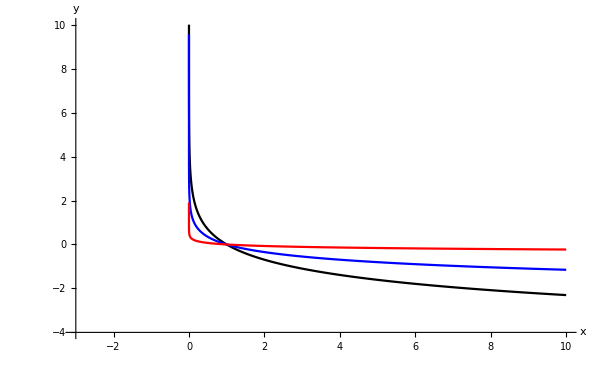

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->18,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->25,FontFamily->Latinfont]]&;
Plot[{-Log[x],-0.5Log[x],-0.1Log[x]},{x,0,10},PlotRange->{{-3,10},{-4,10}},PlotStyle->{Black,Blue,Red},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},AxesOrigin->{-3,-4},ImageSize->600,PlotPoints->2000]
Manipulate[Plot[{-c*Log[x]},{x,0,10},PlotRange->{{-3,10},{-4,10}},PlotStyle->Blue,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},AxesOrigin->{-3,-4},ImageSize->600,PlotPoints->2000,GridLines->Automatic,Epilog->Inset[Row[{Style["c",Black,Italic,FontSize->25,FontFamily->Latinfont],Style[" = "<>ToString[c],Black,FontSize->25,FontFamily->Latinfont]}],{5,3}]],{{c,0.6},0,2,0.01},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,Italic,FontSize->24],TrackedSymbols:>True];
```

## 非凸二次函数xy

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Plot3D[x*y,{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{-5,5}},BoxRatios->{1,1,0.6},Mesh->30,MeshStyle->Directive[{White,Opacity[0.7]}], PlotStyle->Directive[Red, Specularity[White,60]],Filling->Bottom, BoundaryStyle->{AbsoluteThickness[1],LightGray},
AxesStyle->{axesStyle,axesStyle,axesStyle},
AxesLabel->textStyle/@{"x","y"," "}, 
ClippingStyle->None,ImageSize->500,PlotPoints->100,AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{-5,5}},BoxRatios->{1,1,0.6},Mesh->30,MeshStyle->Directive[{White,Opacity[0.7]}],PlotStyle->Directive[Red, Specularity[White,60]],Filling->Bottom, BoundaryStyle->{AbsoluteThickness[1],LightGray},
AxesStyle->{axesStyle,axesStyle,axesStyle},
AxesLabel->textStyle/@{"x","y"," "}, 
ClippingStyle->None,ImageSize->500,PlotPoints->100,AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

## 双S形速度规划

```mathematica
Manipulate[
CalculateTimes[]:=Module[{s},
s=s1-s0;
(*Case 1:vlim=vmax*)
amaxnotreached=(vmax-v0)*jmax<amax^2;(*formula (3.19)*)
aminnotreached=(vmax-v1)*jmax<amax^2;(*formula (3.19)*)
If [amaxnotreached,
tj1=Sqrt[(vmax-v0)/jmax];(*//formula (3.21)*)
ta=2tj1;
,
tj1=amax/jmax;(*formula (3.22)*)
ta=tj1+(vmax-v0)/amax;
];
If [aminnotreached,
tj2=Sqrt[(vmax-v1)/jmax];(*//formula (3.21)*)
td=2tj1;
,
tj2=amax/jmax;(*formula (3.22)*)
td=tj2+(vmax-v1)/amax;
];
tv=s/vmax-ta/2*(1+v0/vmax)-td/2*(1+v1/vmax);(*formula (3.25)*)
(*Case 2:vlim<vmax*)
If[tv<0,
tj1=amax/jmax;(*formula (3.26a)*)
tj2=tj1;
delta=amax^4/jmax^2+2*(v0^2+v1^2)+amax*(4*s-2*amax/jmax*(v0+v1)); (*formula (3.27)*)
ta=(amax^2/jmax-2*v0+Sqrt[delta])/(2*amax);(*formula (3.26b)*)
td=(amax^2/jmax-2*v1+Sqrt[delta])/(2*amax);(*formula (3.26c)*)
tv=0;
];
(*Case 3:maximum (or minimum) acceleration is not reached,which is an unusual situation*) If[ta<2*tj1||td<2*tj2,
tv=0;
tj1=(s/2/jmax)^(1/3);
tj2=tj1;
ta=2tj1;
td=ta;
];
alima=jmax*tj1;
alimd=-jmax*tj2;
vlim=v0+(ta-tj1)*alima;
totalt=ta+tv+td;
];
GeneratePosition[t_]:=Module[{s},
If[t<0,Return[s0]];
If[t<=tj1,Return[s=s0+v0*t+jmax*t^3/6.0]];
If[t<=ta-tj1,Return[s=s0+v0*t+alima/6*(3*t^2-3*tj1*t+tj1^2)]];
If[t<=ta,Return[s=s0+(v0+vlim)*ta/2-vlim*(ta-t)-jmin*((ta-t)^3)/6.0]];
If[t<=ta+tv,Return[s=s0+(v0+vlim)*ta/2+vlim*(t-ta)]];
If[t<=totalt-td+tj2,Return[s=s1-(v1+vlim)*td/2+vlim*(t-totalt+td)-jmax*((t-totalt+td)^3)/6.0]];
If[t<=totalt-tj2,Return[s=s1-(v1+vlim)*td/2+vlim*(t-totalt+td)+alimd/6*(3*((t-totalt+td)^2)-3*tj2*(t-totalt+td)+tj2^2)]];
If[t<=totalt,Return[s=s1-v1*(totalt-t)-jmax*((totalt-t)^3)/6.0]];
Return[s1];
];
GenerateVelocity[t_]:=Module[{},
If[t<0,Return[v0]];
If[t<=tj1,Return[v=v0+jmax*t*t/2]];
If[t<=ta-tj1,Return[v=v0+alima*(t-tj1/2)]];
If[t<=ta,Return[v=vlim+jmin*(ta-t)*(ta-t)/2]];
If[t<=ta+tv,Return[v=vlim]];
If[t<=totalt-td+tj2,Return[v=vlim-jmax*(t-totalt+td)*(t-totalt+td)/2]];
If[t<=totalt-tj2,Return[v=vlim+alimd*(t-totalt+td-tj2/2)]];
If[t<=totalt,Return[v=v1+jmax*(totalt-t)*(totalt-t)/2]];
Return[v1];
];
GenerateAcceleration[t_]:=Module[{},
If[t<0,Return[a=0]];
If[t<=tj1,Return[a=jmax*t]];
If[t<=ta-tj1,Return[a=alima]];
If[t<=ta,Return[a=-jmin*(ta-t)]];
If[t<=ta+tv,Return[a=0]];
If[t<=totalt-td+tj2,Return[a=-jmax*(t-totalt+td)]];
If[t<=totalt-tj2,Return[a=alimd]];
If[t<=totalt,Return[a=-jmax*(totalt-t)]];
Return[0];
];
GenerateJerk[t_]:=Module[{},
If[t<tj1,Return[j=jmax]];
If[t<=ta-tj1,Return[j=0]];
If[t<=ta,Return[j=jmin]];
If[t<=ta+tv,Return[j=0]];
If[t<=totalt-td+tj2,Return[j=jmin]];
If[t<=totalt-tj2,Return[j=0]];
If[t<=totalt,Return[j=jmax]];
];
dt=0.01;
s0=0;
(*s1=1;*)
v0=0.5;
v1=0.5;
(*jmax=1;*)
jmin=-jmax;
(*amax=1;*)
amin=-amax;
(*vmax=1;*)
vmin=0;
CalculateTimes[];
profile=Transpose@Table[{GeneratePosition[t],GenerateVelocity[t],GenerateAcceleration[t],GenerateJerk[t]},{t,0,totalt,dt}];
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->22,FontFamily->Latinfont]]&;
ticks1=Table[{n,n*dt},{n,0,totalt/dt+30,50}];
ListLinePlot[profile,PlotStyle->{Black,Red,Blue,Darker@Green},
PlotLegends->Placed[LineLegend[Style[#,Italic,FontSize->20,FontFamily->Latinfont]&/@{"s","v","a","j"},Spacings->{1,0.4}],{0.1,0.8}],
AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"t",""},PlotRange->{{0,totalt/dt+30},{-3,7}},Axes->True,ImagePadding->{{10,18},{0,5}},ImageSize->600,Ticks->{ticks1,Automatic}],
Grid[{{Control[{{s1,5,Style["s",controlfontsize]},0,10,0.01,ImageSize->barsize}],
Control[{{vmax,1.5,Style["v_max",controlfontsize]},0,5,0.01,ImageSize->barsize}],
Control[{{amax,1,Style["a_max",controlfontsize]},0,10,0.01,ImageSize->barsize}],
Control[{{jmax,2,Style["j_max",controlfontsize]},0,4,0.01,ImageSize->barsize}]}}],
(*{{s1,5},0,10,0.01},{{vmax,1.5},0,5,0.01},{{amax,1},0,10,0.01},{{jmax,2},0,10,0.01},*)
LabelStyle->Directive[Black,Italic,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True,Initialization:>{controlfontsize=18,barsize=100;}]
```

## 双S形速度规划公式

```mathematica
Integrate[v0+J*t^2/2,{t,0,T}]+Integrate[(v1+v0)/2+J*T*t-J*t^2/2,{t,0,T}]
```

(J T^3)/2+T v0+1/2 T (v0+v1)

```mathematica
(*T=a/J;*)
vm=v0+Integrate[J*t,{t,0,T}]
vn=vm+a*Ta
v1=vn+Integrate[a-J*t,{t,0,T}]
```

(J T^2)/2+v0

(J T^2)/2+a Ta+v0

a T+a Ta+v0

```mathematica
Ta=(J*v1-a^2-v0*J)/(a *J)
```

(-a^2-J v0+J v1)/(a J)

```mathematica
Simplify[Integrate[v0+J*t^2/2,{t,0,T}]+
Integrate[vm+a*t,{t,0,Ta}]+
Integrate[vn+a*t-J*t^2/2,{t,0,T}]]
```

((v0+v1) (a^2+J (-v0+v1)))/(2 a J)

```mathematica
vlim=(T1*a*J-a^2)/J+v0;
(*vlim=a^2/J+v0;*)
Solve[((v0+vlim)T1)/2+((v1+vlim)T2)/2==s&&(T1*a*J-a^2)/J+v0==v1+(T2*a*J-a^2)/J,{T1,T2}]
```

{{T1→(a^3-2 a J v0-√(a^6+16 a^3 J^2-2 a^4 J v0+2 a^2 J^2 v0^2-2 a^4 J v1+2 a^2 J^2 v1^2))/(2 a^2 J),T2→(a^2/J-2 v1-(√(a^2 (a^4+16 a J^2-2 a^2 J v0+2 J^2 v0^2-2 a^2 J v1+2 J^2 v1^2)))/(a J))/(2 a)},{T1→(a^3-2 a J v0+√(a^6+16 a^3 J^2-2 a^4 J v0+2 a^2 J^2 v0^2-2 a^4 J v1+2 a^2 J^2 v1^2))/(2 a^2 J),T2→(a^2/J-2 v1+(√(a^2 (a^4+16 a J^2-2 a^2 J v0+2 J^2 v0^2-2 a^2 J v1+2 J^2 v1^2)))/(a J))/(2 a)}}

```mathematica
a^2 (a^4+4 a J^2 s+2 a^2 J v0+2 J^2 v0^2+2 a^2 J v1+2 J^2 v1^2)/a^2/J^2
```

(a^4+4 a J^2 s+2 a^2 J v0+2 J^2 v0^2+2 a^2 J v1+2 J^2 v1^2)/J^2

## SmoothL1损失函数

```mathematica
Timesfont="Times New Roman";
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->18,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->25,FontFamily->Latinfont]]&;
Plot[{Piecewise[{{0.5x^2,Abs[x]<=1},{Abs[x]-0.5,Abs[x]>1}}],0.5x^2},{x,-3,3},PlotRange->{{-3,3},{-0.2,3.5}},PlotStyle->{Blue,Red},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},AspectRatio->0.6,ImageSize->600]
```

## SVM升维的例子

```mathematica
(*pts=RandomReal[{-2,2},{500,2}];*)
g[n_,{low_,high_},minDist_,step_:1]:=Block[{data=RandomReal[{low,high},{n,2}],temp,happy,sdata,hdata},
While[True,
temp=((Nearest[data][#,2][[-1]]&/@data));
happy=Boole@Thread[MapThread[EuclideanDistance,{temp,data}]>minDist];
hdata=Pick[data,happy,1];
sdata=Pick[data,happy,0];
If[sdata==={},Break[]];
sdata+=RandomReal[{-step,step},{Length[sdata],2}];
data=Join[sdata,hdata];];
data];
pts=g[1000,{-3,3},0.1,1];
pts1=Table[If[Norm[pt]<=1,pt,Nothing],{pt,pts}];
pts2=Complement[pts,pts1];
pts2=Table[If[Norm[pt]<=1.7,pt,Nothing],{pt,pts2}];
```

```mathematica
Latinfont="Latin Modern Roman 10";
square[{x_,y_}]:={Red,Text["●",{x,y}]};
disk[{x_,y_}]:={Black,Text[Style["■",13],{x,y}]};
Graphics[{Circle[],Gray,Opacity[0.1],Disk[],Opacity[1],Map[square,pts1],Map[disk,pts2]},Frame->True,FrameTicks->None,FrameStyle->Directive[Gray,FontSize->15,FontFamily->Latinfont]]
pts13d=Table[{x,y}=pt; {x,y,x*x+y*y},{pt,pts1}];
pts23d=Table[{x,y}=pt; {x,y,x*x+y*y},{pt,pts2}];
square[{x_,y_,z_}]:={Red,Text["●",{x,y,z}]};
disk[{x_,y_,z_}]:={Black,Text[Style["■",13],{x,y,z}]};
Graphics3D[{AbsolutePointSize[4],Map[square,pts13d],Map[disk,pts23d],Green,Opacity[1],Hyperplane[{0,0,1},{0,0,1}]},BoxRatios->{1, 1, 0.6},Boxed->True(*,ViewPoint->{0,∞,0}*)]
```

## 插值（贝塞尔/B样条/三次样条/Hermite）

```mathematica
data={{0.1,0.1},{0.4,0.7},{1.2,0.6},{1.8,1.1},{2,0.9}};
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
p1=Graphics[{
f=BezierFunction[pts];bfpts=f/@Range[0,1,0.01];AbsoluteThickness[1.4],
Darker@Green,Line@bfpts},Axes->True,PlotRange->{{0,2.2},{0,1.7}}];
p2=Graphics[{
f=BSplineFunction[pts,SplineDegree->d];bfpts=f/@Range[0,1,0.01];
AbsoluteThickness[1.4],Black,Line@bfpts,Red,AbsolutePointSize[6],Point[pts]},Axes->True,PlotRange->{{0,2.2},{0,1.7}}];
fun=ResourceFunction["CubicSplineInterpolation"][pts,"Natural"];
p3=Plot[fun[x],{x,0.1,2.0},Epilog->{Directive[AbsolutePointSize[5],ColorData[97,4]],Point[data]},PlotRange->All,PlotStyle->{Red}];
p4=Plot[Interpolation[pts,Method->"Hermite",InterpolationOrder->3][x],{x,0.1,2},PlotStyle->{Blue}];
pall=Show[{p1,p2,p3,p4},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"}],{{pts,data},Locator,LocatorAutoCreate->True,Appearance->Style["●",Red,14]},{{d,3,"degree"},1,3,1},TrackedSymbols:>True]
```

## 插值与拟合的区别

```mathematica
n=5;
datapts=Transpose[{Range[0,n,1],RandomReal[{-1,1},n+1]}];
datapts={{0,0.3},{0.875,-0.18},{1.99,0.65},{3.095,0.89},{4.145,0.85},{4.95,1.45}};
(*f[x]:=*)
f=Interpolation[datapts,InterpolationOrder->3];
p=Graphics[{Red,AbsolutePointSize[5],Point[datapts]}];
polyf= Fit[datapts, {1,x,x^2,x^3}, x]
Show[p,Plot[f[x],{x,0,5}], Plot[{line, parabola}, {x, 0, 5}]]
```

0.171796-0.152894 x+0.170376 x^2-0.0186737 x^3

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
Manipulate[
datapts2=pts;
f=Interpolation[pts,InterpolationOrder->d];
polyf =Fit[pts, {1,x,x^2,x^3}, x];
p1=Plot[f[x],{x,0,5},PlotStyle->{Red},
AxesStyle->{axesStyle,axesStyle},
AxesLabel->textStyle/@{"x","y"},
PlotRange->{{-0.5,5.5},{-1,2}},
Ticks->None,
Axes->True,
Frame->False,
ImageSize->500];
p2=Plot[polyf, {x, 0, 5},PlotStyle->{Blue}];
p3=Graphics[{Black,AbsolutePointSize[8],Point[pts]}];
Show[p1,p2,p3],{{pts,datapts},Locator,LocatorAutoCreate->True},{{d,5,"InterpolationOrder"},2,6,1},ControlPlacement->Top]
```

## Frenet坐标系

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->14,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->20,FontFamily->Latinfont]]&;
DynamicModule[{c,b,t,pt,x},
c[t_]={t,1.2+0.4(t-0.5)-0.3(t-0.5)^2+0.040(t-0.5)^3};
b[t_]=Last[FrenetSerretSystem[c[t],t]];
x=Dynamic[First[pt]];
LocatorPane[Dynamic[pt,(pt=c[First[#]])&],p=Show[Plot[Last[c[t]],{t,0.5,6.5},PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},Method->{"AxesInFront"->False},AspectRatio->Automatic,ImageSize->600,PlotRange->{{-0.5,7.5},{-0.5,2}}],Graphics[{Thick,Blue,Arrowheads[0.025],Arrow[Dynamic/@{c[x],c[x]+b[x]⟦1⟧}],Red,Arrow[Dynamic/@{c[x],c[x]+b[x]⟦2⟧}]}]],Appearance->Graphics[{Red,Disk[{0,0},1]},ImageSize->7]],Initialization:>(pt={2,1})]
```

## 汽车可达集

```mathematica
CarKinematics=Compile[{{pose,_Real,1},{v,_Real},{ϕ,_Real},{T,_Real}},
Module[{dt=0.002,L=1,path,x,y,θ,va},
{x,y,θ}=pose;
path={{x,y,θ}};
va=Abs[v];
Do[
x=x+dt*v*Cos[θ];
y=y+dt*v*Sin[θ];
θ=θ+dt*(va*Tan[ϕ])/L;
AppendTo[path,{x,y,θ}];
,{i,0,T,dt}];
path
],CompilationTarget->"C",RuntimeOptions->"Speed"
];
```

```mathematica
drawLine[color_,th_,pts_]:=Module[{},{color,AbsoluteThickness[th],Line@pts,{EdgeForm[Directive[AbsoluteThickness[th],color]],Disk[pts[[1]],0.01],
Disk[pts[[-1]],0.01]}}];
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
car=-Graphics-;
carGraphics=GraphicsComplex[((-Mean[car⟦1,1⟧]+{630,0})+#&/@car⟦1,1⟧)/6000.0,car⟦1,2⟧];
move2D[shape_,pose_]:=Module[{p=pose[[1;;2]],theta=pose[[3]]},Translate[Rotate[shape,theta,{0,0}],p]]
Manipulate[
controls=Flatten[Table[{v,ϕ},{v,-1,1,1},{ϕ,-Pi/4,Pi/4,Δϕ}],1];
paths=Table[Qs=CarKinematics[{0,0,0},c⟦1⟧,c⟦2⟧,T],{c,controls}];
Graphics[{(*carGraphics,move2D[carGraphics,#]&/@paths⟦;;,-1⟧,*)drawLine[Blue,1,#]&/@paths⟦;;,;;,1;;2⟧},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},Axes->True,ImageSize->500,PlotRange->{{-1,1}*1.5,{-1,1}*2.2}]
,{T,1,4,0.01},{{Δϕ,Pi/900},Pi/460,Pi/4,Pi/40},ControlPlacement->Top,LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->12],TrackedSymbols:>True];
```

```mathematica
textStyleRegular=Text[Style[#,FontSize->18,FontFamily->Latinfont]]&;
textStyleItalic=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Graphics3D[{Blue,AbsolutePointSize[1],Point@Flatten[paths,1]},Axes->True,ImageSize->500,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->{textStyleItalic["x"],textStyleItalic["y"],textStyleRegular["θ"]},BoxRatios->{1, 1, 0.8},PlotRange->{{-1,1}*1.2,{-1,1}*1.2,{-Pi,Pi}*0.5}]
```

```mathematica
{xRange,yRange,θRange}={2.0,2.0,2.0Pi};
{nx,ny,nθ}={200,200,360}*2;
Times@@{nx,ny,nθ};
{hx,hy,hθ}={xRange,yRange,θRange}/({nx,ny,nθ}-1);
unitlength=ReadList[OpenRead["C:\\v.txt"],Number];
Count[unitlength,1];
unitlength//Dimensions;
pts=Table[If[unitlength⟦200*360*2*2*(x-1)+360*2*(y-1)+θ⟧>0,{-1,-1,-Pi}+{hx,hy,hθ}*{x,y,θ},Nothing],{x,nx},{y,ny},{θ,nθ}];
pts=Flatten[pts/. {}->Nothing,2];
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyleRegular=Text[Style[#,FontSize->18,FontFamily->Latinfont]]&;
textStyleItalic=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
Graphics[{Blue,AbsolutePointSize[1.2],Point@pts⟦;;,1;;2⟧},Axes->True,ImageSize->400,AxesStyle->{axesStyle,axesStyle},AxesLabel->{textStyleItalic["x"],textStyleItalic["y"]},PlotRange->{{-1,1}*1.2,{-1,1}*1.2}];
Graphics3D[{Blue,AbsolutePointSize[1.4],Point@pts},Axes->True,ImageSize->500,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->{textStyleItalic["x"],textStyleItalic["y"],textStyleRegular["θ"]},BoxRatios->{1, 1,1},PlotRange->{{-1,1}*1.2,{-1,1}*1.2,{-Pi,Pi}*0.5}]
```

## 混合A*

垂直车位

```mathematica
Max@steer(*最大转角*)
Max@steer*180/Pi
8.726646/16.26
2.5/Tan[Max@steer](*最小转向半径*)
```

```mathematica
data=Import["C:\\Users\\Administrator\\Desktop\\vertical\\smoothed.txt","Table"];
hdata=Import["C:\\Users\\Administrator\\Desktop\\vertical\\hybridastar.txt","Table"];
parkspace=Import["C:\\Users\\Administrator\\Desktop\\vertical\\parkspace.txt","Table"];
steer=Transpose@Import["C:\\Users\\Administrator\\Desktop\\vertical\\steer_acc.txt","Table"];
nodesforward=Import["C:\\Users\\Administrator\\Desktop\\vertical\\nodesforward.txt","Table"];
nodesbackward=Import["C:\\Users\\Administrator\\Desktop\\vertical\\nodesbackward.txt","Table"];
data//Dimensions
positions=data⟦;;,1;;2⟧;
hpositions=hdata⟦;;,1;;2⟧;
poses=data⟦;;,1;;3⟧;
speed=data⟦;;,5⟧;
steer=data⟦;;,6⟧;
poseToH[{x_,y_,a_}]:={{Cos[a],-Sin[a],x},{Sin[a],Cos[a],y},{0,0,1}};
TransPt[g_][pt_]:=Module[{homogeneousPt,transfomredPt,n=Length[pt]},
      homogeneousPt=Join[pt,{1.0}];
      transfomredPt=g.homogeneousPt;
      transfomredPt[[1;;n]]
     ];
ListLinePlot[speed,PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},(*AxesLabel->textStyle/@{"x","y"},*)Axes->True,ImageSize->600,PlotRange->{{0,2400},{-0.6,1.2}}(*,AspectRatio->0.5*)];
```

{2311,7}

```mathematica
(*steer//Dimensions
f=Interpolation[steer⟦1⟧,InterpolationOrder->1];
steer=f/@Range[0,70,70/2311.];
steer//Dimensions
ListLinePlot[steer,PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},(*AxesLabel->textStyle/@{"x","y"},*)Axes->True,ImageSize->600,PlotRange->{{0,2400},{-0.7,0.7}}(*,AspectRatio->0.5*)];*)
```

```mathematica
v=parkspace⟦7⟧-parkspace⟦6⟧;
angle=ArcTan@@v;
parkspace=TransPt[poseToH[{0,0,-angle}]]/@parkspace;
positions=TransPt[poseToH[{0,0,-angle}]]/@positions;
hpositions=TransPt[poseToH[{0,0,-angle}]]/@hpositions;
poses=Table[Flatten@{TransPt[poseToH[{0,0,-angle}]]@pose⟦1;;2⟧,pose⟦3⟧-angle},{pose,poses}];
{L,W}={4,2};
wheelbase=2.5;
front`edge`to`center=2.8;
offset=front`edge`to`center-L/2;
carCorners={offset,0}+#&/@(0.5{L,W}*#&/@{{1,1},{1,-1},{-1,-1},{-1,1}});
carcornersTrans=TransPt[poseToH[{x,y,θ}]]/@carCorners;
carCorner[{x_,y_,θ_}]:={{1. x+2.8 Cos[θ]-0.9 Sin[θ],1. y+0.9 Cos[θ]+2.8 Sin[θ]},{1. x+2.8 Cos[θ]+0.9 Sin[θ],1. y-0.9 Cos[θ]+2.8 Sin[θ]},{1. x-1.2 Cos[θ]+0.9 Sin[θ],1. y-0.9 Cos[θ]-1.2 Sin[θ]},{1. x-1.2 Cos[θ]-0.9 Sin[θ],1. y+0.9 Cos[θ]-1.2 Sin[θ]}};
```

```mathematica
carstart={FaceForm[{Opacity[0.2],Darker@Red}],EdgeForm[{Opacity[1],Red,AbsoluteThickness[1]}],Polygon[carCorner[poses⟦1⟧]]};
carend={FaceForm[{Opacity[0.2],Darker@Green}],EdgeForm[{Opacity[1],Darker@Green,AbsoluteThickness[1]}],Polygon[carCorner[poses⟦-1⟧]]};
cars={FaceForm[],EdgeForm[{Opacity[1],Gray,Thickness[0.001]}],Polygon[carCorner[#]]&/@poses⟦1;;-1;;10⟧};
Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],cars,Blue,AbsoluteThickness[1.5],Line[positions],Red,Line[hpositions],carstart,carend,Point[nodesforward]},ImageSize->500,Background->Gray,Axes->False]
```

```mathematica
Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],carstart,carend,AbsolutePointSize[1.5],Point[TransPt[poseToH[{0,0,-angle}]]/@nodesforward]},ImageSize->500,Background->Gray,Axes->False]
Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],carstart,carend,AbsolutePointSize[1.5],Point[TransPt[poseToH[{0,0,-angle}]]/@nodesbackward]},ImageSize->500,Background->Gray,Axes->False]
```

平行车位

```mathematica
data=Import["C:\\Users\\Administrator\\Desktop\\parallel\\smoothed.txt","Table"];
hdata=Import["C:\\Users\\Administrator\\Desktop\\parallel\\hybridastar.txt","Table"];
parkspace=Import["C:\\Users\\Administrator\\Desktop\\parallel\\parkspace.txt","Table"];
steer=Transpose@Import["C:\\Users\\Administrator\\Desktop\\parallel\\steer_acc.txt","Table"];
nodesforward=Import["C:\\Users\\Administrator\\Desktop\\parallel\\nodesforward.txt","Table"];
nodesbackward=Import["C:\\Users\\Administrator\\Desktop\\parallel\\nodesbackward.txt","Table"];
data//Dimensions
positions=data⟦;;,1;;2⟧;
hpositions=hdata⟦;;,1;;2⟧;
poses=data⟦;;,1;;3⟧;
speed=data⟦;;,5⟧;
steer=data⟦;;,6⟧;
poseToH[{x_,y_,a_}]:={{Cos[a],-Sin[a],x},{Sin[a],Cos[a],y},{0,0,1}};
TransPt[g_][pt_]:=Module[{homogeneousPt,transfomredPt,n=Length[pt]},
      homogeneousPt=Join[pt,{1.0}];
      transfomredPt=g.homogeneousPt;
      transfomredPt[[1;;n]]
     ];
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->12,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->18,FontFamily->Latinfont]]&;
ListLinePlot[speed,PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},(*AxesLabel->textStyle/@{"x","y"},*)Axes->True,ImageSize->600,PlotRange->{{0,2700},{-1.2,1.2}}];
```

{2571,7}

```mathematica
steer//Dimensions
f=Interpolation[steer⟦1⟧,InterpolationOrder->1];
steer=f/@Range[0,87,87/2571.];
steer//Dimensions
ListLinePlot[steer,PlotStyle->Black,AxesStyle->{axesStyle,axesStyle},(*AxesLabel->textStyle/@{"x","y"},*)Axes->True,ImageSize->600,PlotRange->{{0,2700},{-0.7,0.7}}(*,AspectRatio->0.5*)];
```

```mathematica
v=parkspace⟦7⟧-parkspace⟦6⟧;
angle=ArcTan@@v;
parkspotW=2.5;
parkspotL=6;
parkspace=TransPt[poseToH[{0,0,-angle}]]/@parkspace;
positions=TransPt[poseToH[{0,0,-angle}]]/@positions;
hpositions=TransPt[poseToH[{0,0,-angle}]]/@hpositions;
poses=Table[Flatten@{TransPt[poseToH[{0,0,-angle}]]@pose⟦1;;2⟧,pose⟦3⟧-angle},{pose,poses}];
{L,W}={4,2};
wheelbase=2.5;
front`edge`to`center=2.8;
offset=front`edge`to`center-L/2;
carCorners={offset,0}+#&/@(0.5{L,W}*#&/@{{1,1},{1,-1},{-1,-1},{-1,1}});
carcornersTrans=TransPt[poseToH[{x,y,θ}]]/@carCorners;
carCorner[{x_,y_,θ_}]:={{1. x+2.8 Cos[θ]-0.9 Sin[θ],1. y+0.9 Cos[θ]+2.8 Sin[θ]},{1. x+2.8 Cos[θ]+0.9 Sin[θ],1. y-0.9 Cos[θ]+2.8 Sin[θ]},{1. x-1.2 Cos[θ]+0.9 Sin[θ],1. y-0.9 Cos[θ]-1.2 Sin[θ]},{1. x-1.2 Cos[θ]-0.9 Sin[θ],1. y+0.9 Cos[θ]-1.2 Sin[θ]}};
parkCorners=(0.5{parkspotL,parkspotW}*#&/@{{1,1},{1,-1},{-1,-1},{-1,1}});
parkCornersTrans=TransPt[poseToH[{x,y,θ}]]/@parkCorners;
parkCorner[{x_,y_,θ_}]:=
{{1. x+3. Cos[θ]-1.25 Sin[θ],1. y+1.25 Cos[θ]+3. Sin[θ]},{1. x+3. Cos[θ]+1.25 Sin[θ],1. y-1.25 Cos[θ]+3. Sin[θ]},{1. x-3. Cos[θ]+1.25 Sin[θ],1. y-1.25 Cos[θ]-3. Sin[θ]},{1. x-3. Cos[θ]-1.25 Sin[θ],1. y+1.25 Cos[θ]-3. Sin[θ]}};
```

```mathematica
carstart={FaceForm[{Opacity[0.5],Darker@Red}],EdgeForm[{Red,AbsoluteThickness[1.5]}],Polygon[carCorner[poses⟦1⟧]]};
carend={FaceForm[{Opacity[0.5],Darker@Green}],EdgeForm[{Darker@Green,AbsoluteThickness[1.5]}],Polygon[carCorner[poses⟦-1⟧]]};
carend2={FaceForm[{Opacity[0.2],Darker@Green}],EdgeForm[{Darker@Green,AbsoluteThickness[1.5]}],Polygon[carCorner[{69,-5,Pi+0.02}]]};
cars={FaceForm[],EdgeForm[{Opacity[1],Darker@Gray,AbsoluteThickness[0.7]}],Polygon[carCorner[#]]&/@poses⟦1;;-1;;10⟧};
parkspot={FaceForm[{Opacity[0.2],Darker@Red}],EdgeForm[{Opacity[1],Red,AbsoluteThickness[1]}],Polygon[ TransPt[poseToH[{0,0,angle}]]/@parkCorner[{67.8,-6.3,0}]]};
Graphics[{(*parkspot,carend2,*)EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],AbsoluteThickness[2],cars,Blue,AbsoluteThickness[2],Line[positions],Red,Line[hpositions],carstart,carend},ImageSize->500,Background->Gray,Axes->False]
```

```mathematica
(*carstart={FaceForm[{Opacity[0.3],Darker@Red}],EdgeForm[{Red,AbsoluteThickness[1.5]}],Polygon[carCorner[poses⟦1⟧]]};
carend={FaceForm[{Opacity[0.3],Darker@Green}],EdgeForm[{Darker@Green,AbsoluteThickness[1.5]}],Polygon[carCorner[poses⟦-1⟧]]};Graphics[{carstart,carend,Blue,AbsoluteThickness[2],Line[positions],Red,Line[hpositions]},ImageSize->500,Axes->False]*)
```

```mathematica
Manipulate[
car={FaceForm[],EdgeForm[{Opacity[1],Gray,Thickness[0.001]}],Polygon[carCorner[poses⟦i⟧]]};
Graphics[{(*parkspot,carend2,*)AbsoluteThickness[2],Line[parkspace],car,Point[positions⟦i⟧],Blue,AbsoluteThickness[1.5],Line[positions],Red,Line[hpositions],carstart,carend},ImageSize->500,Axes->True],{i,1,Length[poses],1}]
```

```mathematica
GraphicsRow[{Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],carstart,carend,AbsolutePointSize[2],Point[TransPt[poseToH[{0,0,-angle}]]/@nodesbackward]},ImageSize->500,Background->Gray,Axes->False],
Graphics[{EdgeForm[{Black,AbsoluteThickness[1.5]}],FaceForm[White],Polygon[parkspace],carstart,carend,AbsolutePointSize[2],Point[TransPt[poseToH[{0,0,-angle}]]/@nodesforward]},ImageSize->500,Background->Gray,Axes->False]},ImageSize->1500,ImagePadding->0]
```

## DP搜索的结果

```mathematica
data=Import["C:\\Users\\q\\Desktop\\q.txt","Table"];
{rows,cols}=Dimensions[data];
data3d=Table[{row-1,col-1,If[data⟦row,col⟧=="inf",-1000000,data⟦row,col⟧]},{row,rows},{col,cols}];
```

```mathematica
MatrixForm[Reverse@Transpose@data];
```

```mathematica
p1=ListPointPlot3D[Transpose@data, PlotStyle->AbsolutePointSize[5],ColorFunction->"SouthwestColors",(*PlotRange->{All,All,{0,1000000}},*)(*ViewPoint->{0,0,Infinity},*)(*BoxRatios->{1, 0.8, 0.2},*)ImageSize->500,Filling->Bottom];
profile={{0,0},{1,1},{2,3},{3,5.5},{4,7},{5,7.5},{6,8},{7,8.5},{8,9}};
profile3d=Table[{pt⟦1⟧,2pt⟦2⟧,data⟦pt⟦1⟧+1,Round[2pt⟦2⟧]+1⟧},{pt,profile}];
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->18,FontFamily->Latinfont,Arrowheads[{0,0.025}]};
textStyle=Text[Style[#,Italic,FontSize->27,FontFamily->Latinfont]]&;
Graphics3D[{AbsolutePointSize[4],Point[Flatten[data3d,1]],Darker@Green,AbsoluteThickness[1.2],Line[profile3d],Red,AbsolutePointSize[7],Point@profile3d},PlotRange->{{-1,rows},{-1,cols+1},{-100000,1.2Max[data3d]}},Boxed->True,Axes->True,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"t","s"},Ticks->{Range[0,8],Transpose[{Range[0,70,10],Range[0,35,5]}],Range[0,1.2Max[data3d],1.2Max[data3d]/5]},BoxRatios->{1, 0.5,0.5},ImageSize->700(*,ViewPoint->{0,0,Infinity}*)]
```

{37.5758,8.33333,1.5}

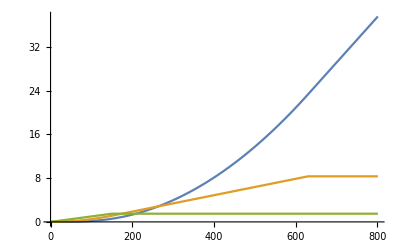

```mathematica
vmax=30/3.6;
amax=1.5;
jmax=1.0;
dt=0.01;
a=v=s=0;
res=Table[
a+=jmax*dt;
If[a>amax,a=amax];
v+=a*dt;
If[v>vmax,v=vmax];
s+=v*dt;
{s,v,a},{t,0,8,dt}];
Last[res]
ListLinePlot[Transpose@res,PlotRange->{{0,T/dt},All}]
```

# 第八章 运动控制

## Lyapunov函数和水平集

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->23,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->40,FontFamily->Latinfont]]&;p1=Plot3D[(x^2+y^2)/2-0.007,{x,-2,2},{y,-2,2},Mesh->None, PlotStyle->Directive[Opacity[0.2],Cyan, Specularity[White,20]],PlotPoints->120,PlotRange->{{-2,2},{-2,2}},PerformanceGoal->"Quality",RegionFunction->Function[{x,y,z},0<x^2+y^2<2.6],BoxRatios->{1,1,0.6},AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"," "},Axes->True,ImageSize->700];
p2=ParametricPlot3D[Table[{√(2k)Sin[u],√(2k)Cos[u],k},{k,0.1,1.3,0.15}],{u,0,10},PlotPoints->150,PlotRange->{{-2,2},{-2,2}}, PlotStyle->Directive[AbsoluteThickness[3],Red, Specularity[White,20]],BoxRatios->{1,1,0.6}];
Show[p1,p2]
```

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->23,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->40,FontFamily->Latinfont]]&;
ContourPlot3D[Evaluate@Table[(x^2+y^2+z^2)/2==c,{c,Range[0.1,1.5,0.25]}],{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,(* PlotStyle->Directive[Opacity[0.2],Cyan, Specularity[White,20]],*)PlotPoints->170,PlotRange->{{-2,2},{-2,2}},ContourStyle->Table[RGBColor[0.5+1-i,0.5+1-i,0.5+1-i],{i,0.1,1,0.15}],PerformanceGoal->"Quality",RegionFunction->Function[{x,y,z},!(0>x&&0>y)],RegionBoundaryStyle->None,BoxRatios->Automatic,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","z"},Axes->True,ImageSize->700,PlotRangePadding->{Automatic,Automatic,Scaled[0.02]},Ticks->{Automatic,Automatic,Automatic},ViewAngle->0.50885,ViewCenter->{{0.5,0.5,0.5},{0.531099,0.631116}},ViewPoint->{-1.89717,-2.19456,-1.74203},ViewVertical->{-0.0389836,-0.0485504,-0.99806}]
```

```mathematica
p1=Table[Plot3D[(x^2+y^2)/2,{x,-2,2},{y,-2,2},Mesh->None, PlotStyle->Directive[Opacity@i,Cyan, Specularity[White,20]],PlotPoints->120,PlotRange->{{-2,2},{-2,2}},PerformanceGoal->"Quality",RegionFunction->Function[{x,y,z},0<x^2+y^2<2.6],BoxRatios->{1,1,0.6}],{i,0,1,0.1}];
p2=Table[ParametricPlot3D[Table[{√(2k)Sin[u],√(2k)Cos[u],k},{k,0.1,1.3,0.15}],{u,0,10},PlotPoints->120,PlotRange->{{-2,2},{-2,2}}, PlotStyle->Directive[Opacity[1-i],Red, Specularity[White,20]],BoxRatios->{1,1,0.6}],{i,0,1,0.1}];
Manipulate[Show[p1⟦i⟧,p2⟦i⟧,ImageSize->300,FrameMargins->Large],Control[{{i,11,Style["a",12]},1,11,1,ImageSize->Small}],TrackedSymbols:>All]
```

## R^3中的李括号

下面计算李括号[f,g]

```mathematica
f={Cos[θ],Sin[θ],0};
g={0,0,1};
Skew[{v1_,v2_,v3_}]:={{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
SkewToVector[Mat_]:={Mat[[3,2]],Mat[[1,3]],Mat[[2,1]]};
h=Skew[f].g(*第一种计算方式*)
h=SkewToVector[Skew[f].Skew[g]-Skew[g].Skew[f]](*第二种计算方式*)
MatrixRank[{f,g,h}](*求矩阵的秩*)
```

{Sin[θ],-Cos[θ],0}

{Sin[θ],-Cos[θ],0}

3

## 侧方向泊车的向量场

```mathematica
Latinfont="Latin Modern Roman 10";
axesStyle={Black,AbsoluteThickness[0.6],FontSize->16,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,Italic,FontSize->26,FontFamily->Latinfont]]&;
L[{x_,y_,θ_}][t_]:={x+Sin[θ+t]-Sin[θ],y-Cos[θ+t]+Cos[θ],θ+t};
R[{x_,y_,θ_}][t_]:={x-Sin[θ-t]+Sin[θ],y+Cos[θ-t]-Cos[θ],θ-t};
S[{x_,y_,θ_}][t_]:={x+t*Cos[θ],y+t*Sin[θ],θ};
dt=0.005;
LRLR[pose0_][T_]:=Module[{pose,poses},
pose=pose0;
poses=Table[L[pose][t],{t,0,T,dt}];
pose=poses[[-1]];
poses=poses~Join~Table[R[pose][t],{t,0,T,dt}];
pose=poses[[-1]];
poses=poses~Join~Table[L[pose][t],{t,0,-T,-dt}];
pose=poses[[-1]];
poses=poses~Join~Table[R[pose][t],{t,0,-T,-dt}];
pose=poses[[-1]];
poses
]
Manipulate[
pose={0,0,0};
poses={};
Table[poses=poses~Join~LRLR[pose][T];pose=poses[[-1]],{i,n}];
Graphics[{AbsoluteThickness[1.5],Blue,Line[poses[[;;,1;;2]]]},Axes->True,PlotRange->{{-0.7,1},{-0.1,1.5}},AxesStyle->{axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y"},ImageSize->600],{{n,10,"n"},1,20,1},{{T,0.25},0,1,0.01},LabelStyle->Directive[Black,FontFamily->Latinfont,FontSize->25],ControlPlacement->Top,TrackedSymbols:>True]
```

```mathematica
v=1;
l=1;
ϕ=Pi/4;
f[{x_,y_,θ_}][{v_,ϕ_}]:={v*Cos[θ],v*Sin[θ],v/l*Tan[ϕ]};
p1=VectorPlot3D[f[{x,y,θ}][{1,Pi/4}],{x,-3,3},{y,-3,3},{θ,-Pi,Pi}, VectorPoints->10,VectorMarkers->"Arrow",VectorSizes->0.75,VectorStyle->Arrowheads[0.05]];
```

```mathematica
X={0,0,0};
U={1,Pi/4};
dt=0.02;
T=50;
X1s=Table[X+=f[X][U]*dt,{t,T}];
U={1,-Pi/4};
X2s=Table[X+=f[X][U]*dt,{t,T}];
U={-1,Pi/4};
X3s=Table[X+=f[X][U]*dt,{t,T}];
U={-1,-Pi/4};
X4s=Table[X+=f[X][U]*dt,{t,T}];
Xs=Flatten[{X1s,X2s,X3s,X4s},1];

Latinfont="Latin Modern Roman 10";
axesStyle={Black,FontSize->15,FontFamily->Latinfont,Arrowheads[{0,0.02}]};
textStyle=Text[Style[#,FontSize->23,FontFamily->Latinfont]]&;
p2=Graphics3D[{AbsoluteThickness[2],Red,Line[Xs]}(*,ViewPoint->{0,0,∞}*)];
Show[(*p1,*)p2,AxesStyle->{axesStyle,axesStyle,axesStyle},AxesLabel->textStyle/@{"x","y","θ"},Axes->True,ImageSize->500]
```

## 凸集的组合还是凸集

```mathematica
pts1={{0.0863609,-0.0849221},{-0.892959,-0.433004},{-0.755728,0.0954323},{0.0178608,-0.305137},{0.0874992,0.545086}};
pts2={{-0.0732489,0.921308},{0.689383,0.639966},{-0.226181,0.03866},{0.280335,0.918991},{-0.806149,0.544889}};
```

```mathematica
pts=RandomReal[{-1,1},{5,2}];
ℛ=ConvexHullRegion[pts];
Region[ℛ,Epilog-> {Black,Point[pts]},PlotRange->2];
```

```mathematica
pts1=pts1[[Last[FindShortestTour[pts1]]]];
pts2=pts2[[Last[FindShortestTour[pts2]]]];
pts3=Flatten[Table[pt1+pt2,{pt1,pts1},{pt2,pts2}],1];
pts4=Flatten[Table[pt2+pt1,{pt2,pts2},{pt1,pts1}],1];
ℛ3=ConvexHullRegion[pts3];
ℛ4=ConvexHullRegion[pts4];
polygons=Table[(#+pt1)&/@pts2,{pt1,pts1}];
Graphics[{FaceForm[],EdgeForm[Black],Polygon[pts1],EdgeForm[Red],Polygon[pts2],EdgeForm[Blue],ℛ3,EdgeForm[Blue],ℛ4,EdgeForm[Magenta],Polygon/@polygons},Axes->True]
```

# 其它

## Baidu Apollo中不同模块的代码统计

首先使用命令sudo rm -rf `find . -name “*.txt”`删除不是代码的文件
在Ubuntu中使用命令wc -l -w `find -name ‘*’`统计
{行数， 字符数}

Apollo 8.0

```mathematica
Localization={31467,98050};
Perception={120416,392099};
Planning={187058,796099};
CControl={7819,23441};
Routing={4034,11493};
Prediction={23432,67211};
Common={14401,54536};
Apollo={Routing,Localization,Perception,Planning,CControl};
Total[Apollo⟦;;,1⟧]
N[Total[Apollo⟦2;;3,1⟧]/Total[Apollo⟦;;,1⟧]]
PieChart[Apollo⟦;;,1⟧,ChartLegends->{"Routing","Localization","Perception","Planning","Control"}]
```

350794

0.432969

Autoware 1.13.0

```mathematica
Localization={18800,63209};
Perception={92461,352680};
Planning={140574,681688};
CControl={7141,22674};
Autoware={Localization,Perception,Planning,CControl};
Total[Autoware⟦;;,1⟧]
N[Total[Autoware⟦2;;3,1⟧]/Total[Autoware⟦;;,1⟧]]
PieChart[Autoware⟦;;,1⟧,ChartLegends->{"Localization","Perception","Planning","Control"}]
```

258976

0.899832

Openpilot 1.13.0